The following notebook is an accompanying section to the “2-tone analysis notebook.nb” and it serves to generate the figures
that we will use in the DP concept paper. The basic stimuli comparisons are generated by looking at “Mosquito 31/set 1”

Simply load up the name files for the laser and nerve, and you are good to go.
Regarding the stimuli, I simply copy/pasted the relevant elements from the NAS folder onto my Desktop and called that folder “test”.

```mathematica
ResourceFunction["DarkMode"][False]
```

```mathematica
<<AlexTools`ALXTools`
<<Spike2`FileCheck`
<<TwoTone`DP`
(*expDir="C:\\Users\\hadif\\Proton Drive\\c.a.alampounti\\My files\\Uni\\UCL\\Projects\\02_DP Theory paper\\images\\all figures\\";*)
expDir="C:\\Users\\hadif\\Proton Drive\\c.a.alampounti\\My files\\Uni\\UCL\\Projects\\02_DP Theory paper\\images\\article figures\\Nature submission 2\\raw_svg_figures\\";
imageRes=450;
```

## Stimuli Presentation

```mathematica
lookAtS="C:\\Users\\hadif\\OneDrive - University College London\\Desktop\\test\\";
stim=FileNames["*.txt",lookAtS];
dir=SetDirectory["M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito32\\set_1\\"];
expDir="C:\\Users\\hadif\\Proton Drive\\c.a.alampounti\\My files\\Uni\\UCL\\Projects\\02_DP Theory paper\\DP concept paper\\images\\all figures\\";
expConfig=Import[ParentDirectory[]<>"\\exp_config.txt","TSV"];
baseKey=StringTake[FileNameTake[FileNames["README*",ParentDirectory[]][[1]]],{8,-5}]
```

```mathematica
{laserfiles1T,laserfiles2T}=healthyFileFinder["\\Laser","\\Signal"];
healthyLaserFilesS=Flatten[{laserfiles1T,laserfiles2T}];
healthyLaserFilesS=SortBy[healthyLaserFilesS,ToExpression[StringTake[#,{-8,-6}]]&];
unhealthyLaserFiles=Complement[FileNames[StringDrop["\\Laser",1]<>"_*",dir<>"\\Laser"],healthyLaserFilesS];

{nervefiles1T,nervefiles2T}=healthyFileFinder["\\Nerve","\\Signal"];
healthyNerveFilesS=Flatten[{nervefiles1T,nervefiles2T}];
unhealthyNerveFiles=Complement[FileNames[StringDrop["\\Nerve",1]<>"_*",dir<>"\\Nerve"],healthyNerveFilesS];

frequencyList=expConfig[[7;;,2]]; (* this is the range of frequencies used *)
freqMap=AssociationThread[Range[Length@frequencyList],frequencyList]; (* mapping an experimental number with a frequency*)

freqs1T=freqMap[#]&/@Sort@ToExpression[StringTake[laserfiles1T,{-8,-6}]]; (* frequencies of the one-tone experiments that made it past the health check *)
freqs2T=freqMap[#]&/@Sort@ToExpression[StringTake[laserfiles2T,{-8,-6}]];(* frequencies of the two-tone experiments that made it past the health check *)
```

```mathematica
Manipulate[Grid[{{ListLinePlot[Import[ FileNames["*"<>ToString[freqs1T[[val]]]<>"*.txt",lookAtS][[1]],"CSV"][[;;4 20000 ;;10]],Frame->False,Axes->False,PlotLabel->freqs1T[[val]]]},
{ListLinePlot[Fold[HighpassFilter,readMyFile[laserfiles1T[[val]]][[;;,2]],(2π)/20000{60,60,60}][[250;;-0.2 sRate]],Frame->False,Axes->False]},
{ListLinePlot[Fold[HighpassFilter,readMyFile[nervefiles1T[[val]]][[;;,2]],(2π)/20000{60,60,60}][[250;;-0.2 sRate]],Frame->False,Axes->False]}}],{val,1,Length@laserfiles1T,1}]
```

```mathematica
val=30;
frame1={True,True,False,False};
frame2=False;
{pos,offset}={35000,500};
stimulus=Import[ FileNames["*_"<>ToString[freqs1T[[val]]]<>"_*.txt",lookAtS][[1]],"CSV"];
laser1T=-Fold[HighpassFilter,readMyFile[laserfiles1T[[val]]][[;;,2]],(2π)/20000{60,60,60}];
laser2T=-Fold[HighpassFilter,readMyFile[Select[laserfiles2T,StringSplit[#,"_"][[-2]]==StringSplit[FileNameTake[laserfiles1T[[val]]],"_"][[-2]]&][[1]]][[;;,2]],(2π)/20000{60,60,60}];
nerve1T=Fold[HighpassFilter,readMyFile[Select[nervefiles1T,StringSplit[#,"_"][[-2]]==StringSplit[FileNameTake[laserfiles1T[[val]]],"_"][[-2]]&][[1]]][[;;,2]],(2π)/20000{60,60,60}];
nerve2T=Fold[HighpassFilter,readMyFile[Select[nervefiles2T,StringSplit[#,"_"][[-2]]==StringSplit[FileNameTake[laserfiles1T[[val]]],"_"][[-2]]&][[1]]][[;;,2]],(2π)/20000{60,60,60}];
fig1=Grid[{{ListLinePlot[{stimulus[[;;4 20000 ;;10]], stimulus[[pos;;pos+offset ;;10]]},Frame->frame1,Axes->False,PlotLabel->freqs1T[[val]],PlotRange->{-3,3},FrameStyle->Directive[Darker@Gray,18,AbsoluteThickness[4]]],
ListLinePlot[stimulus[[6.2 20000;; ;;10]],Frame->frame2,Axes->False,PlotLabel->freqs1T[[val]],PlotRange->{-3,3}]},
{ListLinePlot[laser1T[[250;;-0.2 sRate]],Frame->frame1,Axes->False,PlotRange->{-8,8}10^3,FrameStyle->Directive[Darker@Gray,18,AbsoluteThickness[4]]],ListLinePlot[laser2T[[300;;-250]],Frame->frame2,Axes->False,PlotRange->{-8,8}10^3]},
{ListLinePlot[nerve1T[[250;;-0.2 sRate]],Frame->frame1,Axes->False,PlotRange->{-2,1}],
ListLinePlot[nerve2T[[250;;]],Frame->frame1,Axes->False,FrameStyle->Directive[Darker@Gray,18,AbsoluteThickness[4]],PlotRange->{-2,1}]}}]
```

```mathematica
Export[expDir<>"fig1aF.png",fig1,ImageResolution->200]
```

```mathematica
stimulus//ListLinePlot
```

```mathematica
{pos,offset}={35000,500};
fig1b=Grid[{
{ListLinePlot[ stimulus[[pos;;pos+offset ]],Frame->frame1,Axes->False,PlotLabel->freqs1T[[val]],PlotRange->{-3,3}],
ListLinePlot[stimulus[[6.2 20000+pos;;6.2 20000+pos+offset ]],Frame->False,Axes->False,PlotLabel->freqs1T[[val]],PlotRange->{-3,3},PlotRange->Automatic,FrameStyle->Directive[Darker@Gray,18,AbsoluteThickness[4]],PlotStyle->{GrayLevel[.2]}]},

{ListLinePlot[laser1T[[pos;;pos+offset]],Frame->None,Axes->False,PlotRange->{-5000,5000} ],ListLinePlot[laser2T[[pos;;pos+offset]],Frame->None,Axes->False,PlotRange->{-5000,5000},PlotStyle->{darkBlue}]},

{ListLinePlot[ nerve1T[[pos;;pos+offset]],Frame->None,Axes->False,PlotRange->Automatic],
ListLinePlot[nerve2T[[pos;;pos+offset]],Frame->None,Axes->False,PlotRange->Automatic,PlotStyle->{green},FrameStyle->Directive[Darker@Gray,18,AbsoluteThickness[4]],PlotRange->{-0.7,0.4}]}}]
Export[expDir<>"fig1bF.png",fig1b,ImageResolution->200]
```

```mathematica
fig1c=Grid@{{ListLogPlot[fourier[stimulus[[6.2 20000;;,2]],20000][[50;;]],Joined->True,FrameStyle->Directive[Darker@Gray,18,AbsoluteThickness[4]]],
ListLogPlot[fourier[laser2T[[500;;]],20000][[50;;]],Joined->True,FrameStyle->Directive[Darker@Gray,18,AbsoluteThickness[4]]],
ListLogPlot[fourier[nerve2T[[500;;]],20000][[50;;]],Joined->True,FrameStyle->Directive[Darker@Gray,18,AbsoluteThickness[4]]]}}
(*Export[expDir<>"fig1c.png",fig1c,ImageResolution->200]*)
```

```mathematica
{L1T,N1T}={blue,orange};
{L2T,N2T}={red,green2};
Grid@{MapThread[ListLinePlot[ #1 ,Joined->True,FrameStyle->Directive[Darker@Gray,18,AbsoluteThickness[2]],FrameLabel->{"Time [s]",#2},DataRange->{0,4},PlotStyle->{AbsoluteThickness[2],#3},Axes->False ,PlotRange->#4]&,{{stimulus[[2;; 80000,2]],laser1T[[500;;-4000]], nerve1T[[500;;]]},{"Amplitude [V]","Amplitude [nm]","Amplitude [mV]"},{GrayLevel[.2],L1T,N1T},{{-2.7,2.7},{-7.5,7.5}10^3,{-1.3,0.6}}}],
MapThread[ListLinePlot[ #1 ,Joined->True,FrameStyle->Directive[Darker@Gray,18,AbsoluteThickness[2]],FrameLabel->{"Time [s]",#2},DataRange->{0,4},PlotStyle->{AbsoluteThickness[2],#3},Axes->False ,PlotRange->#4]&,{{stimulus[[6.2 20000;; ;;10,2]],laser2T[[500;;-500]], nerve2T[[500;;]]},{"Amplitude [V]","Amplitude [nm]","Amplitude [mV]"},{GrayLevel[.2],L2T,N2T},{{-2.7,2.7},{-7.5,7.5}10^3,{-1.3,0.6}}}]}

(*Grid@{{ListLogPlot[fourier[stimulus[[2;; 20000,2]],20000][[50;;]],Joined->True,FrameStyle->Directive[Darker@Gray,18,AbsoluteThickness[4]],FrameLabel->{"Frequency [Hz]","Amplitude [V]"},PlotStyle->{AbsoluteThickness[2],GrayLevel[.2]}],
ListLogPlot[fourier[laser1T[[500;;]],20000][[50;;]],Joined->True,FrameStyle->Directive[Darker@Gray,18,AbsoluteThickness[4]],FrameLabel->{"Frequency [Hz]","Amplitude [V]"},PlotStyle->{AbsoluteThickness[2],darkBlue}],
ListLogPlot[fourier[nerve1T[[500;;]],20000][[50;;]],Joined->True,FrameStyle->Directive[Darker@Gray,18,AbsoluteThickness[4]],FrameLabel->{"Frequency [Hz]","Amplitude [V]"},PlotStyle->{AbsoluteThickness[2],green}]}}*)
```

## Figure 1

```mathematica
{col1T,col1TN}={Black,blue};
{col2T,col2TN}={Black,(*hexToRGB["#800020"]*)RGBColor@@({170,021,041}/255)};
{circle,uptriangle,diamond,square,downtriangle}=Charting`CommonDump`GraphicsOpenPlotMarkers[][[;;5]];
(*ChartElementData["PlotMarkers"]*)
op=.6;
op2=.4;
size=5;
```

```mathematica
AGAdata = Import["N:\\Storage Files\\UCL Data\\Anopheles\\Anopheles_final data_seg_5_JSON.txt","RawJSON"];
AGAdata["numbers"]= <|"quies"->2-1,"wsso"->5-1,"sso"->10|>;
AGAdata2 = Import["M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Anopheles_final data_seg_5_JSON.txt","RawJSON"];
AGAdata2["numbers"] = <|"quies"->1,"wsso"->6,"sso"->5|>;
AGAdata3=AGAdata;
Do[AGAdata3[tone,state]=Sort@(Mean/@GatherBy[AGAdata[tone,state]~Join~AGAdata2[tone,state],#[[1]]&]),{tone,Keys[AGAdata][[;;-2]]},{state,{"quies","wsso","sso"}}];
AGAdata3 = Import["N:\\Storage Files\\UCL Data\\Anopheles\\Anopheles_final data_seg_COMBINED_OLD and NEW5_JSON.txt","RawJSON"];
AGAdata3["numbers"]= <|"quies"->3,"wsso"->10,"sso"->15|>;

AAEdata = Import["N:\\Storage Files\\UCL Data\\Aedes\\Aedes_final data_seg_5_JSON.txt","RawJSON"];
AAEdata["numbers"]= <|"quies"->1,"wsso"->1,"sso"->3|>;
CQUdata  = Import["N:\\Storage Files\\UCL Data\\Culex\\Culex_final data_seg_5_JSON.txt","RawJSON"];
CQUdata["numbers"]=<|"quies"->2-1,"wsso"->4,"sso"->0|>;
```

```mathematica
Clear[confInter,rescaler]
confInter[data_,number_:1,confInterval_:1.96]:=If[data!={},Table[{#[[1]],#[[2]]+sign confInterval/(√number)#[[3]]}&/@data,{sign,{1,-1}}],{}];
rescaler[data_]:=If[data!={},{data[[;;,1]],Rescale[data[[;;,2]]],data[[;;,3]]}ᵀ,{}]



{tickSizeMinor,tickSizeMajor}=Scaled[#]&/@{0.008,0.04};
{tickSizeMinorY,tickSizeMajorY}=Scaled[#]&/@{0.008,0.02};
fticksX={Range[200,1000,200],Range[200,1000,200],{0,tickSizeMajor}&/@Range[5]}ᵀ;
fticksx=Select[Table[{i,"",{0,If[Mod[i,100]==0,tickSizeMajor,tickSizeMinor]}},{i,100,1000,50}],Not@MemberQ[fticksX[[;;,1]],#[[1]]]&];
fticksX=fticksX~Join~fticksx;
fticksY={{0.25,"",{0,tickSizeMinorY}},{0.75,"",{0,tickSizeMinorY}}}~Join~({{0,0.5,1},{0,0.5,1},{0,tickSizeMajorY}&/@Range[3]}ᵀ);

(*
(* the following is in case you want the ticks to run in multiples of 180 Hz *)
fticksX={Range[180,1000,180],Range[180,1000,180],{0,tickSizeMajor}&/@Range[5]}ᵀ;
fticksX2={Range[270,1000,180],(""&/@Range[270,1000,180]),{0,tickSizeMajor}&/@Range[5]}ᵀ;
fticksx=Select[Table[{i,"",{0,tickSizeMinor}},{i,90,1000,45}],Not@MemberQ[fticksX[[;;,1]]~Join~fticksX2[[;;,1]] ,#[[1]]]&];
fticksX=fticksX~Join~fticksx~Join~fticksX2;*)


PairedColors = {
   RGBColor[0.651, 0.807, 0.890],   (* #a6cee3 *)
   RGBColor[0.122, 0.471, 0.706],   (* #1f78b4 *)
   RGBColor[0.698, 0.875, 0.541],   (* #b2df8a *)
   RGBColor[0.200, 0.627, 0.173],   (* #33a02c *)
   RGBColor[0.984, 0.604, 0.600],   (* #fb9a99 *)
   RGBColor[0.890, 0.102, 0.110],   (* #e31a1c *)
   RGBColor[0.992, 0.749, 0.435],   (* #fdbf6f *)
   RGBColor[1.000, 0.498, 0.000],   (* #ff7f00 *)
   RGBColor[0.792, 0.698, 0.839],   (* #cab2d6 *)
   RGBColor[0.416, 0.239, 0.545],   (* #6a3d9a *)
   RGBColor[1.000, 1.000, 0.600],   (* #ffff99 *)
   RGBColor[0.694, 0.349, 0.157]    (* #b15928 *)
};

snsDeep = hexToRGB[#]&/@{"#4C72B0","#55A868","#EBAF3A","#D55E8C","#C44E52","#A8A8A8"};
Clear[em,fm,fm2]
ResourceFunction["PolygonMarker"];
(* empty marker *)
em[name_String, size_ : 7] := ResourceFunction["PolygonMarker"][name, Offset[size],
   {Dynamic@
     EdgeForm[{CurrentValue["Color"], JoinForm["Round"], AbsoluteThickness[2], Opacity[1]}], FaceForm[White]},
   ImagePadding -> 6];
(*filled marker*)
fm[name_String,size_:8]:=ResourceFunction["PolygonMarker"][name,Offset[size],EdgeForm[]];
(* lightly filled marker *)
fm2[name_String,size_:9,opacity_:0.75]:=ResourceFunction["PolygonMarker"][name,Offset@size,
{Dynamic@EdgeForm[{CurrentValue["Color"],Opacity[1]}],Dynamic@FaceForm@Lighter[CurrentValue["Color"],opacity]}];

fm3[name_String,size_:9,opacity_:0.75,edgeThickness_:2,edgeOpacity_:1]:=ResourceFunction["PolygonMarker"][name,Offset@size,
{Dynamic@EdgeForm[{CurrentValue["Color"],Opacity[edgeOpacity],AbsoluteThickness[edgeThickness]}],Dynamic@FaceForm@Lighter[CurrentValue["Color"],opacity]}];

allShapes=ResourceFunction["PolygonMarker"][All]
```

{TripleCross,Y,UpTriangle,UpTriangleTruncated,DownTriangle,DownTriangleTruncated,LeftTriangle,LeftTriangleTruncated,RightTriangle,RightTriangleTruncated,ThreePointedStar,Cross,DiagonalCross,Diamond,Square,FourPointedStar,DiagonalFourPointedStar,FivefoldCross,Pentagon,FivePointedStar,FivePointedStarSlim,FivePointedStarThick,DancingStar,DancingStarRight,DancingStarThick,DancingStarThickRight,SixfoldCross,Hexagon,SixPointedStar,SixPointedStarSlim,SixfoldPinwheel,SixfoldPinwheelRight,SevenfoldCross,SevenPointedStar,SevenPointedStarNeat,SevenPointedStarSlim,SevenfoldPinwheel,SevenfoldPinwheelRight,EightfoldCross,Disk,H,I,N,Z,S,Sw,Sl}

### Version 1- All species, equal time

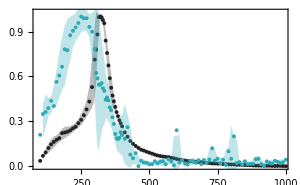
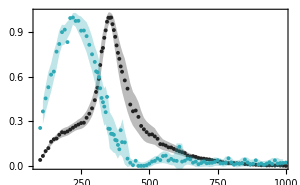
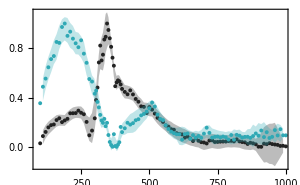

```mathematica
pntSize = 5{1,1};
pntFillOpacity = {.75,.6};
pntOpacity = {1,1};
Table[Show[MapThread[{ListLinePlot[(MovingAverage[#,3]&/@confInter[rescaler[AGAdata3[#1,mechCondition]],AGAdata3["numbers",mechCondition]]),Filling->{1->{2}},PlotStyle->{Opacity[0]},FillingStyle->Directive@{#2,Opacity[0.3]},ImageSize->300,opts],
ListPlot[rescaler[AGAdata3[#1,mechCondition]][[;;,{1,2}]],PlotStyle->{#2,Opacity[1]},PlotMarkers->{Automatic,AbsolutePointSize[4]}]}&,
{{"laser1T","nerve1T"},{hexToRGB["#222222"],hexToRGB["#2FA9B5"]},
{"Circle","Circle"},
pntSize,pntFillOpacity,{0,0},pntOpacity}]],{mechCondition,{"quies","wsso","sso"}}]
```

```mathematica
pntSize = 2{1,1};
pntFillOpacity = {.7,0.6};
pntOpacity = {1,1};
confIntervalsOpacity = {0.2,0.3};
pointEdgeThickness = 0.8{1,1};

dat = AGAdata3;
aga1T=Table[Show[MapThread[{ListLinePlot[(MovingAverage[#,3]&/@confInter[rescaler[dat[#1,mechCondition]],dat["numbers",mechCondition]]),Filling->{1->{2}},PlotStyle->{Opacity[0]},FillingStyle->Directive@{#2,Opacity[#8]},opts],
ListPlot[rescaler[dat[#1,mechCondition]][[;;,{1,2}]],PlotStyle->{#2,Opacity[1]},Joined->True,PlotMarkers->{fm3[#3,#4,#5,#6,#7]}]}&,
{{"laser1T","nerve1T"},{hexToRGB["#222222"],hexToRGB["#2FA9B5"]},
{"Circle","Circle"},
pntSize,pntFillOpacity,pointEdgeThickness,pntOpacity,confIntervalsOpacity}]],{mechCondition,{"quies","wsso","sso"}}];
aga2T=Table[Show[MapThread[{ListLinePlot[(MovingAverage[#,3]&/@confInter[rescaler[dat[#1,mechCondition]],dat["numbers",mechCondition]]),Filling->{1->{2}},PlotStyle->{Opacity[0]},FillingStyle->Directive@{#2,Opacity[#8]},opts],
ListPlot[rescaler[dat[#1,mechCondition]][[;;,{1,2}]],PlotStyle->{#2,Opacity[1]},Joined->True,PlotMarkers->{fm3[#3,#4,#5,#6,#7]}]}&,
{{"laser2T","nerve2T"},{hexToRGB["#222222"],hexToRGB["#007C91"]},
{"Circle","Circle"},
pntSize,pntFillOpacity,pointEdgeThickness,pntOpacity,confIntervalsOpacity}]],{mechCondition,{"quies","wsso","sso"}}];
aae1T=Table[Show[MapThread[{ListLinePlot[(MovingAverage[#,3]&/@confInter[rescaler[AAEdata[#1,mechCondition]],AAEdata["numbers",mechCondition]]),Filling->{1->{2}},PlotStyle->{Opacity[0]},FillingStyle->Directive@{#2,Opacity[#8]},opts],
ListPlot[rescaler[MovingAverage[AAEdata[#1,mechCondition],5]][[;;,{1,2}]],PlotStyle->{#2,Opacity[1]},Joined->True,PlotMarkers->{fm3[#3,#4,#5,#6,#7]}]}&,
{{"laser1T","nerve1T"},{hexToRGB["#222222"],hexToRGB["#F0B14A"]},
{"Circle","Circle"},
pntSize,pntFillOpacity,pointEdgeThickness,pntOpacity,confIntervalsOpacity}]],{mechCondition,{"quies","wsso","sso"}}];
aae2T=Table[Show[MapThread[{ListLinePlot[(MovingAverage[#,3]&/@confInter[rescaler[AAEdata[#1,mechCondition]],AAEdata["numbers",mechCondition]]),Filling->{1->{2}},PlotStyle->{Opacity[0]},FillingStyle->Directive@{#2,Opacity[#8]},opts],
ListPlot[rescaler[MovingAverage[AAEdata[#1,mechCondition],5]][[;;,{1,2}]],PlotStyle->{#2,Opacity[1]},Joined->True,PlotMarkers->{fm3[#3,#4,#5,#6,#7]}]}&,
{{"laser2T","nerve2T"},{hexToRGB["#222222"],hexToRGB["#D89216"]},
{"Circle","Circle"},
pntSize,pntFillOpacity,pointEdgeThickness,pntOpacity,confIntervalsOpacity}]],{mechCondition,{"quies","wsso","sso"}}];
cqu1T=Table[Show[MapThread[{ListLinePlot[(MovingAverage[#,3]&/@confInter[rescaler[CQUdata[#1,mechCondition]],CQUdata["numbers",mechCondition]]),Filling->{1->{2}},PlotStyle->{Opacity[0]},FillingStyle->Directive@{#2,Opacity[#8]},opts],
ListPlot[rescaler[CQUdata[#1,mechCondition]][[;;,{1,2}]],PlotStyle->{#2,Opacity[1]},Joined->True,PlotMarkers->{fm3[#3,#4,#5,#6,#7]}]}&,
{{"laser1T","nerve1T"},{hexToRGB["#222222"],hexToRGB["#B89AFF"]},
{"Circle","Circle"},
pntSize,pntFillOpacity,pointEdgeThickness,pntOpacity,confIntervalsOpacity}]],{mechCondition,{"quies","wsso","sso"}}];
cqu2T=Table[Show[MapThread[{ListLinePlot[(MovingAverage[#,3]&/@confInter[rescaler[CQUdata[#1,mechCondition]],CQUdata["numbers",mechCondition]]),Filling->{1->{2}},PlotStyle->{Opacity[0]},FillingStyle->Directive@{#2,Opacity[#8]},opts],
ListPlot[rescaler[CQUdata[#1,mechCondition]][[;;,{1,2}]],PlotStyle->{#2,Opacity[1]},Joined->True,PlotMarkers->{fm3[#3,#4,#5,#6,#7]}]}&,
{{"laser2T","nerve2T"},{hexToRGB["#222222"],hexToRGB["#825FDD"]},
{"Circle","Circle"},
pntSize,pntFillOpacity,pointEdgeThickness,pntOpacity,confIntervalsOpacity}]],{mechCondition,{"quies","wsso","sso"}}];

fig1Plots= {aga1T[[#]],aga2T[[#]],aae1T[[#]],aae2T[[#]],cqu1T[[#]],cqu2T[[#]]}&/@Range[3];
```

```mathematica
plotGrid[
fig1Plots,

ImageSize->165*3.78,
ItemSize->{1.1{1,1,1,1,1,1}(* columns*),{1,1,1}(* rows*)},
Spacings->{{0,20,0,20,0}(*columns separation*),{0,0,0}(* row separation*)},
"HideOuterTickLabels"->None,
Method->{"FixFrameTicks"->False,"AllCustomTicks"->Automatic}
]
Export[expDir<>"figure_1.pdf",%,ImageResolution->200]
```

-Graphics-

C:\Users\hadif\Proton Drive\c.a.alampounti\My files\Uni\UCL\Projects\02_DP Theory paper\images\article figures\Nature submission 2\raw_svg_figures\figure_1.pdf

```mathematica
Export[expDir<>"figure_1.pdf",%,ImageResolution->200]
```

C:\Users\hadif\Proton Drive\c.a.alampounti\My files\Uni\UCL\Projects\02_DP Theory paper\images\article figures\Nature submission 2\raw_svg_figures\figure_1.pdf

### Version 2 - All species, Anopheles highlight

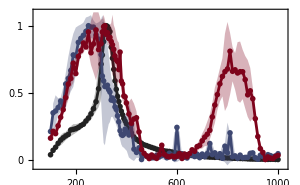
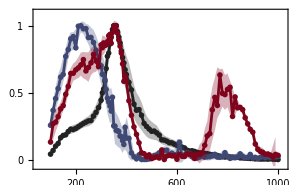
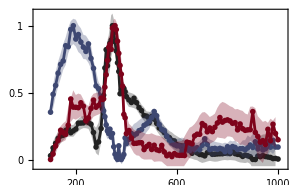

```mathematica
aga=Table[Show[MapThread[{ListLinePlot[(MovingAverage[#,3]&/@confInter[rescaler[AGAdata3[#1,mechCondition]],AGAdata3["numbers",mechCondition]]),Filling->{1->{2}},PlotStyle->{Opacity[0]},FillingStyle->Directive@{#2,Opacity[0.3]},opts],
ListPlot[rescaler[AGAdata3[#1,mechCondition]][[;;,{1,2}]],PlotStyle->{#2,Opacity[1]},Joined->True,PlotMarkers->{fm3[#3,#4,#5,#6,#7]}]}&,
{{"laser1T","nerve1T","nerve2T"},(*{Black,blue,RGBColor@@({170,021,041}/255)}*){hexToRGB["#222222"],Darker@blue(*hexToRGB["5e3c99"(*"#007C91"*)(*"#4A9EA1"*)]*),Darker@red(*hexToRGB["fdb863"(*"#F0B14A"*)(*"#009E73"*)(*"#C59E41"*)]*)},
{"Circle","Circle","UpTriangle"},
5{1,1,1},{0.6,.5,0.5},{0,1,1},{1,1,1}}]],

{mechCondition,{"quies","wsso","sso"}}]
```

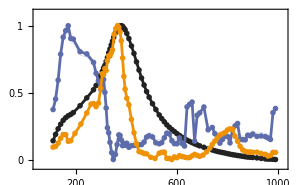
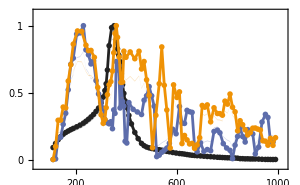
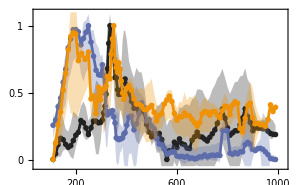

```mathematica
aae=Table[Show[MapThread[{ListLinePlot[(MovingAverage[#,3]&/@confInter[rescaler[AAEdata[#1,mechCondition]],AAEdata["numbers",mechCondition]]),Filling->{1->{2}},PlotStyle->{Opacity[0]},FillingStyle->Directive@{#2,Opacity[0.3]},opts],
ListPlot[rescaler[MovingAverage[AAEdata[#1,mechCondition],3]][[;;,{1,2}]],PlotStyle->{#2,Opacity[1]},Joined->True,PlotMarkers->{fm3[#3,#4,#5,#6,#7]}]}&,
{{"laser1T","nerve1T","nerve2T"},(*{Black,blue,RGBColor@@({170,021,041}/255)}*){hexToRGB["#222222"],blue(*hexToRGB["#2166ac"(*"#4A9EA1"*)]*),orange(*hexToRGB["#b2182b"(*"#009E73"*)(*"#C59E41"*)]*)}(*{hexToRGB["#222222"],hexToRGB["#7D70A0"],hexToRGB["#B05C3C"(*"#009E73"*)(*"#C59E41"*)]}*),{"Circle","Circle","UpTriangle"},4{1,1,1},{0.4,.4,.6},{0,1,1},{1,1,1}}]],

{mechCondition,{"quies","wsso","sso"}}]
```

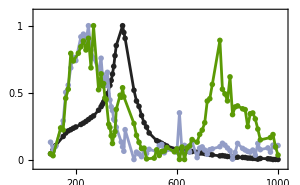
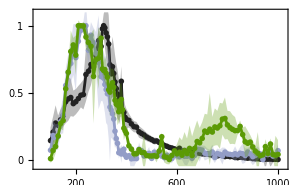
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
cqu=Table[Show[MapThread[{ListLinePlot[(confInter[rescaler[CQUdata[#1,mechCondition]],CQUdata["numbers",mechCondition]]),Filling->{1->{2}},PlotStyle->{Opacity[0]},FillingStyle->Directive@{#2,Opacity[0.3]},opts],
ListPlot[rescaler[CQUdata[#1,mechCondition]][[;;,{1,2}]],PlotStyle->{#2,Opacity[1]},Joined->True,PlotMarkers->{fm3[#3,#4,#5,#6,#7]}]}&,
{{"laser1T","nerve1T","nerve2T"},(*{Black,blue,RGBColor@@({170,021,041}/255)}*){hexToRGB["#222222"],Lighter@blue(*hexToRGB["#1f78b4"]*),green(*Darker@hexToRGB["#1b7837"]*)},{"Circle","Circle","UpTriangle"},4{1,1,1},{0.4,.4,.6},{0,1,1},{1,1,1}}]],

{mechCondition,{"quies","wsso","sso"}}]
```

```mathematica
plotGrid[{aga,aae,cqu}ᵀ,
ImageSize->165*3.78,Spacings->{{20,20}(*columns separation*),{0,0}(* row separation*)},ItemSize->{{GoldenRatio,1,1}(* columns*),{1,1,1}(* rows*)}]
Export[expDir<>"figure_1c.pdf",%,ImageResolution->200]
```

-Graphics-

C:\Users\hadif\Proton Drive\c.a.alampounti\My files\Uni\UCL\Projects\02_DP Theory paper\images\article figures\Nature submission 2\raw_svg_figures\figure_1c.pdf

### Version 3 - Just Anopheles A

```mathematica
opts={Frame->True,
FrameTicks->{{fticksY,None},{fticksX,None}},
FrameStyle->Directive@{(*AbsoluteThickness[1],*)Black, FontSize->8,FontFamily->"Helvetica"},
LabelStyle->Directive@{(*Black,AbsoluteThickness[1],*)Black, FontSize->8,FontFamily->"Helvetica"},
PlotRange->{{50,1020},{-0.05,1.1}},
ImageSize->300};

pntSize = 3{1,1};
pntFillOpacity = {.7,0.6};
pntOpacity = {1,1};
confIntervalsOpacity = {0.2,0.3};
pointEdgeThickness = 0.8{1,1};


dat = AGAdata3;
aga1T=Table[Show[MapThread[{ListLinePlot[(MovingAverage[#,3]&/@confInter[rescaler[dat[#1,mechCondition]],dat["numbers",mechCondition]]),Filling->{1->{2}},PlotStyle->{Opacity[0]},FillingStyle->Directive@{#2,Opacity[#8]},opts],
ListPlot[rescaler[dat[#1,mechCondition]][[;;,{1,2}]],PlotStyle->{#2,Opacity[1]},Joined->True,PlotMarkers->{fm3[#3,#4,#5,#6,#7]}]}&,
{{"laser1T","nerve1T"},{hexToRGB["#222222"],snsDeep[[1]]},
{"Circle","Circle"},
pntSize,pntFillOpacity,pointEdgeThickness,pntOpacity,confIntervalsOpacity}]],{mechCondition,{"quies","wsso","sso"}}];
aga2T=Table[Show[MapThread[{ListLinePlot[(MovingAverage[#,3]&/@confInter[rescaler[dat[#1,mechCondition]],dat["numbers",mechCondition]]),Filling->{1->{2}},PlotStyle->{Opacity[0]},FillingStyle->Directive@{#2,Opacity[#8]},opts],
ListPlot[rescaler[dat[#1,mechCondition]][[;;,{1,2}]],PlotStyle->{#2,Opacity[1]},Joined->True,PlotMarkers->{fm3[#3,#4,#5,#6,#7]}]}&,
{{"laser2T","nerve2T"},{hexToRGB["#222222"],(*hexToRGB["#CC3377"]*)snsDeep[[4]]},
{"Circle","Circle"},
pntSize,pntFillOpacity,pointEdgeThickness,pntOpacity,confIntervalsOpacity}]],{mechCondition,{"quies","wsso","sso"}}];
```

```mathematica
plotGrid[{
{aga1T[[1]],aga2T[[1]]},
{aga1T[[2]],aga2T[[2]]},
{aga1T[[3]],aga2T[[3]]}},

ImageSize->165*3.78/2,
ItemSize->{GoldenRatio{1,1}(* columns*),{1,1,1}(* rows*)},(*,
Spacings->{{0,20,0,20,0}(*columns separation*),{0,0,0}(* row separation*)},*)
Method->{"FixFrameTicks"->False,"AllCustomTicks"->Automatic}]
```

-Graphics-

```mathematica
Export[expDir<>"figure_1_justAnopheles.pdf",%,ImageResolution->200]
```

C:\Users\hadif\Proton Drive\c.a.alampounti\My files\Uni\UCL\Projects\02_DP Theory paper\images\article figures\Nature submission 2\raw_svg_figures\figure_1_justAnopheles.pdf

### Version 3 - Just Anopheles B

```mathematica
start = 5*4000;
len = 500;
plotRangeVal = 1{-.8,0.3};
{color1T,color2T,color2TPoints} = {snsDeep[[1]],snsDeep[[4]],hexToRGB["#CC3377"]};

blendRatio = 0.36;
{c1,c2,c3} =Blend[{#,Gray},blendRatio]&/@{red,blue,green};
```

#### QUIES case

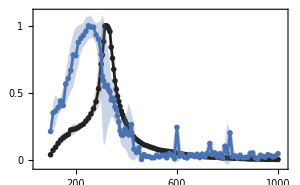
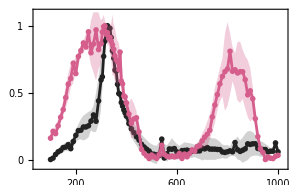

```mathematica
{aga1T[[1]],aga2T[[1]]}
```

UNHASH IF YOU WANT TO FIND THEM ANEW

```mathematica
(*desiredFreqs1T = Sort@{260,270,350,510}; (* 250 Hz is the normalisation peak *)
desiredFreqs2T = Sort@{350,810};(* 355 Hz is the normalisation peak *)

existingFreqs1T =Select[freqs1T,MemberQ[desiredFreqs1T,#]&];
existingFreqs2T =Select[freqs2T,MemberQ[desiredFreqs2T,#]&];

foundExpNum1T = Select[Keys[Select[freqMap,MemberQ[existingFreqs1T,ToExpression@#]&]],OddQ[#]&];
foundExpNum2T = Select[Keys[Select[freqMap,MemberQ[existingFreqs2T,ToExpression@#]&]],EvenQ[#]&];

foundFiles1T=Flatten[Position[ToExpression[StringCases[nervefiles1T,DigitCharacter..][[;;,-1]]],#]&/@foundExpNum1T];
foundFiles2T=Flatten[Position[ToExpression[StringCases[nervefiles2T,DigitCharacter..][[;;,-1]]],#]&/@foundExpNum2T];

Grid[{Style[#,12,Bold]&/@{"Tone","Freqs Requested","Freqs Found"},
{"1T",desiredFreqs1T,existingFreqs1T},
{"2T",desiredFreqs2T,existingFreqs2T}},Dividers->{{False,True}, {False,True}}]

nervefiles1T[[foundFiles1T]]
nervefiles2T[[foundFiles2T]]*)
```

```mathematica
{nerve1Tquies260Hz,nerve1Tquies270Hz,nerve1Tquies350Hz,nerve1Tquies510Hz} =Fold[HighpassFilter,readMyFile[#][[;;,2]],2π/sRate{60,60,60}]&/@{"M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito31\\set_1\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT13_2023-03-20_No 001_M_AGA_Kisumu_ZT13_2023-03-20_No 001_Nerve_a_017_(033).txt","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito31\\set_1\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT13_2023-03-20_No 001_M_AGA_Kisumu_ZT13_2023-03-20_No 001_Nerve_a_018_(035).txt","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito31\\set_1\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT13_2023-03-20_No 001_M_AGA_Kisumu_ZT13_2023-03-20_No 001_Nerve_a_031_(061).txt","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito31\\set_1\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT13_2023-03-20_No 001_M_AGA_Kisumu_ZT13_2023-03-20_No 001_Nerve_a_052_(103).txt"};

{nerve2Tquies350Hz,nerve2Tquies810Hz} = Fold[HighpassFilter,readMyFile[#][[;;,2]],2π/sRate{60,60,60}]&/@{"M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito31\\set_1\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT13_2023-03-20_No 001_M_AGA_Kisumu_ZT13_2023-03-20_No 001_Nerve_b_031_(062).txt","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito31\\set_1\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT13_2023-03-20_No 001_M_AGA_Kisumu_ZT13_2023-03-20_No 001_Nerve_b_082_(164).txt"};
```

```mathematica
Grid@{{ ListLinePlot[nerve1Tquies260Hz[[start;;start+len270]] ,Axes->False,PlotRange->Full,FrameTicks->None,PlotStyle->color1T,opts ],ListLinePlot[nerve2Tquies350Hz[[start;;start+len810]]-0.1,Axes->False,PlotRange->{-1.6,.5},FrameTicks->None,PlotStyle->color2T,opts ]},
{ ListLinePlot[nerve1Tquies510Hz[[start;;start+len270]] ,Axes->False,PlotRange->Full,FrameTicks->None,PlotStyle->color1T,opts ],ListLinePlot[nerve2Tquies810Hz[[start;;start+len810]]-0.1,Axes->False,PlotRange->{-1.6,.5},FrameTicks->None,PlotStyle->color2T,opts ]}}
quiesMin2T
```

Part::span: 20000;;20000+len270 is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: {0.026416,0.0110594,0.0141036,0.044548,0.0612928,0.021538,0.0702838,0.0428299,0.0396763,0.0198225,0.0609686,0.0441142,0.0745602,0.0592056,0.0973502,0.0972943,«20»,-0.0214245,-0.0351831,-0.015442,-0.0277004,0.00884134,-0.0202172,-0.0492757,-0.0310345,-0.0187937,-0.0524536,-0.0312133,-0.0403733,-0.00683328,-0.0236936,«83951»}⟦«1»⟧ is not a list of numbers or pairs of numbers.

Part::span: 20000;;20000+len810 is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

General::stop: Further output of Part::span will be suppressed during this calculation.

ListLinePlot::lpn: -0.1+{0.187231,0.222427,0.366073,0.396764,0.322194,0.319358,0.29675,0.281866,0.279098,0.248942,0.247792,0.240441,0.222484,0.221314,0.220026,0.208114,«19»,0.734636,0.73634,0.685915,0.617156,0.58486,0.517323,0.365641,0.215411,0.0451298,-0.134407,-0.294203,-0.451261,-0.622082,-0.754972,-0.831631,«83951»}⟦«1»⟧ is not a list of numbers or pairs of numbers.

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: {0.031364,0.0363554,-0.0104494,-0.000750004,0.00735331,-0.0180397,-0.0145286,-0.035313,-0.0103933,-0.02357,-0.0108425,-0.0180114,-0.0128772,0.0258599,0.0278995,0.0177415,«20»,0.0203098,0.00567621,0.0398418,0.0327062,0.0332696,0.0765317,0.0816922,0.077651,0.119408,0.0910624,0.070215,0.069265,0.066712,0.0535561,«83951»}⟦«1»⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

quiesMin2T

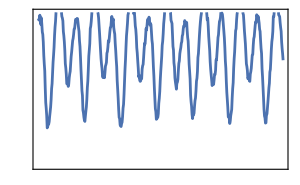
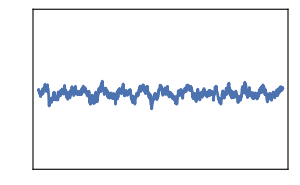
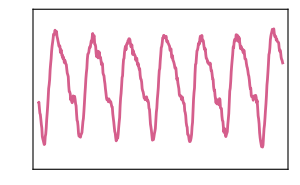
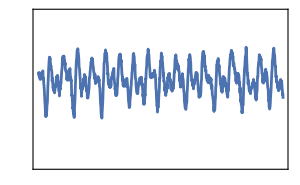
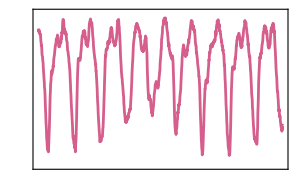

```mathematica
quiesMin1T=Differences[MinMax[nerve1Tquies260Hz[[start;;start+5len]]]][[1]];
quiesMin2T=Differences[MinMax[nerve2Tquies350Hz[[start;;start+5len]]]][[1]];
len270 = 500;
{len510,offset510} = {1000,-500};
{len810,offset810}= {500,1000};
{{nquies270 = ListLinePlot[nerve1Tquies270Hz[[start;;start+len270]]/quiesMin1T ,Axes->False,PlotRange->plotRangeVal,FrameTicks->None,PlotStyle->color1T,opts ],
nquies510 = ListLinePlot[nerve1Tquies510Hz[[start+offset510;;start+offset510+len510]]/quiesMin1T -0.3,Axes->False,PlotRange->plotRangeVal,FrameTicks->None,PlotStyle->color1T,opts ],
nquies810 = ListLinePlot[nerve2Tquies810Hz[[start+offset810;;start+offset810+len810]]/quiesMin2T-0.2,Axes->False,PlotRange->plotRangeVal,FrameTicks->None,PlotStyle->color2T,opts ]},
{nquies1T350Hz = ListLinePlot[nerve1Tquies350Hz[[start+offset510;;start+offset510+len510]]/quiesMin1T -0.2,Axes->False,PlotRange->plotRangeVal,FrameTicks->None,PlotStyle->color1T,opts ],
nquies2T350Hz = ListLinePlot[nerve2Tquies350Hz[[start;;start+len510]]/quiesMin2T -0.1,Axes->False,PlotRange->plotRangeVal,FrameTicks->None,PlotStyle->color2T,opts ]}}
```

```mathematica
(*nerve2Tquies200Hz = readMyFile["M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito31\\set_1\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT13_2023-03-20_No 001_M_AGA_Kisumu_ZT13_2023-03-20_No 001_Nerve_b_012_(024).txt"];
laser2Tquies810Hz =readMyFile["M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito31\\set_1\\Laser\\healthy_files\\M_AGA_Kisumu_ZT13_2023-03-20_No 001_Laser_b_082_(164).txt"];
nerve1Tquies270Hz = readMyFile["M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito31\\set_1\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT13_2023-03-20_No 001_M_AGA_Kisumu_ZT13_2023-03-20_No 001_Nerve_a_018_(035).txt"];
nerve2Tquies810Hz =readMyFile["M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito31\\set_1\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT13_2023-03-20_No 001_M_AGA_Kisumu_ZT13_2023-03-20_No 001_Nerve_b_082_(164).txt"];
quiesMin=Abs[Min@Fold[HighpassFilter, nerve2Tquies200Hz[[start;;start+len,2]],2π/sRate{60,60,60}]];
oneTvstwoTScalingAt270vs810Hz = 1.2; (* it is tricky to scale 1T vs 2T in this scenario as the plots are scaled to the maximum peak ~220 Hz for 1T and ~350 Hz for 2T *)
(* here I am providing a relative increase between the two *)

{ListLinePlot[Fold[HighpassFilter, laser2Tquies810Hz[[start;;start+len,2]],2π/sRate{0}]],
nquies270=ListLinePlot[Fold[HighpassFilter,nerve1Tquies270Hz[[start;;start+len,2]],2π/sRate{60,60,60}]/quiesMin oneTvstwoTScalingAt270vs810Hz-0.2,PlotRange->plotRangeVal,Axes->False,FrameTicks->None,opts,PlotStyle->color1T],
nquies810=ListLinePlot[Fold[HighpassFilter,nerve2Tquies810Hz[[start;;start+len,2]],2π/sRate{60,60,60}]/quiesMin-0.2,PlotRange->plotRangeVal,Axes->False,FrameTicks->None,opts,PlotStyle->color2T]}*)
```

#### weak SSO case

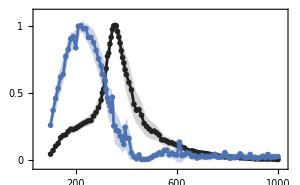
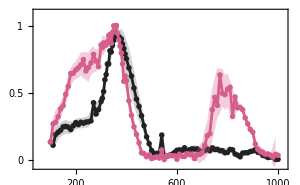

```mathematica
{aga1T[[2]],aga2T[[2]]}
```

UNHASH TO FIND THE FILES - REQUIRES THE MAIN NOTEBOOK

```mathematica
(*desiredFreqs1T = Sort@{220,270,360,510}; (* 190 Hz is the normalisation peak *)
desiredFreqs2T = Sort@{360,810};(* 355 Hz is the normalisation peak *)

existingFreqs1T =Select[freqs1T,MemberQ[desiredFreqs1T,#]&];
existingFreqs2T =Select[freqs2T,MemberQ[desiredFreqs2T,#]&];

foundExpNum1T = Select[Keys[Select[freqMap,MemberQ[existingFreqs1T,ToExpression@#]&]],OddQ[#]&];
foundExpNum2T = Select[Keys[Select[freqMap,MemberQ[existingFreqs2T,ToExpression@#]&]],EvenQ[#]&];

foundFiles1T=Flatten[Position[ToExpression[StringCases[nervefiles1T,DigitCharacter..][[;;,-1]]],#]&/@foundExpNum1T];
foundFiles2T=Flatten[Position[ToExpression[StringCases[nervefiles2T,DigitCharacter..][[;;,-1]]],#]&/@foundExpNum2T];

Grid[{Style[#,12,Bold]&/@{"Tone","Freqs Requested","Freqs Found"},
{"1T",desiredFreqs1T,existingFreqs1T},
{"2T",desiredFreqs2T,existingFreqs2T}},Dividers->{{False,True}, {False,True}}]

nervefiles1T[[foundFiles1T]]
nervefiles2T[[foundFiles2T]]*)
```

```mathematica
{nerve1TwSSO220Hz,nerve1TwSSO270Hz,nerve1TwSSO360Hz,nerve1TwSSO510Hz} =Fold[HighpassFilter,readMyFile[#][[;;,2]],2π/sRate{60,60,60}]&/@{"M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito30\\set_1\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT05_2023-02-21_No 001_Nerve_a_013_(025).txt","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito30\\set_1\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT05_2023-02-21_No 001_Nerve_a_018_(035).txt","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito30\\set_1\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT05_2023-02-21_No 001_Nerve_a_033_(065).txt","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito30\\set_1\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT05_2023-02-21_No 001_Nerve_a_052_(103).txt"};

{nerve2TwSSO360Hz,nerve2TwSSO810Hz} = Fold[HighpassFilter,readMyFile[#][[;;,2]],2π/sRate{60,60,60}]&/@{
"M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito30\\set_1\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT05_2023-02-21_No 001_Nerve_b_033_(066).txt","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito30\\set_1\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT05_2023-02-21_No 001_Nerve_b_082_(164).txt"};
```

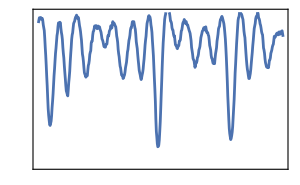
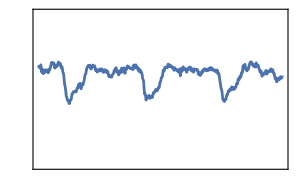
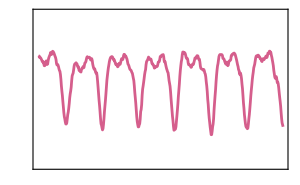
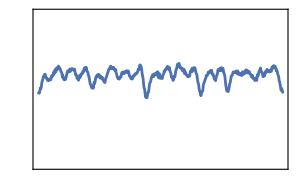
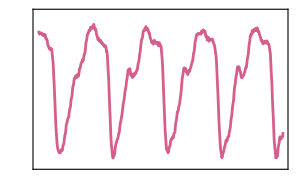

```mathematica
wssoMin1T=Differences[MinMax[nerve1TwSSO220Hz[[start;;start+5len]]]][[1]];
wssoMin2T=Differences[MinMax[nerve2TwSSO360Hz[[start;;start+5len]]]][[1]];
len270 = 500;
{len510,offset510} = {500,-3450};
len810= 500;
{{nwsso270 = ListLinePlot[nerve1TwSSO270Hz[[start;;start+len270]]/wssoMin1T +0.1,Axes->False,PlotRange->plotRangeVal,FrameTicks->None,PlotStyle->color1T,opts ],
nwsso510 = ListLinePlot[nerve1TwSSO510Hz[[start+offset510;;start+offset510+len510]]/wssoMin1T -0.1,Axes->False,PlotRange->plotRangeVal,FrameTicks->None,PlotStyle->color1T,opts ],
nwsso810 = ListLinePlot[nerve2TwSSO810Hz[[start;;start+len810]]/wssoMin2T-0.1,Axes->False,PlotRange->plotRangeVal,FrameTicks->None,PlotStyle->color2T,opts ]},
nwsso3601T =  ListLinePlot[nerve1TwSSO360Hz[[start;;start+len810]]/wssoMin1T-0.1,Axes->False,PlotRange->plotRangeVal,FrameTicks->None,PlotStyle->color1T,opts ],
nwsso3602T =  ListLinePlot[nerve2TwSSO360Hz[[start;;start+len810]]/wssoMin2T-0.1,Axes->False,PlotRange->plotRangeVal,FrameTicks->None,PlotStyle->color2T,opts ]}
```

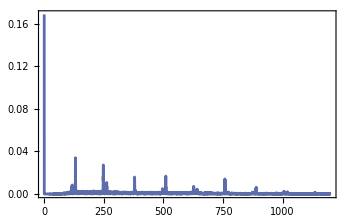
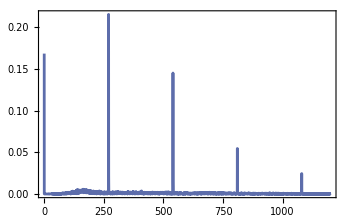

```mathematica
ListLinePlot[fourier[#,sRate,1200]]&/@{nerve1TwSSO510Hz,nerve2TwSSO810Hz}
```

#### SSO case

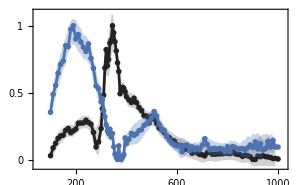
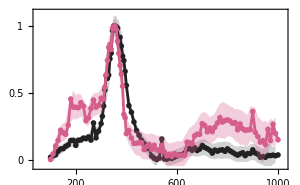

```mathematica
{aga1T[[3]],aga2T[[3]]}
```

UNHASH TO FIND THE FILES - REQUIRES THE MAIN NOTEBOOK

```mathematica
(*desiredFreqs1T = Sort@{190,270,355,490}(*{190,270,510}*); (* 190 Hz is the normalisation peak *)
desiredFreqs2T = Sort@{355,810};(* 355 Hz is the normalisation peak *)

existingFreqs1T =Select[freqs1T,MemberQ[desiredFreqs1T,#]&];
existingFreqs2T =Select[freqs2T,MemberQ[desiredFreqs2T,#]&];

foundExpNum1T = Select[Keys[Select[freqMap,MemberQ[existingFreqs1T,ToExpression@#]&]],OddQ[#]&];
foundExpNum2T = Select[Keys[Select[freqMap,MemberQ[existingFreqs2T,ToExpression@#]&]],EvenQ[#]&];

foundFiles1T=Flatten[Position[ToExpression[StringCases[nervefiles1T,DigitCharacter..][[;;,-1]]],#]&/@foundExpNum1T];
foundFiles2T=Flatten[Position[ToExpression[StringCases[nervefiles2T,DigitCharacter..][[;;,-1]]],#]&/@foundExpNum2T];

Grid[{Style[#,12,Bold]&/@{"Tone","Freqs Requested","Freqs Found"},
{"1T",desiredFreqs1T,existingFreqs1T},
{"2T",desiredFreqs2T,existingFreqs2T}},Dividers->{{False,True}, {False,True}}]*)

nervefiles1T[[foundFiles1T]]
nervefiles2T[[foundFiles2T]]
```

Part::pkspec1: The expression foundFiles1T cannot be used as a part specification.

nervefiles1T⟦foundFiles1T⟧

Part::pkspec1: The expression foundFiles2T cannot be used as a part specification.

nervefiles2T⟦foundFiles2T⟧

```mathematica
{nerve1TSSO190Hz,nerve1TSSO270Hz,nerve1TSSO355Hz,nerve1TSSO510Hz} =Fold[HighpassFilter,readMyFile[#][[;;,2]],2π/sRate{60,60,60}]&/@{"N:\\Storage Files\\UCL Data\\Anopheles\\Mosquito 5\\set_1\\Nerve\\Nerve_a_010_(019).txt","N:\\Storage Files\\UCL Data\\Anopheles\\Mosquito 5\\set_1\\Nerve\\Nerve_a_018_(035).txt","N:\\Storage Files\\UCL Data\\Anopheles\\Mosquito 5\\set_1\\Nerve\\Nerve_a_032_(063).txt","N:\\Storage Files\\UCL Data\\Anopheles\\Mosquito 5\\set_1\\Nerve\\Nerve_a_050_(099).txt"};
(*{"M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito26\\set_2\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT12_2023-02-16_No 001_Nerve_a_010_(019).txt","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito26\\set_2\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT12_2023-02-16_No 001_Nerve_a_018_(035).txt","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito26\\set_2\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT12_2023-02-16_No 001_Nerve_a_052_(103).txt"};*)

{nerve2TSSO355Hz,nerve2TSSO810Hz} = Fold[HighpassFilter,readMyFile[#][[;;,2]],2π/sRate{60,60,60}]&/@{"N:\\Storage Files\\UCL Data\\Anopheles\\Mosquito 5\\set_1\\Nerve\\Nerve_b_032_(064).txt","N:\\Storage Files\\UCL Data\\Anopheles\\Mosquito 5\\set_1\\Nerve\\Nerve_b_082_(164).txt"};
(*{"M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito26\\set_2\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT12_2023-02-16_No 001_Nerve_b_032_(064).txt","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito26\\set_2\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT12_2023-02-16_No 001_Nerve_b_082_(164).txt"};*)
```

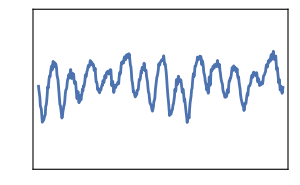
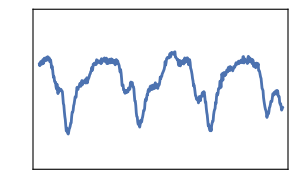
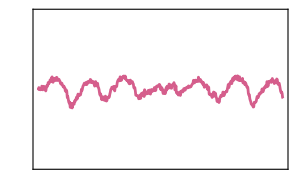
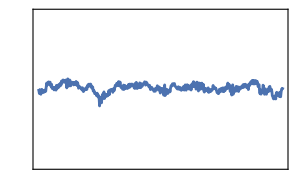
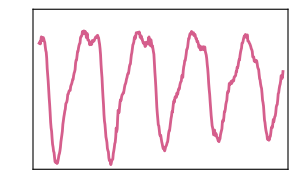

```mathematica
start = 5*4000;
len = 500;
offset =500;
yoffset=-0.2;
ssoMin1T=Differences[MinMax[nerve1TSSO190Hz[[start;;start+5len]]]][[1]];
ssoMin2T=Differences[MinMax[nerve2TSSO355Hz[[start;;start+5len]]]][[1]];

{{nsso270=ListLinePlot[nerve1TSSO270Hz[[start+offset;;start+len+offset]]/ssoMin1T+yoffset,PlotRange->plotRangeVal,Axes->False,FrameTicks->None,PlotStyle->color1T,opts],
nsso510 = ListLinePlot[nerve1TSSO510Hz[[start+offset;;start+len+offset]]/ssoMin1T+yoffset,PlotRange->plotRangeVal,Axes->False,FrameTicks->None,PlotStyle->color1T,opts]
(* NOTE: I am background removing the 540 Hz which dominates as crosstalk here!!! *),
nsso810=ListLinePlot[(nerve2TSSO810Hz-0.107Table[1.Cos[2π 540 t + 5π/24],{t,0,4.2,1/sRate}])[[start;;start+len]]/ssoMin2T-0.25,PlotRange->plotRangeVal,Axes->False,FrameTicks->None,PlotStyle->color2T,opts]},
{nsso3551T = ListLinePlot[nerve1TSSO355Hz[[start+offset;;start+len+offset]]/ssoMin1T-0.25,PlotRange->plotRangeVal,Axes->False,FrameTicks->None,PlotStyle->color1T,opts],
nsso3552T = ListLinePlot[nerve2TSSO355Hz[[start+offset;;start+len+offset]]/ssoMin2T+yoffset,PlotRange->plotRangeVal,Axes->False,FrameTicks->None,PlotStyle->color2T,opts]}}
```

```mathematica
Manipulate[{ListLinePlot[{nerve1TSSO190Hz[[start;;start+500]],nerve1TSSO510Hz[[start;;start+500]]},PlotRange->plotRangeVal],
ListLinePlot[(nerve2TSSO810Hz[[15000;;15500]]-0.107Table[1.Cos[2π 540 t + 5π/24],{t,0,4.2,1/sRate}][[15000;;15500]])/ssoMin2T,PlotRange->plotRangeVal,PlotStyle->pink]},{{start,15210},10000,30000,500}]
```

```mathematica
Manipulate[ListLinePlot[fourier[nerve2TSSO810Hz-0.107Table[1.Cos[2π 540 t + ϕ],{t,0,4.2,1/sRate}],sRate,1200][[3;;]],PlotRange->{0,0.107}],{{ϕ,5π/24},0,2π,π/24},Paneled->False]
```

#### Amplitude scaling

```mathematica
Clear[powerInNerve,t]
powerInNerve[data_]:=Block[{t},
t=Fold[HighpassFilter,readMyFile[data,2][[;;40000]],2π/sRate{60,60,60}];
-EstimatedBackground[t,200,Method->{"SNIP",3}]-EstimatedBackground[-t,200,Method->{"SNIP",3}]
]
```

```mathematica
power = powerInNerve[#]&/@nervefiles1T;
```

```mathematica
ampList = Table[{freqs1T[[i]] &/@Range[40000],Range[40000],GaussianFilter[power[[i]],1000]}ᵀ,{i,Length@freqs1T}];
```

```mathematica
{ListPlot3D[Flatten[ampList[[;;,;; ;;500]],1],ColorFunction->"DeepSeaColors",ImageSize->300],
ListDensityPlot[Flatten[ampList[[;;,;; ;;500]],1],ColorFunction->"DeepSeaColors",ImageSize->300,FrameLabel->{"Stimulus Frequency (Hz)","Intensity (arb)"},PlotLabel->"1T SSO animal"]}
```

ListPlot3D::arrayerr: {} must be a valid array or a list of valid arrays.

{ListPlot3D[{},ColorFunction→DeepSeaColors,ImageSize→300],-Graphics-}

```mathematica
ridgeDataSSO1T = Import["N:\\Storage Files\\UCL Data\\Anopheles\\Mosquito 5\\set_1\\0_overview\\M_AGA_G3_ZT13_2025-08-14_No 001_Laser and Nerve_overview_1T.txt","RawJSON"];
ridgeDataSSO2T = Import["N:\\Storage Files\\UCL Data\\Anopheles\\Mosquito 5\\set_1\\0_overview\\M_AGA_G3_ZT13_2025-08-14_No 001_Laser and Nerve_overview_2T.txt","RawJSON"];
rData1T = MovingAverage[#,4]&/@ridgeDataSSO1T["laser"][[;;,;;,{1,3}]];
rData1TN = MovingAverage[#,4]&/@ridgeDataSSO1T["nerve"][[;;,;;,{1,3}]];
rData2TNS = MovingAverage[#,4]&/@ridgeDataSSO2T["nerve"][[;;,;;,{1,3}]];

ridgeDataQUIES1T = Import["M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito31\\set_1\\0_overview\\M_AGA_Kisumu_ZT13_2023-03-20_No 001_Laser and Nerve_overview_1T.txt","RawJSON"];
ridgeDataQUIES2T = Import["M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito31\\set_1\\0_overview\\M_AGA_Kisumu_ZT13_2023-03-20_No 001_Laser and Nerve_overview_2T.txt","RawJSON"];

rData1TNQ = MovingAverage[#,4]&/@ridgeDataQUIES1T["nerve"][[;;,;;,{1,3}]];

rData2T = MovingAverage[#,4]&/@ridgeDataQUIES2T["laser"][[;;,;;,{1,3}]];
rData2TN = MovingAverage[#,4]&/@ridgeDataQUIES2T["nerve"][[;;,;;,{1,3}]];
```

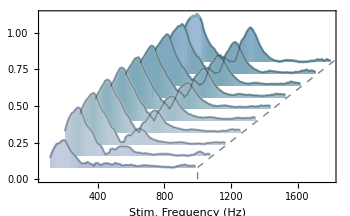
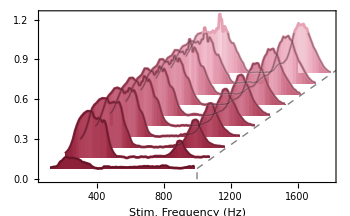

```mathematica
hoffset = 90;
voffset = 0.08;

ridge1T = Table[MapAt[#+(i-1) hoffset&,rData1TN[[i]]+ voffset (i)-Min[rData1TN[[i,;;,2]]] ,{All,1}],{i,Length@rData1TN}];
ridge2TS = Table[MapAt[#+(i-1) hoffset&,rData2TNS[[i]]+ voffset (i)-Min[rData2TNS[[i,;;,2]]] ,{All,1}],{i,Length@rData2TNS}];

ridge1TQ = Table[MapAt[#+(i-1) hoffset&,rData1TNQ[[i]]+ voffset (i)-Min[rData1TNQ[[i,;;,2]]] ,{All,1}],{i,Length@rData1TNQ}];
ridge2T = Table[MapAt[#+(i-1) hoffset&,rData2TN[[i]]+ voffset (i)-Min[rData2TN[[i,;;,2]]] ,{All,1}],{i,Length@rData2TN}];

ampScale1T=Show[{ListLinePlot[ridge1T,
ColorFunction->"Aquamarine",Frame->{True,False,False,False},FrameLabel->{"Stim. Frequency (Hz)",None},
Epilog->{Dashed,Gray, Line[{{1000,voffset},{1000+(Length@rData1T+1.5)*hoffset,1}}],Line[{{1000,0},{1000,voffset}}]},
Filling->({#->Min[ridge1T[[#]]]}&/@Range[Length@rData1TN]),FrameStyle->Directive[FontSize->8]],
ListLinePlot[ridge1T,PlotStyle->Directive@{Black,Thickness[0.003],Opacity[0.3]},opts]}];


ampScale2T=Show[{ListLinePlot[ridge2T,
ColorFunction->"ValentineTones",Frame->{True,False,False,False},FrameLabel->{"Stim. Frequency (Hz)",None},
Epilog->{Dashed,Gray, Line[{{1000,voffset},{1000+(Length@rData1T+1.5)*hoffset,1}}],Line[{{1000,0},{1000,voffset}}]},Filling->({#->Min[ridge2T[[#]]]}&/@Range[Length@rData2TN]),
FrameStyle->Directive[FontSize->8]],
ListLinePlot[ridge2T,PlotStyle->Directive@{Black,Thickness[0.003],Opacity[0.3]},opts]}];

{ampScale1T,ampScale2T}

(*ampScale2T=ListLinePlot[Table[MapAt[#+i hoffset&,rData2T[[i]]+voffset i ,{All,1}],{i,Length@rData2T}],
ColorFunction->"ValentineTones",Frame->{True,False,False,False},FrameLabel->{"Stim. Frequency (Hz)",None},PlotStyle->Black,
Epilog->{Dashed,Gray, Line[{{1000,0},{1000+(Length@rData2T+1.5)*hoffset,1}}]}, Filling->({#->Min[rData2T[[#]]]+voffset #}&/@Range[Length@rData2T]),FrameStyle->Directive[FontSize->8]]*)
```

0.08

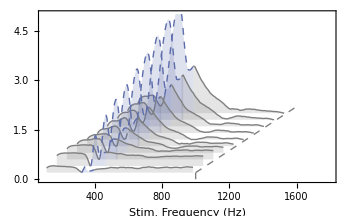
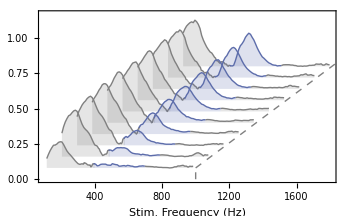
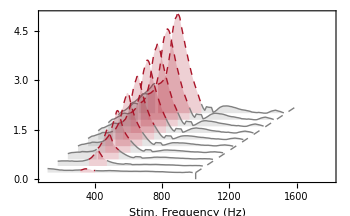
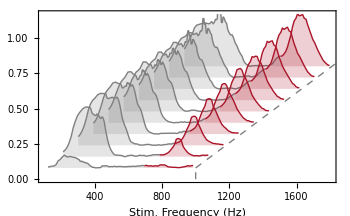

```mathematica
hoffset = 90;
hoffsetL = 60;
voffset = 0.08
voffsetL =0.2;

(* 1T SSO nerve *)
ridge1Ta = Table[MapAt[#+(i-1) hoffset&,Select[rData1TN[[i]],Between[#[[1]],{100,400}] &]+ voffset (i)-Min[rData1TN[[i,;;,2]]] ,{All,1}],{i,Length@rData1TN}];
ridge1Tb = Table[MapAt[#+(i-1) hoffset&,Select[rData1TN[[i]],Between[#[[1]],{390,700}] &]+ voffset (i)-Min[rData1TN[[i,;;,2]]] ,{All,1}],{i,Length@rData1TN}];
ridge1Tc = Table[MapAt[#+(i-1) hoffset&,Select[rData1TN[[i]],Between[#[[1]],{690,1000}] &]+ voffset (i)-Min[rData1TN[[i,;;,2]]] ,{All,1}],{i,Length@rData1TN}];

(* 1T SSO laser *)
ridge1TL   = Table[MapAt[#+(i-1) hoffsetL&,rData1T[[i]]+ voffsetL (i)-Min[rData1T[[i,;;,2]]] ,{All,1}],{i,Length@rData1T}];
ridge1TaL = Table[MapAt[#+(i-1) hoffsetL&,Select[rData1T[[i]],Between[#[[1]],{100,330-5i}] &]+ voffsetL (i)-Min[rData1T[[i,;;,2]]] ,{All,1}],{i,Length@rData1T}];
ridge1TbL = Table[MapAt[#+(i-1) hoffsetL&,Select[rData1T[[i]],Between[#[[1]],{325-5i,400+5i}] &]+ voffsetL (i)-Min[rData1T[[i,;;,2]]] ,{All,1}],{i,Length@rData1T}];
ridge1TcL = Table[MapAt[#+(i-1) hoffsetL&,Select[rData1T[[i]],Between[#[[1]],{390+5i,1000}] &]+ voffsetL (i)-Min[rData1T[[i,;;,2]]] ,{All,1}],{i,Length@rData1T}];

(* 2T SSO nerve *)
ridge2TS = Table[MapAt[#+(i-1) hoffset&,rData2TNS[[i]]+ voffset (i)-Min[rData2TNS[[i,;;,2]]] ,{All,1}],{i,Length@rData2TNS}];
ridge2TaS= Table[MapAt[#+(i-1) hoffset&,Select[rData2TNS[[i]],Between[#[[1]],{100,700}] &]+ voffset (i)-Min[rData2TNS[[i,;;,2]]] ,{All,1}],{i,Length@rData2TNS}];
ridge2TbS = Table[MapAt[#+(i-1) hoffset&,Select[rData2TNS[[i]],Between[#[[1]],{690,1000}] &]+ voffset (i)-Min[rData2TNS[[i,;;,2]]] ,{All,1}],{i,Length@rData2TNS}];

(* 1T QUIES nerve *)
ridge1TaQ = Table[MapAt[#+(i-1) hoffset&,Select[rData1TNQ[[i]],Between[#[[1]],{100,400}] &]+ voffset (i)-Min[rData1TNQ[[i,;;,2]]] ,{All,1}],{i,Length@rData1TNQ}];
ridge1TbQ = Table[MapAt[#+(i-1) hoffset&,Select[rData1TNQ[[i]],Between[#[[1]],{390,700}] &]+ voffset (i)-Min[rData1TNQ[[i,;;,2]]] ,{All,1}],{i,Length@rData1TNQ}];
ridge1TcQ= Table[MapAt[#+(i-1) hoffset&,Select[rData1TNQ[[i]],Between[#[[1]],{690,1000}] &]+ voffset (i)-Min[rData1TNQ[[i,;;,2]]] ,{All,1}],{i,Length@rData1TNQ}];

(* 2T QUIES nerve *)
ridge2T = Table[MapAt[#+(i-1) hoffset&,rData2TN[[i]]+ voffset (i)-Min[rData2TN[[i,;;,2]]] ,{All,1}],{i,Length@rData2TN}];
ridge2Ta = Table[MapAt[#+(i-1) hoffset&,Select[rData2TN[[i]],Between[#[[1]],{100,700}] &]+ voffset (i)-Min[rData2TN[[i,;;,2]]] ,{All,1}],{i,Length@rData2TN}];
ridge2Tb = Table[MapAt[#+(i-1) hoffset&,Select[rData2TN[[i]],Between[#[[1]],{690,1000}] &]+ voffset (i)-Min[rData2TN[[i,;;,2]]] ,{All,1}],{i,Length@rData2TN}];

(* 2T QUIES laser *)
ridge2TL   = Table[MapAt[#+(i-1) hoffsetL&,rData2T[[i]]+ voffsetL (i)-Min[rData2T[[i,;;,2]]] ,{All,1}],{i,Length@rData2T}];
ridge2TaL = Table[MapAt[#+(i-1) hoffsetL&,Select[rData2T[[i]],Between[#[[1]],{100,330-10*i}] &]+ voffsetL (i)-Min[rData2T[[i,;;,2]]] ,{All,1}],{i,Length@rData2T}];
ridge2TbL = Table[MapAt[#+(i-1) hoffsetL&,Select[rData2T[[i]],Between[#[[1]],{325-10i,400+10i}] &]+ voffsetL (i)-Min[rData2T[[i,;;,2]]] ,{All,1}],{i,Length@rData2T}];
ridge2TcL = Table[MapAt[#+(i-1) hoffsetL&,Select[rData2T[[i]],Between[#[[1]],{390+10i,1000}] &]+ voffsetL (i)-Min[rData2T[[i,;;,2]]] ,{All,1}],{i,Length@rData2T}];




ampScale1T=Show[MapThread[
ListLinePlot[#1,
PlotStyle->Directive[#2,AbsoluteThickness[1]],
FrameLabel->{"Stim. Frequency (Hz)",None},
Filling->({#->Min[ridge2T[[#]]]}&/@Range[Length@rData2TN]),
PlotRange->{{100,1800},{0,1.17}},
Frame->{True,False,False,False},
FrameStyle->Directive[Black,FontSize->8],
Epilog->{Dashed,Gray, Line[{{1000,voffset},{1000+(Length@rData1T+1.5)*hoffset,1}}],Line[{{1000,0},{1000,voffset}}]}]&,{{ridge1Ta,ridge1Tb,ridge1Tc},{Gray,col1TN,Gray}}]];

ampScale2T=Show[MapThread[
ListLinePlot[#1,
PlotStyle->Directive[#2,AbsoluteThickness[1]],
FrameLabel->{"Stim. Frequency (Hz)",None},
Filling->({#->Min[ridge2T[[#]]]}&/@Range[Length@rData2TN]),
PlotRange->{{100,1800},{0,1.17}},
Frame->{True,False,False,False},
FrameStyle->Directive[Black,FontSize->8],
Epilog->{Dashed,Gray, Line[{{1000,voffset},{1000+(Length@rData1T+1.5)*hoffset,1}}],Line[{{1000,0},{1000,voffset}}]}]&,{{ridge2Ta,ridge2Tb},{Gray,col2TN}}]];


ampScale1TL=Show[MapThread[
ListLinePlot[#1,
PlotStyle->Directive[#2,AbsoluteThickness[1]],
FrameLabel->{"Stim. Frequency (Hz)",None},
Filling->({#->Min[ridge1TL[[#]]]}&/@Range[Length@rData1T]),
PlotRange->{{100,1800},{0,5}},
Frame->{True,False,False,False},
FrameStyle->Directive[Black,FontSize->8],
Epilog->{Dashed,Gray, Line[{{1000,voffsetL},{1000+(Length@rData1T)*hoffsetL,1.1ridge1TcL[[-1,-1,2]]}}],Line[{{1000,0},{1000,voffsetL}}]}]&,{{ridge1TaL,ridge1TbL,ridge1TcL},{Gray,{col1TN,Dashed},Gray}}]];

ampScale2TL=Show[MapThread[
ListLinePlot[#1,
PlotStyle->Directive[#2,AbsoluteThickness[1]],
FrameLabel->{"Stim. Frequency (Hz)",None},
Filling->({#->Min[ridge2TL[[#]]]}&/@Range[Length@rData2T]),
PlotRange->{{100,1800},{0,5}},
Frame->{True,False,False,False},
FrameStyle->Directive[Black,FontSize->8],
Epilog->{Dashed,Gray, Line[{{1000,voffsetL},{1000+(Length@rData2T)*hoffsetL,1.1ridge2TcL[[-1,-1,2]]}}],Line[{{1000,0},{1000,voffsetL}}]}]&,{{ridge2TaL,ridge2TbL,ridge2TcL},{Gray,{col2TN,Dashed},Gray}}]];

{{ampScale1TL,ampScale1T},{ampScale2TL,ampScale2T}}
```

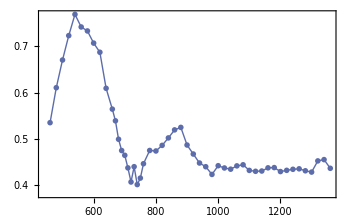

```mathematica
ListLinePlot[MapAt[#+(5-1) hoffset&,testData+ voffset (5)-Min[testData[[;;,2]]] ,{All,1}][[;; ;;2]],PlotMarkers->fm2["Circle",3,1],PlotStyle->{AbsoluteThickness[1],col1TN}]
```

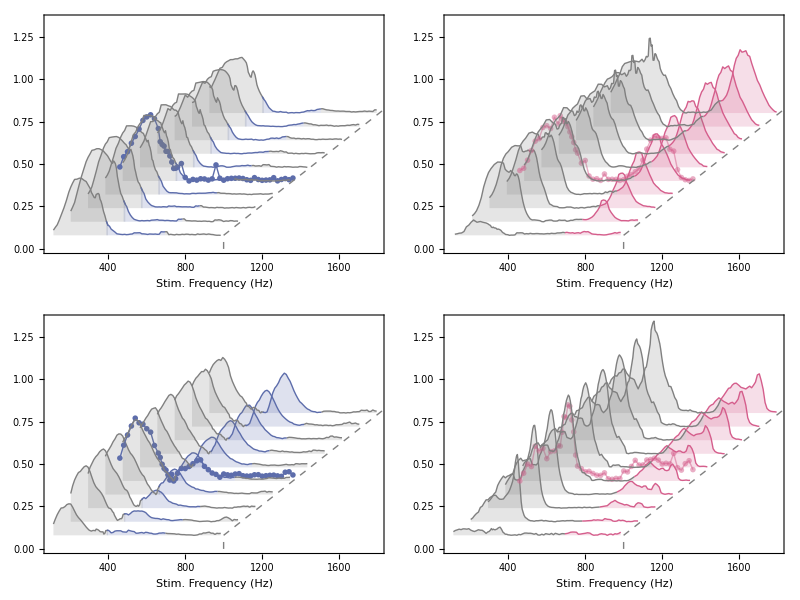

```mathematica
pltRangeRidge=  {{100,1800},{0,1.35}};
pointSizeRidge = 3;
takeEveryXPoints = 2; (*1 for all, 2 for every second...*)

(* 1T SSO nerve *)
testData = MapAt[#*.5Max[ridge1T[[5]][[;;,2]]]&,rescaler[dat["nerve1T","sso"]][[;;,{1,2}]],{All,2}];
testPlot = ListLinePlot[MapAt[#+(5-1) hoffset&,testData+ voffset (5)-Min[testData[[;;,2]]] ,{All,1}][[;; ;;takeEveryXPoints]],PlotMarkers->fm2["Circle",pointSizeRidge,1],PlotStyle->{AbsoluteThickness[1],col1TN}(*,Filling->voffset*5+Min[testData[[;;,2]]]*)];
minFils = Min[#[[;;,2]]]&/@ridge1T;
allplots1TS = MapThread[
ListLinePlot[#1,
PlotStyle->({#,AbsoluteThickness[1]}&/@{Gray,col1TN,Gray}),
FrameLabel->{"Stim. Frequency (Hz)",None},
Filling->Table[i->#2,{i,Length@#1}],
PlotRange->pltRangeRidge,
Frame->{True,False,False,False},
FrameStyle->Directive[Black,FontSize->8],
Epilog->{Dashed,Gray, Line[{{1000,voffset},{1000+(Length@rData1T+1.5)*hoffset,1}}],Line[{{1000,0},{1000,voffset}}]}]&,{{ridge1Ta,ridge1Tb,ridge1Tc}ᵀ,minFils}];
allplots1TS[[5]] =Show[Reverse@{allplots1TS[[5]],testPlot}];

(* 2T SSO nerve *)
testData2TS = MapAt[#*.5Max[ridge2TS[[5]][[;;,2]]]&,rescaler[dat["nerve2T","sso"]][[;;,{1,2}]],{All,2}];
testPlot2TS = ListLinePlot[MapAt[#+(5-1) hoffset&,testData2TS+ voffset (5)-Min[testData2TS[[;;,2]]] ,{All,1}][[;; ;;takeEveryXPoints]],PlotMarkers->fm2["Circle",pointSizeRidge,1],PlotStyle->{AbsoluteThickness[1],color2T,Opacity[0.5]}(*,Filling->voffset*5+Min[testData2TS[[;;,2]]]*)];
minFils2T = Min[#[[;;,2]]]&/@ridge2TS;
allplots2TS = MapThread[
ListLinePlot[#1,
PlotStyle->({#,AbsoluteThickness[1]}&/@{Gray,color2T,Gray}),
FrameLabel->{"Stim. Frequency (Hz)",None},
Filling->Table[i->#2,{i,Length@#1}],
PlotRange->pltRangeRidge,
Frame->{True,False,False,False},
FrameStyle->Directive[Black,FontSize->8],
Epilog->{Dashed,Gray, Line[{{1000,voffset},{1000+(Length@rData2T+1.5)*hoffset,1}}],Line[{{1000,0},{1000,voffset}}]}]&,{{ridge2TaS,ridge2TbS}ᵀ,minFils2T}];
allplots2TS[[5]] =Show[Reverse@{allplots2TS[[5]],testPlot2TS}];

(* 1T quiescent nerve *)
testData1TQ = MapAt[#*.5Max[ridge1TQ[[5]][[;;,2]]]&,rescaler[dat["nerve1T","quies"]][[;;,{1,2}]],{All,2}];
testPlot1TQ = ListLinePlot[MapAt[#+(5-1) hoffset&,testData1TQ+ voffset (5)-Min[testData1TQ[[;;,2]]] ,{All,1}][[;; ;;takeEveryXPoints]],PlotMarkers->fm2["Circle",pointSizeRidge,1],PlotStyle->{AbsoluteThickness[1],col1TN}(*,Filling->voffset*5+Min[testData1TQ[[;;,2]]]*)];
minFils = Min[#[[;;,2]]]&/@ridge1TQ;
allplots1TQ = MapThread[
ListLinePlot[#1,
PlotStyle->({#,AbsoluteThickness[1]}&/@{Gray,col1TN,Gray}),
FrameLabel->{"Stim. Frequency (Hz)",None},
Filling->Table[i->#2,{i,Length@#1}],
PlotRange->pltRangeRidge,
Frame->{True,False,False,False},
FrameStyle->Directive[Black,FontSize->8],
Epilog->{Dashed,Gray, Line[{{1000,voffset},{1000+(Length@rData1T+1.5)*hoffset,1}}],Line[{{1000,0},{1000,voffset}}]}]&,{{ridge1TaQ,ridge1TbQ,ridge1TcQ}ᵀ,minFils}];
allplots1TQ[[5]] =Show[Reverse@{allplots1TQ[[5]],testPlot1TQ}];

(* 2T quiescent nerve *)
testData2T = MapAt[#*.5Max[ridge2T[[5]][[;;,2]]]&,rescaler[dat["nerve2T","quies"]][[;;,{1,2}]],{All,2}];
testPlot2T = ListLinePlot[MapAt[#+(5-1) hoffset&,testData2T+ voffset (5)-Min[testData2T[[;;,2]]] ,{All,1}][[;; ;;takeEveryXPoints]],PlotMarkers->fm2["Circle",pointSizeRidge,1],PlotStyle->{AbsoluteThickness[1],color2T,Opacity[0.5]}(*,Filling->voffset*5+Min[testData2T[[;;,2]]]*)];
minFils2T = Min[#[[;;,2]]]&/@ridge2T;
allplots2TQ = MapThread[
ListLinePlot[#1,
PlotStyle->({#,AbsoluteThickness[1]}&/@{Gray,color2T,Gray}),
FrameLabel->{"Stim. Frequency (Hz)",None},
Filling->Table[i->#2,{i,Length@#1}],
PlotRange->pltRangeRidge,
Frame->{True,False,False,False},
FrameStyle->Directive[Black,FontSize->8],
Epilog->{Dashed,Gray, Line[{{1000,voffset},{1000+(Length@rData2T+1.5)*hoffset,1}}],Line[{{1000,0},{1000,voffset}}]}]&,{{ridge2Ta,ridge2Tb}ᵀ,minFils2T}];
allplots2TQ[[5]] =Show[Reverse@{allplots2TQ[[5]],testPlot2T}];

Grid[{{ampScale1TQv2 = Show[allplots1TQ],ampScale2TQv2 = Show[allplots2TQ]},
{ampScale1TSv2 = Show[allplots1TS],ampScale2TSv2 = Show[allplots2TS]}}]
```

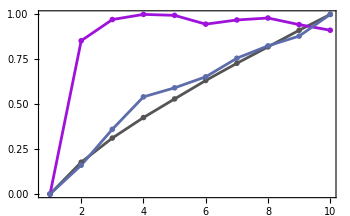
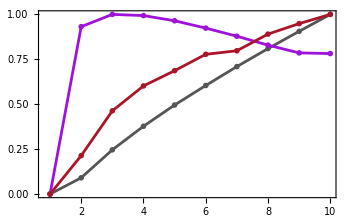

```mathematica
Clear[normalising]
normalising[data_]:=(data-Min[data])/(Max[data]-Min[data]);
opts3 = {Frame->True,FrameStyle->Directive[{Black,FontSize->8,FontFamily->"Helvetica"}],LabelStyle->Directive[{FontSize->8,FontFamily->"Helvetica"}]};

func2Apply = Max;
sso1TRange = {400,700};
quies2TRange = {750,1000};
flagellarRange = {330,400};
baseNerveRange = {100,300};
sat1T = Table[func2Apply[Select[rData1T[[i]],Between[#[[1]],flagellarRange]&][[;;,2]]],{i,Length@rData1T}];
sat1TN = Table[func2Apply[Select[rData1TN[[i]],Between[#[[1]],sso1TRange]&][[;;,2]]],{i,Length@rData1TN}];
sat1TN200 = Table[func2Apply[Select[rData1TN[[i]],Between[#[[1]],baseNerveRange]&][[;;,2]]],{i,Length@rData1TN}];
sat2T = Table[func2Apply[Select[rData2T[[i]],Between[#[[1]],flagellarRange]&][[;;,2]]],{i,Length@rData2T}];
sat2TN = Table[ func2Apply[Select[rData2TN[[i]],Between[#[[1]],quies2TRange]&][[;;,2]]],{i,Length@rData2TN}];
sat2TN200 = Table[ func2Apply[Select[rData2TN[[i]],Between[#[[1]],baseNerveRange]&][[;;,2]]],{i,Length@rData2TN}];

satData1T = {normalising[sat1T],normalising[sat1TN200],normalising[sat1TN]};
satData2T = {normalising[sat2T],normalising[sat2TN200],normalising[sat2TN]};

{Show[{ListLinePlot[satData1T,opts3,PlotStyle->{Darker@Gray,purple, col1TN}],
ListPlot[satData1T,PlotStyle->{Darker@Gray,purple, col1TN},PlotMarkers->fm2["Circle",5,0.5]]}],

Show[{ListLinePlot[satData2T,opts3,PlotStyle->{Darker@Gray,purple, col2TN}],
ListPlot[satData2T,PlotStyle->{Darker@Gray,purple, col2TN},PlotMarkers->fm2["Circle",5,0.5]]}]}
```

```mathematica
Clear[dataExtractor]
dataExtractor[data_,range_,type_:"nerve"]:=Block[{dat,mean,std,median,lowQ,highQ},
dat = Table[Max[Select[data[[j]][type][[i]],Between[#[[1]],range]&][[;;,3]]],{j,Length@data},{i,10}];
dat = (normalising/@dat)ᵀ;

mean = Mean/@dat;
std = StandardDeviation/@dat;
MapThread[Around[#1,#2]&,{mean,std}]

(*median = Median/@dat;
lowQ = Quantile[#,0.16]&/@dat;
highQ = Quantile[#,0.84]&/@dat;
MapThread[Around[#1,{#1-#2,#3-#1}]&,{median,lowQ,highQ}]*)
]
```

```mathematica
baseDir = "N:\\Storage Files\\UCL Data\\Anopheles\\";
ssoMoses = {(*4,*)5(*,6*),7,8(*,12*),13,14};
ssoMos = "Mosquito "<>ToString[#]&/@ssoMoses;
quiesMoses = {1,16};
quiesMos = "Mosquito "<>ToString[#]&/@quiesMoses;
{sso1Tdata,sso2Tdata} = (FileNames["*Laser and Nerve*.txt",baseDir<>#<>"\\set_1\\0_overview\\"]&/@ssoMos)ᵀ;
{quies1Tdata,quies2Tdata} = (FileNames["*Laser and Nerve*.txt",baseDir<>#<>"\\set_1\\0_overview\\"]&/@quiesMos)ᵀ;
```

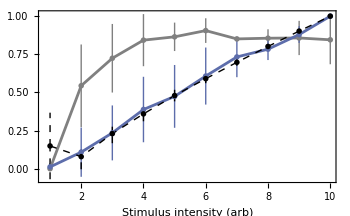
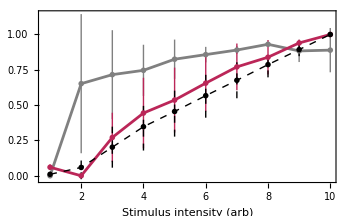

```mathematica
ssoData1T= Import[#,"RawJSON"]&/@sso1Tdata;
ssoData2T = Import[#,"RawJSON"]&/@sso2Tdata;

quiesData1T = Import[#,"RawJSON"]&/@quies1Tdata;
quiesData2T = Import[#,"RawJSON"]&/@quies2Tdata;

(*sso1TRange = {400,700};
quies2TRange = {750,1000};
flagellarRange = {330,400};

{op11,op22} = {0.5,1};
{c111,c222,c333} = {Gray,blue,Black};
pointSize = 3;
{satFig1T,satFig2T}={ListLinePlot[{
dataExtractor[ssoData1T,baseNerveRange,"nerve"],
dataExtractor[ssoData1T,sso1TRange,"nerve"],
dataExtractor[ssoData1T,flagellarRange,"laser"]},
PlotStyle->{c111,c222,{Dashed,c333,AbsoluteThickness[1]}},
Frame->{True,True,False,False},opts3,
FrameLabel->{"Stimulus intensity (arb)",None},
PlotMarkers->{fm2["Circle",pointSize,op11],fm2["Square",pointSize,op11],fm2["Diamond",pointSize,op22]}]
,
ListLinePlot[{
dataExtractor[quiesData2T,baseNerveRange,"nerve"],
dataExtractor[quiesData2T,quies2TRange,"nerve"],
dataExtractor[quiesData2T,flagellarRange,"laser"]},
PlotStyle->{c111,pink,{Dashed,c333,AbsoluteThickness[1]}},
Frame->{True,False,False,False},
opts3,
FrameLabel->{"Stimulus intensity (arb)",None},
PlotMarkers->{fm2["Circle",pointSize,op11],fm2["Square",pointSize,op11],fm2["Diamond",pointSize,op22]}]}*)
```

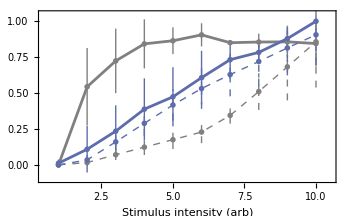
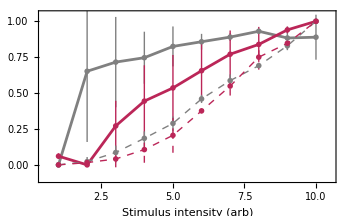

```mathematica
(*{op11,op22} = {0.5,1};
{c111,c222,c333} = {Gray,blue,Black};
pointSize = 3.5;
{satFig1T,satFig2T}={ListLinePlot[{
dataExtractor[ssoData1T,baseNerveRange,"nerve"],
dataExtractor[ssoData1T,sso1TRange,"nerve"],
{{1,0}}~Join~({Range[10],dataExtractor[ssoData1T,baseNerveRange,"laser"]}ᵀ[[2;;]]),
{{1,0}}~Join~({Range[10],dataExtractor[ssoData1T,sso1TRange,"laser"]}ᵀ[[2;;]])},
PlotStyle->{c111,c222,{Dashed,c111,AbsoluteThickness[1]},{Dashed,c222,AbsoluteThickness[1]}},
Frame->{True,True,False,False},opts3,
FrameLabel->{"Stimulus intensity (arb)",None},PlotRange->{{0.5,10.5},{-0.1,1.05}},
PlotMarkers->{fm2["Circle",pointSize,op11],fm2["Circle",pointSize,op11],fm2["Diamond",pointSize,op22],fm2["Diamond",pointSize,op22]}]
,
ListLinePlot[{
dataExtractor[quiesData2T,baseNerveRange,"nerve"],
dataExtractor[quiesData2T,quies2TRange,"nerve"],
{{1,0}}~Join~({Range[10],dataExtractor[quiesData2T,baseNerveRange,"laser"]}ᵀ[[2;;]]),
{{1,0}}~Join~({Range[10],dataExtractor[quiesData2T,quies2TRange,"laser"]}ᵀ[[2;;]])},
PlotStyle->{c111,pink,{Dashed,c111,AbsoluteThickness[1]},{Dashed,pink,AbsoluteThickness[1]}},
Frame->{True,False,False,False},
opts3,
FrameLabel->{"Stimulus intensity (arb)",None},PlotRange->{{0.5,10.5},{-0.1,1.05}},
PlotMarkers->{fm2["Circle",pointSize,op11],fm2["Circle",pointSize,op11],fm2["Diamond",pointSize,op22],fm2["Diamond",pointSize,op22]},IntervalMarkers->{"Fences","Bars","Fences","Bars"}]}*)
```

```mathematica
(*{op11,op22} = {0.5,1};
{c111,c222,c333} = {Gray,blue,Black};
pointSize = 3.5;
sso1TRange = {400,600};
quies2TRange = {790,860};
flagellarRange = {330,400};

{{satFig1TQ,satFig2TQ},{satFig1TS,satFig2TS}}= {{
(*1T QUIES*)
ListLinePlot[{
dataExtractor[quiesData1T,baseNerveRange,"nerve"],
dataExtractor[quiesData1T,sso1TRange,"nerve"]},
PlotStyle->{c111,c222},
Frame->{True,True,False,False},
opts3,
FrameLabel->{"Stimulus intensity (arb)",None},PlotRange->{{0.5,10.5},{-0.1,1.05}},
PlotMarkers->{fm2["Circle",pointSize,op11],fm2["Diamond",pointSize,op22]},IntervalMarkers->{"Bars","Fences"}],

(*2T QUIES*)
ListLinePlot[{
dataExtractor[quiesData2T,baseNerveRange,"nerve"],
dataExtractor[quiesData2T,quies2TRange,"nerve"]},
PlotStyle->{c111,color2TPoints},
Frame->{True,False,False,False},
opts3,
FrameLabel->{"Stimulus intensity (arb)",None},PlotRange->{{0.5,10.5},{-0.1,1.05}},
PlotMarkers->{fm2["Circle",pointSize,op11],fm2["Diamond",pointSize,op22]},IntervalMarkers->{"Bars","Fences"}]},
{
(*1T SSO*)
ListLinePlot[{
dataExtractor[ssoData1T,baseNerveRange,"nerve"],
dataExtractor[ssoData1T,sso1TRange,"nerve"]},
PlotStyle->{c111,c222},
Frame->{True,True,False,False},
opts3,
FrameLabel->{"Stimulus intensity (arb)",None},PlotRange->{{0.5,10.5},{-0.1,1.05}},
PlotMarkers->{fm2["Circle",pointSize,op11],fm2["Diamond",pointSize,op22]},IntervalMarkers->{"Bars","Fences"}],

(*2T SSO*)
ListLinePlot[{
dataExtractor[ssoData2T,baseNerveRange,"nerve"],
dataExtractor[ssoData2T,quies2TRange,"nerve"]},
PlotStyle->{c111,color2TPoints},
Frame->{True,False,False,False},
opts3,
FrameLabel->{"Stimulus intensity (arb)",None},PlotRange->{{0.5,10.5},{-0.1,1.05}},
PlotMarkers->{fm2["Circle",pointSize,op11],fm2["Diamond",pointSize,op22]},IntervalMarkers->{"Bars","Fences"}]}
}*)
```

{A→-0.894887,b→0.60769,c→0.89369}

{A→0.00604216,b→0.,c→0.412033}

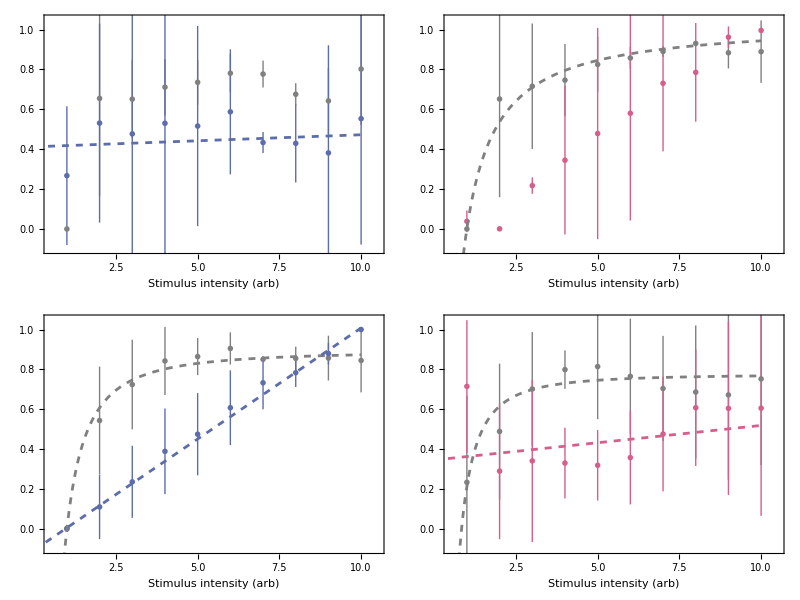

```mathematica
Clear[fitPower,header]

header[data_]:= If[Length[#]<2,Around[#,0.03],#]&/@data;
fitPower[data_,model_:A x^(-1/b)+c] := Block[{dat,vals,weights},
dat = header[data];
vals = dat[[;;,1]];
weights = dat[[;;,2]];
NonlinearModelFit[vals,model,{A,{b,1},c},x,Weights->1/weights]];

q1Tfit200 = fitPower[dataExtractor[quiesData1T,baseNerveRange,"nerve"]];
q1Tfit510 = fitPower[dataExtractor[quiesData1T,sso1TRange,"nerve"],A x +c];

q2Tfit200 = fitPower[dataExtractor[quiesData2T,baseNerveRange,"nerve"]];
q2Tfit810 = fitPower[dataExtractor[quiesData2T,quies2TRange,"nerve"],A x +c];

sso1Tfit200 = fitPower[dataExtractor[ssoData1T,baseNerveRange,"nerve"]];
sso1Tfit510 = fitPower[dataExtractor[ssoData1T,sso1TRange,"nerve"],A x +c];

sso2Tfit200 = fitPower[dataExtractor[ssoData2T,baseNerveRange,"nerve"]];
sso2Tfit810 = fitPower[dataExtractor[ssoData2T,quies2TRange,"nerve"],A x +c];



sso1Tfit200["BestFitParameters"]
q1Tfit510["BestFitParameters"]

Grid@{{Show[{ListPlot[{dataExtractor[quiesData1T,baseNerveRange,"nerve"],dataExtractor[quiesData1T,sso1TRange,"nerve"]},
PlotStyle->{c111,c222},Frame->{True,True,False,False}, opts3,FrameLabel->{"Stimulus intensity (arb)",None},PlotRange->{{0.5,10.5},{-0.1,1.05}},
PlotMarkers->{fm2["Circle",pointSize,op11],fm2["Diamond",pointSize,op22]},IntervalMarkers->{"Bars","Fences"}],
Plot[{q1Tfit200[x],q1Tfit510[x]},{x,0,10},PlotStyle->{{Dashed,c111},{Dashed,c222}}]}],

 Show[{ListPlot[{dataExtractor[quiesData2T,baseNerveRange,"nerve"],dataExtractor[quiesData2T,sso1TRange,"nerve"]},
PlotStyle->{c111,color2T},Frame->{True,True,False,False}, opts3,FrameLabel->{"Stimulus intensity (arb)",None},PlotRange->{{0.5,10.5},{-0.1,1.05}},
PlotMarkers->{fm2["Circle",pointSize,op11],fm2["Diamond",pointSize,op22]},IntervalMarkers->{"Bars","Fences"}],
Plot[{q2Tfit200[x],q2Tfit810[x]},{x,0,10},PlotStyle->{{Dashed,c111},{Dashed,color2T}}]}]},

{Show[{ListPlot[{dataExtractor[ssoData1T,baseNerveRange,"nerve"],dataExtractor[ssoData1T,sso1TRange,"nerve"]},
PlotStyle->{c111,c222},Frame->{True,True,False,False}, opts3,FrameLabel->{"Stimulus intensity (arb)",None},PlotRange->{{0.5,10.5},{-0.1,1.05}},
PlotMarkers->{fm2["Circle",pointSize,op11],fm2["Diamond",pointSize,op22]},IntervalMarkers->{"Bars","Fences"}],
Plot[{sso1Tfit200[x],sso1Tfit510[x]},{x,0,10},PlotStyle->{{Dashed,c111},{Dashed,c222}}]}],

Show[{ListPlot[{dataExtractor[ssoData2T,baseNerveRange,"nerve"],dataExtractor[ssoData2T,quies2TRange,"nerve"]},
PlotStyle->{c111,color2T},Frame->{True,True,False,False}, opts3,FrameLabel->{"Stimulus intensity (arb)",None},PlotRange->{{0.5,10.5},{-0.1,1.05}},
PlotMarkers->{fm2["Circle",pointSize,op11],fm2["Diamond",pointSize,op22]},IntervalMarkers->{"Bars","Fences"}],
Plot[{sso2Tfit200[x],sso2Tfit810[x]},{x,0,10},PlotStyle->{{Dashed,c111},{Dashed,color2T}}]}]}}
```

#### Older plots

```mathematica
plotGrid[{
{aga1T[[1]],aga2T[[1]],nquies510,nquies810},
{aga1T[[2]],aga2T[[2]],nwsso510,nwsso810},
{aga1T[[3]],aga2T[[3]],nsso510,nsso810}},

ImageSize->165*3.78 4/5,
smallFigSize = 0.6;
ItemSize->{{GoldenRatio 1,GoldenRatio,smallFigSize,smallFigSize,smallFigSize,smallFigSize}(* columns*),{1,1,1}(* rows*)},
Spacings->{{0,15,5,15,5}(*columns separation*),{0,0,0}(* row separation*)},
Method->{"FixFrameTicks"->False,"AllCustomTicks"->Automatic}]
```

-Graphics-

```mathematica
Export[expDir<>"figure_1_justAnophelesB2.pdf",%,ImageResolution->200]
```

C:\Users\hadif\Proton Drive\c.a.alampounti\My files\Uni\UCL\Projects\02_DP Theory paper\images\article figures\Nature submission 2\raw_svg_figures\figure_1_justAnophelesB2.pdf

```mathematica
{nquies1T350Hz,nquies2T350Hz,nquies510,nquies810}
{nwsso3601T,nwsso3602T,nwsso510,nwsso810}
{nsso3551T,nsso3552T,nsso510,nsso810}
```

```mathematica
plotGrid[{
{aga1T[[1]],SpanFromLeft,aga2T[[1]],SpanFromLeft,ampScale1T,ampScale2T},
{aga1T[[2]],SpanFromLeft,aga2T[[2]],SpanFromLeft,SpanFromAbove,SpanFromAbove},
{aga1T[[3]],SpanFromLeft,aga2T[[3]],SpanFromLeft,SpanFromAbove,SpanFromAbove},
{nquies1T350Hz,nquies510,nquies2T350Hz,nquies810,Null,Null},
{nwsso3601T,nwsso510,nwsso3602T,nwsso810,Null,Null},
{nsso3551T,nsso510,nsso3552T,nsso810,Null,Null}},

ImageSize->165*3.78 4/5,
ItemSize->{GoldenRatio{ 1,1,1,1, 1.5,1.5}(* columns*),1.5{1,1,1,0.6,0.6,0.6}(* rows*)},
Spacings->{{5,0,5,20,20}(*columns separation*),{0,0,20}(* row separation*)},
Method->{"FixFrameTicks"->False,"AllCustomTicks"->Automatic}]
```

-Graphics-

```mathematica
Export[expDir<>"figure_1_justAnophelesC.pdf",%,ImageResolution->1200]
```

C:\Users\hadif\Proton Drive\c.a.alampounti\My files\Uni\UCL\Projects\02_DP Theory paper\images\article figures\Nature submission 2\raw_svg_figures\figure_1_justAnophelesC.pdf

```mathematica
smallFigSize = 0.6;
rowSize = 1;
plotGrid[{
{aga1T[[1]],aga2T[[1]],nquies510,nquies810,nquies1T350Hz,nquies2T350Hz},
{aga1T[[2]],aga2T[[2]],nwsso510,nwsso810,nwsso3601T,nwsso3602T},
{aga1T[[3]],aga2T[[3]],nsso510,nsso810,nsso3551T,nsso3552T}},

ImageSize->165*3.78 4/5,
ItemSize->{{GoldenRatio 1,GoldenRatio,smallFigSize,smallFigSize,smallFigSize,smallFigSize}(* columns*),{rowSize,rowSize,rowSize,1.5}(* rows*)},
Spacings->{{0,25,5,15,5}(*columns separation*),{0,0,20}(* row separation*)},
Method->{"FixFrameTicks"->False,"AllCustomTicks"->Automatic}]
Export[expDir<>"figure_1_justAnophelesDa.pdf",%,ImageResolution->200]
```

-Graphics-

C:\Users\hadif\Proton Drive\c.a.alampounti\My files\Uni\UCL\Projects\02_DP Theory paper\images\article figures\Nature submission 2\raw_svg_figures\figure_1_justAnophelesDa.pdf

```mathematica
plotGrid[{{ampScale1T,ampScale2T,None,None,None,None(*satFig1T,SpanFromLeft,satFig2T,SpanFromLeft*)}},

ImageSize->165*3.78 4/5,
ItemSize->{{GoldenRatio 1,GoldenRatio,smallFigSize,smallFigSize,smallFigSize,smallFigSize}(* columns*),{1.5}(* rows*)},
Spacings->{{5,25,5,15,5}(*columns separation*),{0,0,20}(* row separation*)},
Method->{"FixFrameTicks"->False,"AllCustomTicks"->Automatic}]
Export[expDir<>"figure_1_justAnophelesDb.pdf",%,ImageResolution->200]
```

-Graphics-

C:\Users\hadif\Proton Drive\c.a.alampounti\My files\Uni\UCL\Projects\02_DP Theory paper\images\article figures\Nature submission 2\raw_svg_figures\figure_1_justAnophelesDb.pdf

```mathematica
plotGrid[{{None,None,satFig1T,SpanFromLeft,satFig2T,SpanFromLeft}},

ImageSize->165*3.78 4/5,
ItemSize->{{GoldenRatio 1,GoldenRatio,smallFigSize,smallFigSize,smallFigSize,smallFigSize}(* columns*),{1.5}(* rows*)},
Spacings->{{5,25,5,15,5}(*columns separation*),{0,0,20}(* row separation*)},
Method->{"FixFrameTicks"->False,"AllCustomTicks"->Automatic}]
Export[expDir<>"figure_1_justAnophelesDc.pdf",%,ImageResolution->200]
```

-Graphics-

C:\Users\hadif\Proton Drive\c.a.alampounti\My files\Uni\UCL\Projects\02_DP Theory paper\images\article figures\Nature submission 2\raw_svg_figures\figure_1_justAnophelesDc.pdf

```mathematica
smallFigSize = 0.6;
rowSize = 1;
plotGrid[{
{aga1T[[1]],SpanFromLeft,aga2T[[1]],SpanFromLeft,None,None},
{aga1T[[2]],SpanFromLeft,aga2T[[2]],SpanFromLeft,ampScale1T,ampScale2T},
{aga1T[[3]],SpanFromLeft,aga2T[[3]],SpanFromLeft,SpanFromAbove,SpanFromAbove},
{nquies1T350Hz,nquies2T350Hz,nquies510,nquies810,satFig1T,satFig2T},
{nwsso3601T,nwsso3602T,nwsso510,nwsso810,SpanFromAbove,SpanFromAbove},
{nsso510,nsso810,nsso3551T,nsso3552T,SpanFromAbove,SpanFromAbove}},

ImageSize->165*3.78 4.3/5,
ItemSize->{{GoldenRatio /2,GoldenRatio/2,GoldenRatio/2,GoldenRatio/2,1.1,1.1}(* columns*),{rowSize,rowSize,rowSize,smallFigSize,smallFigSize,smallFigSize}(* rows*)},
Spacings->{{0,0,0,20,5}(*columns separation*),{0,0,40}(* row separation*)},
Method->{"FixFrameTicks"->False,"AllCustomTicks"->Automatic}]
```

-Graphics-

#### Final Plotting

```mathematica
smallFigSize = 0.6;
rowSize = 1;
plotGrid[{
{aga1T[[1]],aga2T[[1]],nquies510,nquies810,nquies1T350Hz,nquies2T350Hz},
{aga1T[[2]],aga2T[[2]],nwsso510,nwsso810,nwsso3601T,nwsso3602T},
{aga1T[[3]],aga2T[[3]],nsso510,nsso810,nsso3551T,nsso3552T},
{ampScale1T,ampScale2T,satFig1T,SpanFromLeft,satFig2T,SpanFromLeft}},

ImageSize->165*3.78 4.3/5,
ItemSize->{{GoldenRatio 1,GoldenRatio,smallFigSize,smallFigSize,smallFigSize,smallFigSize}(* columns*),{rowSize,rowSize,rowSize,1.5}(* rows*)},
Spacings->{{0,25,5,15,5}(*columns separation*),{0,0,20}(* row separation*)},
Method->{"FixFrameTicks"->False,"AllCustomTicks"->Automatic}]
```

-Graphics-

```mathematica
Export[expDir<>"figure_1_justAnophelesD.pdf",%,ImageResolution->200]
```

```mathematica
smallFigSize = 0.6;
rowSize = 1;
plotGrid[{
{aga1T[[1]],aga2T[[1]],nquies1T350Hz,nquies2T350Hz,nquies510,nquies810},
{aga1T[[2]],aga2T[[2]],nwsso3601T,nwsso3602T,nwsso510,nwsso810},
{aga1T[[3]],aga2T[[3]],nsso3551T,nsso3552T,nsso510,nsso810},
{ampScale1TQv2,ampScale2TQv2,satFig1TQ,SpanFromLeft,satFig2TQ,SpanFromLeft},
{ampScale1TSv2,ampScale2TSv2,satFig1TS,SpanFromLeft,satFig2TS,SpanFromLeft}},

ImageSize->165*3.78 4.3/5,
ItemSize->{{GoldenRatio 1,GoldenRatio,smallFigSize,smallFigSize,smallFigSize,smallFigSize}(* columns*),{rowSize,rowSize,rowSize,1.5,1.5}(* rows*)},
Spacings->{{0,25,5,15,5}(*columns separation*),{0,0,20,25}(* row separation*)},
Method->{"FixFrameTicks"->False,"AllCustomTicks"->Automatic}]
```

-Graphics-

## Figure 2

```mathematica
Clear[onetone,twotone]

{onetoneSSO,twotoneSSO}=Import[#,"RawJSON"]&/@FileNames["*JSON*","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito26\\set_1\\Laser"]; 
{onetoneNSSO,twotoneNSSO}=Import[#,"RawJSON"]&/@FileNames["*JSON*","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito26\\set_1\\Nerve"];

{onetoneQ,twotoneQ}=Import[#,"RawJSON"]&/@FileNames["*JSON*","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito31\\set_2\\Laser"]; 
{onetoneNQ,twotoneNQ}=Import[#,"RawJSON"]&/@FileNames["*JSON*","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito31\\set_2\\Nerve"];
```

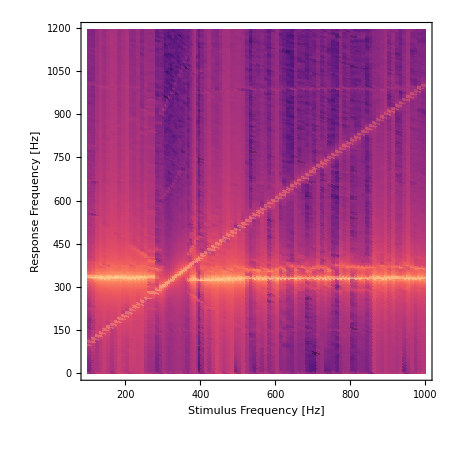
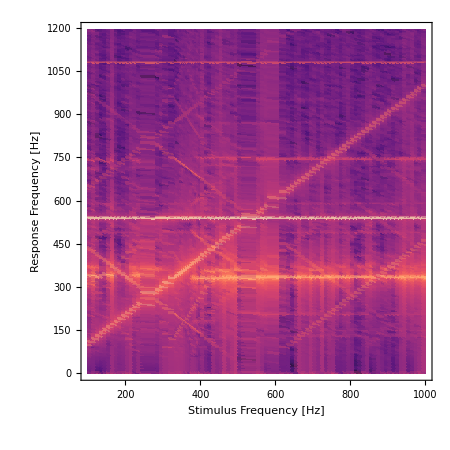

```mathematica
segmentL = 5;
{sso1TL,sso2TL}=(ListDensityPlot[#["3Dfft"][[segmentL]],PlotRange->Full,ColorFunction->(ColorData["Magma",1#]&),ColorFunctionScaling->True,ImageSize->450,ScalingFunctions->"Log",FrameLabel->{"Stimulus Frequency [Hz]","Response Frequency [Hz]"},FrameStyle->Directive@{FontSize->8,Black,FontFamily->"Helvetica"}(*,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->400,LegendMargins->{{0, 0}, {0, -20}},LabelStyle->{Black, FontSize->9},LegendLayout->"Row"],Below]*)]&/@{onetoneSSO,twotoneSSO})
```

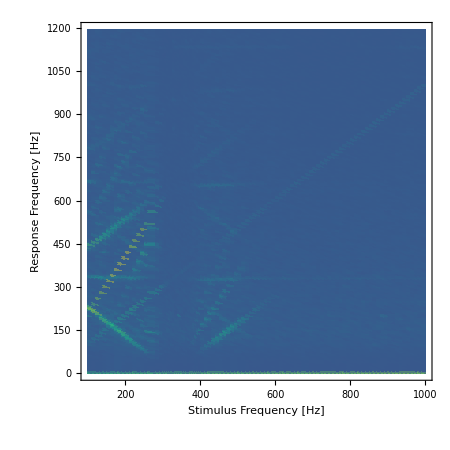
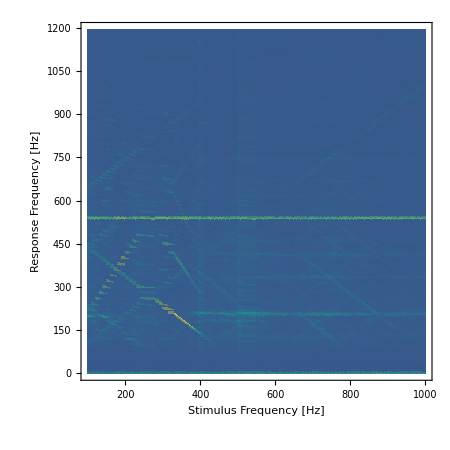

```mathematica
{sso1TN,sso2TN}=(ListDensityPlot[#["3Dfft"][[segmentL]],PlotRange->Full,ColorFunction->cf(*(ColorData["Viridis",1#]&)*),ColorFunctionScaling->True,ImageSize->450,ScalingFunctions->"Linear",FrameLabel->{"Stimulus Frequency [Hz]","Response Frequency [Hz]"},FrameStyle->Directive@{FontSize->8,Black,FontFamily->"Helvetica"}(*,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->400,LegendMargins->{{0, 0}, {0, -20}},LabelStyle->{Black, FontSize->9},LegendLayout->"Row"],Below]*)]&/@{onetoneNSSO,twotoneNSSO})
```

```mathematica
twotoneNQ["3Dfft"][[segmentL]][[;;,3]]//Max
```

0.594654

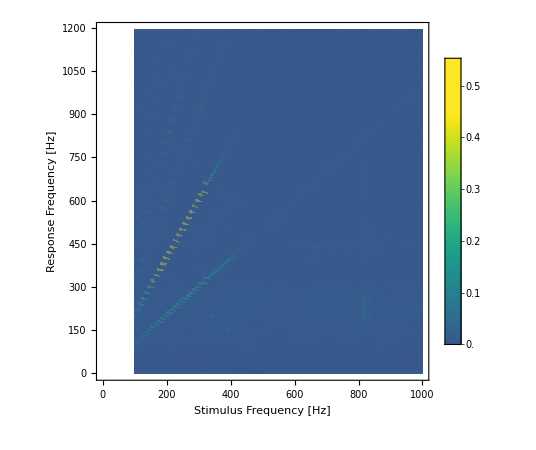
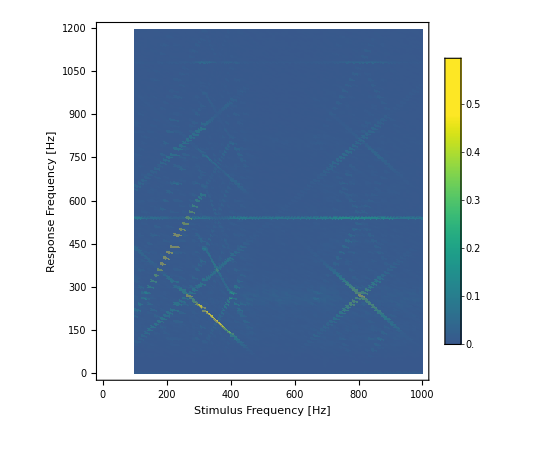
-Graphics- | -Graphics-

```mathematica
scaling="Linear";
cfName="Viridis";(*"Viridis",GrayYellowTones","NeonColors","Rainbow","RedBlueTones","RustTones","StarryNightColors","DeepSeaColors"*)
cf=ColorData[cfName,Rescale[#,{-.3,.8}]]&; (* Here I want a common color function *)

(*some ideas here: https://mathematica.stackexchange.com/questions/197759/reverse-colorfunction-or-colordata*)
colFuncUsed=cfName;
Grid@ {(ListDensityPlot[#["3Dfft"][[segmentL]],PlotRange->{0,0.6},ColorFunction->cf(*(ColorData[cfName,1.# (*1-#*)]&)*) (*cf*),ColorFunctionScaling->True,ImageSize->450,ScalingFunctions->scaling,FrameLabel->{"Stimulus Frequency [Hz]","Response Frequency [Hz]"},FrameStyle->Directive@{8,Black,FontFamily->"Helvetica"},PlotLegends->BarLegend[Automatic,LegendMarkerSize->400,LegendMargins->{{0, 0}, {0, -20}},LabelStyle->{Black, FontSize->8},LegendLayout->"Column"(*"Row"*)]]&/@{onetoneNQ,twotoneNQ})}
```

```mathematica
Clear[segmenter]
segmenter[data_,cutoff_:530,separation_:70]:=Block[{t1,t2,t3},
t1=Select[data["3Dfft"][[5]],10<#[[2]]<cutoff&];
t2=MapAt[#+cutoff+separation&,Select[data["3Dfft"][[2]],10<#[[2]]<cutoff&],{All,2}];
t3=MapAt[#+2 cutoff+2*separation&,Select[data["3Dfft"][[1]],10<#[[2]]<cutoff&],{All,2}];
t1~Join~t2~Join~t3
]

twoToneQLaser = segmenter[twotoneQ];
twoToneQNerve = segmenter[twotoneNQ];
twoToneSSOLaser = segmenter[twotoneSSO];
twoToneSSONerve = segmenter[twotoneNSSO];
```

Part::partw: Part 5 of twotoneQ[3Dfft] does not exist.

Part::partw: Part 2 of twotoneQ[3Dfft] does not exist.

Part::partd: Part specification 5⟦2⟧ is longer than depth of object.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::partw: Part 2 of twotoneQ[3Dfft] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification 2⟦2⟧ is longer than depth of object.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Select::normal: Nonatomic expression expected at position 1 in Select[3Dfft,10<#1⟦2⟧<530&].

MapAt::partw: Part {All,2} of Select[3Dfft,10<#1⟦2⟧<530&] does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Part::argm will be suppressed during this calculation.

Join::heads: Heads Part and MapAt at positions 1 and 2 are expected to be the same.

Part::partw: Part 5 of twotoneNQ[3Dfft] does not exist.

Part::partw: Part 2 of twotoneNQ[3Dfft] does not exist.

Part::partd: Part specification 5⟦2⟧ is longer than depth of object.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::partw: Part 2 of twotoneNQ[3Dfft] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification 2⟦2⟧ is longer than depth of object.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Select::normal: Nonatomic expression expected at position 1 in Select[3Dfft,10<#1⟦2⟧<530&].

MapAt::partw: Part {All,2} of Select[3Dfft,10<#1⟦2⟧<530&] does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Part::argm will be suppressed during this calculation.

Join::heads: Heads Part and MapAt at positions 1 and 2 are expected to be the same.

Part::partw: Part 5 of twotoneSSO[3Dfft] does not exist.

Part::partw: Part 2 of twotoneSSO[3Dfft] does not exist.

Part::partd: Part specification 5⟦2⟧ is longer than depth of object.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::partw: Part 2 of twotoneSSO[3Dfft] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification 2⟦2⟧ is longer than depth of object.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Select::normal: Nonatomic expression expected at position 1 in Select[3Dfft,10<#1⟦2⟧<530&].

MapAt::partw: Part {All,2} of Select[3Dfft,10<#1⟦2⟧<530&] does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Part::argm will be suppressed during this calculation.

Join::heads: Heads Part and MapAt at positions 1 and 2 are expected to be the same.

Part::partw: Part 5 of twotoneNSSO[3Dfft] does not exist.

Part::partw: Part 2 of twotoneNSSO[3Dfft] does not exist.

Part::partd: Part specification 5⟦2⟧ is longer than depth of object.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::partw: Part 2 of twotoneNSSO[3Dfft] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification 2⟦2⟧ is longer than depth of object.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Select::normal: Nonatomic expression expected at position 1 in Select[3Dfft,10<#1⟦2⟧<530&].

MapAt::partw: Part {All,2} of Select[3Dfft,10<#1⟦2⟧<530&] does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Part::argm will be suppressed during this calculation.

Join::heads: Heads Part and MapAt at positions 1 and 2 are expected to be the same.

```mathematica
Show[{ListPlot3D[twoToneQLaser,PlotRange->{Full,Full,Automatic},ColorFunction->"Magma",ColorFunctionScaling->True,(*ColorFunction->"Viridis",*)ImageSize->500,ScalingFunctions->"Linear",AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Boxed->{Left,Bottom,Back},AxesStyle->Directive@{Black,FontSize->8,FontFamily->"Arial"(*,AbsoluteThickness[1]*)},ViewPoint->{1.0654300961448715,-2.2274333415742538,2.313733941699451},RegionFunction->Function[{x,y,z},y<500 || 600<y<1100 || y>1300](*{0,-2.2274333415742538,2.313733941699451}*),MeshStyle->Directive[LightGray,Opacity[0.2]]]
}]
```

-Graphics3D-

```mathematica
Show[{ListPlot3D[twoToneQNerve,PlotRange->{Full,{0,1700},{0,0.6}},ColorFunction->(ColorData["Viridis",Rescale[#3,{-.3,.8}]]&),ColorFunctionScaling->True,(*ColorFunction->"Viridis",*)ImageSize->500,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Boxed->{Left,Bottom,Back},AxesStyle->Directive@{Black,FontSize->8,FontFamily->"Arial"(*,AbsoluteThickness[1]*)},ViewPoint->{1.0654300961448715,-2.2274333415742538,2.313733941699451},RegionFunction->Function[{x,y,z},y<500 ||600<y<1100||y>1200](*{0,-2.2274333415742538,2.313733941699451}*),MeshStyle->Directive[LightGray,Opacity[0.2]],Method->{"Grid"->"Rectangular"}],

ListLinePlot3D[Table[Select[dict2TN[[dp]]["dpTrace"],#[[2]]<500&],{dp,usefulDPs}](*(dict2TN[[#]]["dpTrace"]&/@usefulDPs)*),PlotStyle->Directive@{pink,AbsoluteThickness[2]},Filling->Bottom,FillingStyle->Opacity[0.2]]}]
```

-Graphics3D-

```mathematica
ListPlot3D[twoToneSSONerve,PlotRange->{Full,{20,1700},{0,0.25}},ColorFunction->(ColorData["Viridis",Rescale[#3,{-.3,.8}]]&),ColorFunctionScaling->True,(*ColorFunction->"Viridis",*)ImageSize->500,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Boxed->{Left,Bottom,Back},AxesStyle->Directive@{Black,FontSize->8,FontFamily->"Arial"(*,AbsoluteThickness[1]*)},ViewPoint->{1.0654300961448715,-2.2274333415742538,2.313733941699451},RegionFunction->Function[{x,y,z},y<500 ||600<y<1100||y>1200](*{0,-2.2274333415742538,2.313733941699451}*),MeshStyle->Directive[LightGray,Opacity[0.2]],InterpolationOrder->5]
```

-Graphics3D-

## Mechanical State

```mathematica
ListLinePlot[Fold[HighpassFilter,readMyFile[#][[;;2000,2]],2π/20000{60,60,60}],PlotRange->1200{1,-1},Frame->False,Axes->False,PlotStyle->{AbsoluteThickness[2],Darker@Gray}]&/@{"M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito26\\set_1\\Laser_PreStim\\healthy_files\\M_AGA_Kisumu_ZT12_2023-02-16_No 001_Laser_PreStim_a_005_(009).txt","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito32\\set_2\\Laser_PreStim\\healthy_files\\M_AGA_Kisumu_ZT15_2023-04-04_No 001_Laser_PreStim_a_016_(031).txt"}
```

## DP Mosaics

```mathematica
Clear[onetone,twotone]
(*state="SSO";
{onetone,twotone}=Import[#,"RawJSON"]&/@FileNames["*JSON*","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito26\\set_1\\Laser"]; 
{onetoneN,twotoneN}=Import[#,"RawJSON"]&/@FileNames["*JSON*","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito26\\set_1\\Nerve"]; *)
state="QUIES";
{onetone,twotone}=Import[#,"RawJSON"]&/@FileNames["*JSON*","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito31\\set_2\\Laser"]; 
{onetoneN,twotoneN}=Import[#,"RawJSON"]&/@FileNames["*JSON*","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito31\\set_2\\Nerve"]; 
(*state="PYM";
{onetone,twotone}=Import[#,"RawJSON"]&/@FileNames["*JSON*","M:\\Documents\\Alex\\UCL_data\\2023 - 2 tone PYM\\Pymetrozine\\pym_01\\split files\\Laser"]; 
{onetoneN,twotoneN}=Import[#,"RawJSON"]&/@FileNames["*JSON*","M:\\Documents\\Alex\\UCL_data\\2023 - 2 tone PYM\\Pymetrozine\\pym_01\\split files\\Nerve"];*)


segmentL=5; (* chooses the amplitude at which we will we working on*)

σ=1.25;                                (* gaussian blurring to survive *)
peakSharpness=0.5;  (* sharpness criterion *)
responseHeight=2; (* minimum peak height in nm *)
peakSettings="(σ="<>ToString[σ]<>"_s="<>ToString[peakSharpness]<>"_h="<>ToString[responseHeight]<>")";

{fftLaser1T,fftLaser2T}=Table[GatherBy[data["3Dfft"][[segmentL]],#[[1]]&],{data,{onetone,twotone}}];
{peaks1T,peaks2T}=Table[PeakDetection[#,σ,peakSharpness,responseHeight]&/@data,{data,{fftLaser1T,fftLaser2T}}];
```

```mathematica
cf=ColorData["Magma",Rescale[#,{0,1},{0.25,1}]]&;
cf[#]&/@Range[0,1,0.1]
```

{RGBColor[0.315086183, 0.071192764575, 0.48483190675],RGBColor[0.4322057465, 0.11754752087499999, 0.506103985],RGBColor[0.550287252, 0.161157816, 0.505718782],RGBColor[0.672153866, 0.20039185312500002, 0.48716547537499993],RGBColor[0.793972169, 0.244941637, 0.44686947650000003],RGBColor[0.901325413875, 0.3164890085, 0.38994925462499996],RGBColor[0.9666102395, 0.43611084150000023, 0.3596696615],RGBColor[0.991300556125, 0.577331614625, 0.401043400375],RGBColor[0.9973445322500001, 0.7172787677500002, 0.49235459250000013],RGBColor[0.993910283625, 0.8548147175, 0.611633561125],RGBColor[0.987052509, 0.991437853, 0.749504188]}

```mathematica
cf=ColorData["Magma",Rescale[#,{-1000,2000}]]&; (* colour code only amplitudes between 500 and 2000 and saturate everything else *)
cf[#]&/@Range[0,2000,100]
```

{RGBColor[0.445163096, 0.122724371, 0.506900806],RGBColor[0.4973477535, 0.1425907145, 0.507953804],RGBColor[0.550287252, 0.161157816, 0.505718782],RGBColor[0.604053284, 0.1787611725, 0.49994276049999997],RGBColor[0.658483116, 0.196026835, 0.490253338],RGBColor[0.7131744630000001, 0.213889515, 0.4762454505],RGBColor[0.767397681, 0.233704708, 0.457755411],RGBColor[0.8199199915, 0.2574550275, 0.435016974],RGBColor[0.868793368, 0.287728205, 0.409303002],RGBColor[0.9111188075000001, 0.3274035365, 0.383935711],RGBColor[0.944006448, 0.377642889, 0.365136328],RGBColor[0.9666102395, 0.4361108415, 0.3596696615],RGBColor[0.981000291, 0.4984278, 0.369734157],RGBColor[0.989750771, 0.561584785, 0.3933964725],RGBColor[0.994737698, 0.624349657, 0.427396771],RGBColor[0.997001306, 0.686457925, 0.469168575],RGBColor[0.997228367, 0.747980563, 0.516859378],RGBColor[0.9958062775000001, 0.8091164495000001, 0.5694233095],RGBColor[0.993169558, 0.870024467, 0.626189463],RGBColor[0.989994738, 0.9307620759999999, 0.686561898],RGBColor[0.987052509, 0.991437853, 0.749504188]}

```mathematica
ColorData["Gradients"]
```

```mathematica
scaling="Log";
(* either use Linear scaling with no ColorFunctionScaling->False and the ColorFunction->cf function, or Log scale with "Magma" *)
colFuncUsed="Magma";
Grid@{(ListDensityPlot[#["3Dfft"][[segmentL]],PlotRange->Full,ColorFunction->(ColorData[colFuncUsed,1#]&),ColorFunctionScaling->True,ImageSize->450,ScalingFunctions->scaling,FrameLabel->{"Stimulus Frequency [Hz]","Response Frequency [Hz]"},FrameStyle->Directive@{16,Black,FontFamily->"Helvetica"},PlotLegends->BarLegend[Automatic,LegendMarkerSize->400,LegendMargins->{{0, 0}, {0, -20}},LabelStyle->{Black, FontSize->16},LegendLayout->"Row"]]&/@{onetone,twotone})}

(*Export[expDir<>"\\DP maps\\Mosquito PYM01 - "<>state<>" Laser "<>scaling<>" "<>colFuncUsed<>ToString[imageRes]<>"dpi.png",%,ImageResolution->imageRes]*)
```

-Graphics- | -Graphics-

```mathematica
Manipulate[Table[ColorData[cfName,Rescale[#,{-.8,.8}]]&[x],{x,st,end,0.01}],{st,-1,1},{end,0,2}]
```

ColorData::notent: cfName is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

General::stop: Further output of ColorData::notent will be suppressed during this calculation.

ColorData::notent: cfName is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

General::stop: Further output of ColorData::notent will be suppressed during this calculation.

ColorData::notent: 
   cfName is not a known entity, class, or tag for ColorData. Use ColorData
    [] for a list of entities.

General::stop: Further output of ColorData::notent
     will be suppressed during this calculation.

ColorData::notent: cfName is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

General::stop: Further output of ColorData::notent will be suppressed during this calculation.

ColorData::notent: cfName is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

General::stop: Further output of ColorData::notent will be suppressed during this calculation.

```mathematica
scaling="Linear";
cfName="Viridis";(*"Viridis",GrayYellowTones","NeonColors","Rainbow","RedBlueTones","RustTones","StarryNightColors","DeepSeaColors"*)
cf=ColorData[cfName,Rescale[#,{-.3,.8}]]&; (* Here I want a common color function *)

(*some ideas here: https://mathematica.stackexchange.com/questions/197759/reverse-colorfunction-or-colordata*)
colFuncUsed=cfName;
Grid@ {(ListDensityPlot[#["3Dfft"][[segmentL]],PlotRange->Full,ColorFunction->cf(*(ColorData[cfName,1.# (*1-#*)]&)*) (*cf*),ColorFunctionScaling->False,ImageSize->450,ScalingFunctions->scaling,FrameLabel->{"Stimulus Frequency [Hz]","Response Frequency [Hz]"},FrameStyle->Directive@{16,Black,FontFamily->"Helvetica"},PlotLegends->BarLegend[Automatic,LegendMarkerSize->400,LegendMargins->{{0, 0}, {0, -20}},LabelStyle->{Black, FontSize->16},LegendLayout->"Column"(*"Row"*)]]&/@{onetoneN,twotoneN})}

(*Export[expDir<>"\\DP maps\\Mosquito - "<>state<>" Nerve "<>scaling<>" "<>cfName(*colFuncUsed*)<>ToString[imageRes]<>"dpi_2.png",%,ImageResolution->imageRes]*)
```

Part::partw: Part 5 of onetoneN[3Dfft] does not exist.

ListDensityPlot::arrayerr: onetoneN[3Dfft]⟦5⟧ must be a valid array.

Part::partw: Part 5 of twotoneN[3Dfft] does not exist.

ListDensityPlot::arrayerr: twotoneN[3Dfft]⟦5⟧ must be a valid array.

ListDensityPlot[onetoneN[3Dfft]⟦5⟧,PlotRange→Full,ColorFunction→(ColorData[cfName,Rescale[#1,{-0.3,0.8}]]&),ColorFunctionScaling→False,ImageSize→450,ScalingFunctions→Linear,FrameLabel→{Stimulus Frequency [Hz],Response Frequency [Hz]},FrameStyle→Directive[{16,GrayLevel[0],FontFamily→Helvetica}],PlotLegends→] | ListDensityPlot[twotoneN[3Dfft]⟦5⟧,PlotRange→Full,ColorFunction→(ColorData[cfName,Rescale[#1,{-0.3,0.8}]]&),ColorFunctionScaling→False,ImageSize→450,ScalingFunctions→Linear,FrameLabel→{Stimulus Frequency [Hz],Response Frequency [Hz]},FrameStyle→Directive[{16,GrayLevel[0],FontFamily→Helvetica}],PlotLegends→]

```mathematica
ListPlot3D[twotoneN["3Dfft"][[segmentL]],PlotRange->Full,ColorFunction->(ColorData["Viridis",Rescale[#3,{-.3,.8}]]&),ColorFunctionScaling->True]
```

-Graphics3D-

```mathematica
freqChosen = 15; (* selects the frequency order *)
Show[{ListDensityPlot[twotoneN["3Dfft"][[segment]],PlotRange->Full,ColorFunction->"Viridis",ImageSize->550,ScalingFunctions->"Linear",FrameLabel->{"Stimulus Frequency [Hz]","Frequency Response [Hz]"},FrameStyle->Directive[{Black,16}],PlotLegends->Automatic],
ListPlot[{peaks2TN[[freqChosen,;;,{1,2}]]},PlotStyle->{AbsolutePointSize->6,red}]}]
```

Part::partd: Part specification peaks2TN⟦15,1;;All,{1,2}⟧ is longer than depth of object.

-Graphics-

```mathematica
freqChosen = 15; (* selects the frequency order *)
Show[{ListPlot[fftNerve2T[[freqChosen,;;,{2,3}]],Joined->True,FrameLabel->{"Stimulus Frequency [Hz]","FFT response [mV]"},AspectRatio->.5],
ListPlot[peaks2TN[[freqChosen,;;,{2,3}]],PlotStyle->{AbsolutePointSize->6,red}]}]
```

```mathematica
Solve[1 290 + n 540 == 830,n]
```

```mathematica
point=30 (*30*);
ListLinePlot[{dpEvolution2TN[[point,;;,{1,3}]],dpEvolution2TCN[[point,;;,{1,3}]]},ScalingFunctions->"Log",PlotLabel->DPs2TN[[point]],Epilog->{Black,Point[MapAt[Log,dpEvolution2TCN [[point,;;,{1,3}]],{All,2}]]},PlotLegends->{"DP evolution","DP evolution w/o cross-contributions"},PlotRange->{{0,1050},{10^-3,10^0}},AspectRatio->0.5]
```

## DP traces

```mathematica
Clear[em,fm,fm2]
ResourceFunction["PolygonMarker"];
(* empty marker *)
em[name_String, size_ : 7] := ResourceFunction["PolygonMarker"][name, Offset[size],
   {Dynamic@
     EdgeForm[{CurrentValue["Color"], JoinForm["Round"], AbsoluteThickness[2], Opacity[1]}], FaceForm[White]},
   ImagePadding -> 6];
(*filled marker*)
fm[name_String,size_:8]:=ResourceFunction["PolygonMarker"][name,Offset[size],EdgeForm[]];
(* lightly filled marker *)
fm2[name_String,size_:9,opacity_:0.75]:=ResourceFunction["PolygonMarker"][name,Offset@size,
{Dynamic@EdgeForm[{CurrentValue["Color"],Opacity[1]}],Dynamic@FaceForm@Lighter[CurrentValue["Color"],opacity]}];

allShapes=ResourceFunction["PolygonMarker"][All]
```

{TripleCross,Y,UpTriangle,UpTriangleTruncated,DownTriangle,DownTriangleTruncated,LeftTriangle,LeftTriangleTruncated,RightTriangle,RightTriangleTruncated,ThreePointedStar,Cross,DiagonalCross,Diamond,Square,FourPointedStar,DiagonalFourPointedStar,FivefoldCross,Pentagon,FivePointedStar,FivePointedStarSlim,FivePointedStarThick,DancingStar,DancingStarRight,DancingStarThick,DancingStarThickRight,SixfoldCross,Hexagon,SixPointedStar,SixPointedStarSlim,SixfoldPinwheel,SixfoldPinwheelRight,SevenfoldCross,SevenPointedStar,SevenPointedStarNeat,SevenPointedStarSlim,SevenfoldPinwheel,SevenfoldPinwheelRight,EightfoldCross,Disk,H,I,N,Z,S,Sw,Sl}

#### Transitory Mos 30 sets 1-3

The reason we are doing this section first is because we want to understand a bit better the scaling between all the graphs.
The nerve data need to be normalised to become comparable, but what is the best way to do this?
Some questions that we have are:
- Does the mechanical state affect the RELATIVE response of DPs that have nothing to do with f3 (such as f1, 2f1, etc..)?
- The quadratic f2-f1 is an exception as even though there is no f3 component in there, the mechanical motion is entrained, and the entrained region overlaps the f2-f1 response.
- Are the f1, 2f1,... responses identical for 1T and 2T?

```mathematica
Clear[dict1TN1,dict2TN1,dict1TN2,dict2TN2,dict1TN3,dict2TN3,seg]
seg=5;
{dict1TN1,dict2TN1}=Import[#,"RawJSON"]&/@FileNames["*TN_dictionary*","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito30\\set_1\\Nerve\\nerve segments\\segment "<>ToString[seg]];
{dict1TN2,dict2TN2}=Import[#,"RawJSON"]&/@FileNames["*TN_dictionary*","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito30\\set_2\\Nerve\\nerve segments\\segment "<>ToString[seg]];
{dict1TN3,dict2TN3}=Import[#,"RawJSON"]&/@FileNames["*TN_dictionary*","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito30\\set_3\\Nerve\\nerve segments\\segment "<>ToString[seg]];

dpList={f1,f2-f1,2f1-f2,2f1,f1-f2,2f2-f1(*,f1-f3,f3-f1,2f3-f1,-f1+f2+f3*)}; (* DO NOT DELETE, it is an argument for tracer2D *)usefulDPs1TTrans=Flatten[Select[Flatten[Position[Flatten[Keys[dict1TN1]],#]&/@(ToString/@dpList),1],Length@#==1&]];(* DO NOT DELETE, it finds the DPs for the legend *)
usefulDPs=Flatten[Select[Flatten[Position[Flatten[Keys[dict2TN1]],#]&/@(ToString/@dpList),1],Length@#==1&]];(* DO NOT DELETE, it finds the DPs for the legend *)
```

```mathematica
pltRangeMax=0.7;
Grid@{MapThread[ListLinePlot[#1,PlotStyle->(ColorData[colVal,#]&/@{1,4,7,10,8}),PlotRange->{0,pltRangeMax},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed],PlotLegends->#2,FrameTicks->Automatic,plotOpts]&,{ tracer2DLite[{dict1TN1,dict1TN2,dict1TN3}],{None,None,Placed[Flatten[Keys[dict1TN1][[usefulDPs1TTrans]]],Right]}}]}

Grid@{MapThread[ListLinePlot[#1,PlotRange->{0,pltRangeMax},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed],PlotLegends->#2,FrameTicks->Automatic,plotOpts]&,{tracer2DLite[{dict2TN1,dict2TN2,dict2TN3}],{None,None,Placed[Flatten[Keys[dict2TN1][[usefulDPs]]],Right]}}]}
```

-Graphics- | -Graphics- | -Graphics-

-Graphics- | -Graphics- | -Graphics-

NOTE: In the 1T case we can easily show more DPs, but I remove them deliberately as I want the reader to focus on what happens on the most basic distortions f1 and 2f1
RESULTS:
1. I would argue that the one-tone case the f1 and 2f1 are essentially the same. No changes as the SSO behaviour changes. Most likely only small variations.
2. In the two-tone case we see a much more dramatic effect. Across ALL sets, the f_1and 2f_1 distortions appear smaller, with the 2 f_1 being lower by about 0.1 mV or about 20%! That is quite substantial
     Interestingly, the high frequency peak around 800 Hz seems moderately affected, potentially indicating that something has changed with SSO intensity going down. 
3. Lastly, the quadratic f_2-f_1 appears to increase in size as the SSO intensity goes down. That....is perplexing.

#### Energy drop of 2f_1 from 1T to 2T

```mathematica
Clear[mosSelection,mos1Tnames,mos2Tnames,mos1T,mos2T,seg,mos1Tc,mos2Tc]
seg=5; (* lower segments might be better for this! *)
mosSelection={25,38}; (* original data end at 32. The new data end at 38 *)
mos1Tnames=Select[FileNames["*1TN_dictionary*","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito*\\"<>"*"<>"\\Nerve\\nerve segments\\segment "<>ToString[seg]],
Between[ToExpression[StringCases[StringSplit[#,"\\"][[6]],DigitCharacter..][[1]]],mosSelection]&]; (* import the 1T dictionaries of animals between mos 25 and mos 32 *);
mos2Tnames=Select[FileNames["*2TN_dictionary*","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito*\\"<>"*"<>"\\Nerve\\nerve segments\\segment "<>ToString[seg]],
Between[ToExpression[StringCases[StringSplit[#,"\\"][[6]],DigitCharacter..][[1]]],mosSelection]&];
mos1T=Flatten[Import[#,"RawJSON"]&/@mos1Tnames];
mos2T=Flatten[Import[#,"RawJSON"]&/@mos2Tnames]; (* import the 2T dictionaries of animals between mos 25 and mos 32 *)

(* normalised data based on the 1T 2f1 DP *)
mos1Tc=Table[MapAt[#/Max[Flatten[tracer2DLite[mos1T][[i]],1][[;;,2]]]&,dat,{All,2}],{i,Length@mos1T},{dat,tracer2DLite[mos1T][[i]]}];
mos2Tc=Table[MapAt[#/Max[Flatten[tracer2DLite[mos1T][[i]],1][[;;,2]]]&,dat,{All,2}],{i,Length@mos2T},{dat,tracer2DLite[mos2T][[i,;;2]]}]; (* NOTE: We normalise to the 2f1 of the ONE TONE! so in the denominator we have mos1T!!!!!!*)
(* NOTE 2: We only care about the comparison between f1 and 2f1, so we only keep those in the mos2T, hence the tracer2DLite[mos2T][[i,;;2]] *)
```

```mathematica
dpList={f1,2f1,f2-f1,2f1-f2,f1-f2,2f2-f1(*,f1-f3,f3-f1,2f3-f1,-f1+f2+f3*)}; (* DO NOT DELETE, it is an argument for tracer2D *)
Manipulate[Show[{ListLinePlot[mos1Tc[[i]],PlotRange->{0,1.2},Epilog->Inset[LineLegend[{Black,{Black,Dashed}},{"one-tone","two-tone"}],Scaled[{0.8,0.5}]],PlotLegends->{"f_1","2f_1"},PlotLabel->StringJoin[StringSplit[mos1Tnames[[i]],"\\"][[{6,7}]]],GridLines->{None, {1}},FrameLabel->{"Stimulus Frequency [Hz]","Nerve Response [mV]"}],
ListLinePlot[mos2Tc[[i]],PlotStyle->Dashed]}],{i,1,Length@mos1T,1},Paneled->False]
```

Part::partd: Part specification mos1Tc⟦1⟧ is longer than depth of object.

Part::partd: Part specification mos1Tnames⟦1⟧ is longer than depth of object.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[mos1Tnames⟦1⟧,\].

Part::partw: Part {6,7} of StringSplit[mos1Tnames⟦1⟧,\] does not exist.

StringJoin::string: String expected at position 1 in StringJoin[StringSplit[mos1Tnames⟦1⟧,\]⟦{6,7}⟧].

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: mos1Tc⟦1⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification mos2Tc⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: mos2Tc⟦1⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ….

Part::partd: Part specification mos1Tc⟦1⟧ is longer than depth of object.

Part::partd: Part specification mos1Tnames⟦1⟧ is longer than depth of object.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[mos1Tnames⟦1⟧,\].

Part::partw: Part {6,7} of StringSplit[mos1Tnames⟦1⟧,\] does not exist.

StringJoin::string: String expected at position 1 in StringJoin[StringSplit[mos1Tnames⟦1⟧,\]⟦{6,7}⟧].

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: mos1Tc⟦1⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification mos2Tc⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: mos2Tc⟦1⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ….

Part::partd: Part specification mos1Tc⟦1⟧ is longer than depth of object.

Part::partd: Part specification mos1Tnames⟦1⟧ is longer than depth of object.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[mos1Tnames⟦1⟧,\].

Part::partw: Part {6,7} of StringSplit[mos1Tnames⟦1⟧,\] does not exist.

StringJoin::string: String expected at position 1 in StringJoin[StringSplit[mos1Tnames⟦1⟧,\]⟦{6,7}⟧].

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: mos1Tc⟦1⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification mos2Tc⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: mos2Tc⟦1⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ….

Part::partd: Part specification mos1Tc⟦1⟧ is longer than depth of object.

Part::partd: Part specification mos1Tnames⟦1⟧ is longer than depth of object.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[mos1Tnames⟦1⟧,\].

Part::partw: Part {6,7} of StringSplit[mos1Tnames⟦1⟧,\] does not exist.

StringJoin::string: String expected at position 1 in StringJoin[StringSplit[mos1Tnames⟦1⟧,\]⟦{6,7}⟧].

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: mos1Tc⟦1⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification mos2Tc⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: mos2Tc⟦1⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ….

Part::partd: Part specification mos1Tc⟦1⟧ is longer than depth of object.

Part::partd: Part specification mos1Tnames⟦1⟧ is longer than depth of object.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[mos1Tnames⟦1⟧,\].

Part::partw: Part {6,7} of StringSplit[mos1Tnames⟦1⟧,\] does not exist.

StringJoin::string: String expected at position 1 in StringJoin[StringSplit[mos1Tnames⟦1⟧,\]⟦{6,7}⟧].

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: mos1Tc⟦1⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification mos2Tc⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: mos2Tc⟦1⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ….

Part::partd: Part specification mos1Tc⟦1⟧ is longer than depth of object.

Part::partd: Part specification mos1Tnames⟦1⟧ is longer than depth of object.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[mos1Tnames⟦1⟧,\].

Part::partw: Part {6,7} of StringSplit[mos1Tnames⟦1⟧,\] does not exist.

StringJoin::string: String expected at position 1 in StringJoin[StringSplit[mos1Tnames⟦1⟧,\]⟦{6,7}⟧].

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: mos1Tc⟦1⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification mos2Tc⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: mos2Tc⟦1⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ….

```mathematica
Grid[Partition[Table[Show[{ListLinePlot[mos1Tc[[i]],PlotRange->{0,1.2},Epilog->Inset[LineLegend[{Black,{Black,Dashed}},{"one-tone","two-tone"}],Scaled[{0.8,0.5}]],PlotLegends->{"f_1","2f_1"},PlotLabel->StringJoin[StringSplit[mos1Tnames[[i]],"\\"][[{6,7}]]],GridLines->{None, {1}},FrameLabel->{"Stimulus Frequency [Hz]","Nerve Response [mV]"}],
ListLinePlot[mos2Tc[[i]],PlotStyle->Dashed]}],{i,Range[1,17,3](*{2,4,13}*)}],UpTo[3]]]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
LineLegend[{blue,{blue,Dashed},orange,{orange,Dashed}},{"  f_1 (1T)","  f_1 (2T)","2f_1 (1T)","2f_1 (2T)"}] (* maybe a better way to show the legends? *)
```

What we observe here is that rather consistently, weakly SSO animals have a significant drop in the primary tones! SSOing and QUIES animals do not show such a drop, which is weird...
It might be due to bad cross-talk?
YES: Looking at segment 3 or 4 for example you can see the drop. That is really cool actually.

Ok, let’s focus only on the 2f1, maybe this will give us a better insight. i will try to see if I can fit anything to the data while in segment 3 which is a bit cleaner.

```mathematica
nlmFit[data_,peak_:200]:=NonlinearModelFit[data, A Exp[-(x-x0)^2/(2 σ0^2)],{{A,1},{x0,peak},{σ0,10}},x];
```

```mathematica
Manipulate[Show[{ListLinePlot[{mos1Tc[[i,2]],mos2Tc[[i,2]]},PlotStyle->{blue,{red}},PlotLegends->{"1T 2f1","2T 2f1"},plotOpts,Epilog->Inset[Style[StringJoin[StringSplit[mos1Tnames[[i]],"\\"][[{6,7}]]],14],Scaled[{0.8,0.5}]]],
Plot[{Evaluate@(nlmFit[mos1Tc[[i,2]]])[x],Evaluate@(nlmFit[mos2Tc[[i,2]]])[x]},{x,0,1000},PlotStyle->{Black}]}],
{i,1,Length@mos2Tc,1},Paneled->False]
```

Part::partd: Part specification mos1Tc[[2,2]] is longer than depth of object.

Part::partd: Part specification mos2Tc[[2,2]] is longer than depth of object.

Part::partd: Part specification mos1Tnames[[2]]
     is longer than depth of object.

General::stop: Further output of Part::partd
     will be suppressed during this calculation.

StringSplit::strse: 
   String or list of strings expected at position 1 in 
    StringSplit[mos1Tnames[[2]], \].

Part::partw: Part {6, 7} of StringSplit[mos1Tnames[[2]], \] does not exist.

StringJoin::string: 
   String expected at position 1 in 
    StringJoin[StringSplit[mos1Tnames[[2]], \][[{6, 7}]]].

ListLinePlot::nonopt: 
   Options expected (instead of plotOpts) beyond position 1 in 
    ListLinePlot[{mos1Tc[[2,2]], mos2Tc[[2,2]]}, 
     PlotStyle -> {AlexTool<<12>>s`blue, <<1>>}, <<2>>, 
     Epilog -> Inset[StringJoin[StringSplit[mos1Tnames[[2]], \][[{6, 7}]]], 
       Scaled[{0.8, 0.5}]]]. An option must be a rule or a list of rules.

Show::gcomb: Could not combine the graphics objects in 
    Show[{ListLinePlot[{mos1Tc[[2,2]], mos2Tc[[2,2]]}, PlotStyle -> {<<2>>}, 
       <<2>>, Epilog -> 
        Inset[StringJoin[StringSplit[mos1Tnames[[2]], \][[{6, 7}]]], 
         Scaled[{0.8, 0.5}]]], -Graphics-}].

Part::partd: Part specification mos1Tc⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification mos2Tc⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification mos1Tnames⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[mos1Tnames⟦2⟧,\].

Part::partw: Part {6,7} of StringSplit[mos1Tnames⟦2⟧,\] does not exist.

StringJoin::string: String expected at position 1 in StringJoin[StringSplit[mos1Tnames⟦2⟧,\]⟦{6,7}⟧].

ListLinePlot::nonopt: Options expected (instead of plotOpts) beyond position 1 in ListLinePlot[{mos1Tc⟦2,2⟧,mos2Tc⟦2,2⟧},PlotStyle→{color,{color}},PlotLegends→{1T 2f1,2T 2f1},plotOpts,Epilog→Inset[StringJoin[StringSplit[Part[«2»],\]⟦{6,7}⟧],Scaled[{0.8,0.5}]]]. An option must be a rule or a list of rules.

Show::gcomb: Could not combine the graphics objects in Show[{ListLinePlot[{mos1Tc⟦2,2⟧,mos2Tc⟦2,2⟧},PlotStyle→{color,{color}},PlotLegends→{1T 2f1,2T 2f1},plotOpts,Epilog→Inset[StringJoin[Part[«2»]],Scaled[{0.8,0.5}]]],}].

Part::partd: Part specification mos1Tc⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification mos2Tc⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification mos1Tnames⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[mos1Tnames⟦2⟧,\].

Part::partw: Part {6,7} of StringSplit[mos1Tnames⟦2⟧,\] does not exist.

StringJoin::string: String expected at position 1 in StringJoin[StringSplit[mos1Tnames⟦2⟧,\]⟦{6,7}⟧].

Part::partd: Part specification mos1Tc⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification mos2Tc⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification mos1Tnames⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[mos1Tnames⟦2⟧,\].

Part::partw: Part {6,7} of StringSplit[mos1Tnames⟦2⟧,\] does not exist.

StringJoin::string: String expected at position 1 in StringJoin[StringSplit[mos1Tnames⟦2⟧,\]⟦{6,7}⟧].

Part::partd: Part specification mos1Tc⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification mos2Tc⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification mos1Tnames⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[mos1Tnames⟦2⟧,\].

Part::partw: Part {6,7} of StringSplit[mos1Tnames⟦2⟧,\] does not exist.

StringJoin::string: String expected at position 1 in StringJoin[StringSplit[mos1Tnames⟦2⟧,\]⟦{6,7}⟧].

Part::partd: Part specification mos1Tc⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification mos2Tc⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification mos1Tnames⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[mos1Tnames⟦2⟧,\].

Part::partw: Part {6,7} of StringSplit[mos1Tnames⟦2⟧,\] does not exist.

StringJoin::string: String expected at position 1 in StringJoin[StringSplit[mos1Tnames⟦2⟧,\]⟦{6,7}⟧].

Part::partd: Part specification mos1Tc⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification mos2Tc⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification mos1Tnames⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[mos1Tnames⟦2⟧,\].

Part::partw: Part {6,7} of StringSplit[mos1Tnames⟦2⟧,\] does not exist.

StringJoin::string: String expected at position 1 in StringJoin[StringSplit[mos1Tnames⟦2⟧,\]⟦{6,7}⟧].

Part::partd: Part specification mos1Tc⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification mos2Tc⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification mos1Tnames⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[mos1Tnames⟦2⟧,\].

Part::partw: Part {6,7} of StringSplit[mos1Tnames⟦2⟧,\] does not exist.

StringJoin::string: String expected at position 1 in StringJoin[StringSplit[mos1Tnames⟦2⟧,\]⟦{6,7}⟧].

Performing a paired student T-statistic to see if the 2-tone amplitude is different from the 1-tone amplitude.
The Null Hypothesis is that they are exactly the same. 
A reference link can be found here.
Another explaining how to select the tail can be found here.

```mathematica
<<AlexTools`ALXStatistics`
amp1T=A/.Table[nlmFit[mos1Tc[[i,2]]]["BestFitParameters"],{i,1,Length@mos1Tc}]; (* amplitude of one-tone *)
amp2T=A/.Table[nlmFit[mos2Tc[[i,2]]]["BestFitParameters"],{i,1,Length@mos1Tc}]; (*amplitude of two-tone *)
pairedTTest[{amp1T,amp2T},0.05,-1] (* comparing the difference between two means. Looking at the LEFT tail (-1) with a confidence level of 0.05 *)
```

Paired T-test | α =0.05 | (One-Tailed) |  |  | 
Mean 1 | Mean 2 | Mean Difference | 
0.97 | 0.89 | -0.0751361 | 
Crit Value | T-test | Null Hypothesis | p-Value
-1.74588 | -4.33434 | Rejected | 0.000512655
-Graphics- |  |  |

What we want is to show that the 2-tone case is specifically LOWER than the 1-tone case. So we need to look only at the left tail of the t-distribution.
This does not change the end result, but it helps us understand what we are actually doing statistically.

```mathematica
ANOVAGrid[ANOVATable[{amp1T,amp2T}],preNOVA[{amp1T,amp2T}]]
```

Pre-NOVA Table |  |  |  |  |  |  |  |  |  | 
Treatments | α = 0.05 | Counts | Sum | Mean | Variance | Median | MAD | SS | Std Err | Lower | Upper
Level 1 | 17 | 16.4835 | 0.969619 | 0.00128713 | 0.975552 | 0.0289592 | 0.0205941 | 0.0117995 | 0.0240349 | 0.945584
Level 2 | 17 | 15.2062 | 0.894483 | 0.00344665 | 0.897905 | 0.0269294 | 0.0551464 | 0.0117995 | 0.0240349 | 0.870448
Kruskal-Wallis Test | K-W Value | χ^2 Crit | Same Distribution? |  |  |  |  |  |  | 
 | 15.5534 | 5.99146 | Rejected |  |  |  |  |  |  | 

ANOVA Table |  |  |  |  |  |  | 
Source | α = 0.05 | SS | DF | MS | F-Crit | F | P-Value | Null Hypothesis
Treatments(inter-group) | 0.0479861 | 1 | 0.0479861 | 4.1491 | 20.2739 | 0.0000837839 | Rejected
Errors (intra-group) | 0.0757405 | 32 | 0.00236689 |  |  |  | 
Total (Corrected) | 0.123727 | 33 |  |  |  |  | 
Correction Factor | 29.5364 | 1 |  |  |  |  | 

Confidence Intervals |  |  | 
Subset | Diff. in Mean | Lower Bound | Upper Bound
|μ_1-μ_2| | 0.0750.034 | 0.0411456 | 0.109126

We can see that ANOVA corroborates this information and we can see that even here the null hypothesis is rejected.

#### Useful Functions

```mathematica
lightOpts={FrameStyle->Directive@{   Black,16,FontFamily->"Arial",AbsoluteThickness[1.5]}};
darkOpts={FrameStyle->Directive@{LightGray,16,FontFamily->"Arial",AbsoluteThickness[1.5]},ImageSize->600(*,Background->hexToRGB["#404040"]*)};
opts=lightOpts;

Clear[tracer2D]
Options[tracer2D]={
"normaliseAgainst"->"2 f1",
"roughPeakPosition"->200,
"peakErrorMargin"->15,
"freqSpace"->1 (*1 for stimulus frequency, 2 for response frequency*),
"method"->2 (*if method 1 then use Max function. if not, then use fitting method *)
};

tracer2D[dictionaries_,opts:OptionsPattern[{tracer2D}]]:=Block[{usefulDP,dps,dpsR,ddp,μ,σ,peakErrorMargin,x0,normAgainst,roughPeakPosition,freqSpace,method},
(* This is an alternative method to tracer2D using 3 arguments. This one will fit a Gaussian to the DP of choice and will extract a slightly more faithful peak. A bit more computationally heavy but not too important. *)
(* initially dpsR would normalise against the LARGEST peak it would find across all DPs. It then looked at the Max from a particular DP (i.e. 2f1). We now do it a bit better.
We first extract the 2f1 trace, fit a gaussian, use the gaussian to find trace points around x0, and take the average across them. *)
normAgainst=OptionValue["normaliseAgainst"];
roughPeakPosition=OptionValue["roughPeakPosition"];
peakErrorMargin=OptionValue["peakErrorMargin"](* how precise the peak estimation is for the Gaussian fit *);
freqSpace=OptionValue["freqSpace"];
method=OptionValue["method"];

usefulDP=
Table[Flatten[Select[Flatten[Position[Flatten[Keys[dicts]],#]&/@(ToString/@dpList),1],Length@#==1&]],{dicts,dictionaries}](* exctract the position of the desired DPs from the dictionary*);
dps=Table[<|dictionaries[[i]][[#]]["DP"]->dictionaries[[i]][[#]]["dpTrace"][[;;,{freqSpace,3}]]&/@usefulDP[[i]]|>,{i,Length@dictionaries}] (* extract the traces from the dictionaries *);

dpsR=Table[{Values[dps[[dicts]]][[i,;;,1]],
Rescale[Values[dps[[dicts]]][[i,;;,2]],{0,If[method==1,Max[dps[[dicts]][normAgainst][[;;,2]]],
Mean[Select[dps[[dicts]][normAgainst],Between[#[[1]],(x0/.nlmFit[dps[[1]][normAgainst],roughPeakPosition]["BestFitParameters"])+peakErrorMargin{-1,1}]&][[;;,2]]]]}]}ᵀ,
{dicts,Length@dictionaries},{i,Length@dps[[dicts]]}](* rescaled to mosquito maximum nerve response*);


ddp=Table[SortBy[(GatherBy[Flatten[dpsR[[;;,i]],1],#[[1]]&]),#[[1]]&],{i,Length[usefulDP[[1]]]}] (* gather by frequency and sort the data*);

μ=Table[Mean/@ddp[[i]],{i,Length[usefulDP[[1]]]}] (* find the mean nerve response for each stimulus frequency *);
σ=Table[(If[Length@#<2,{0.05,0.05},StandardDeviation@#]&/@ddp[[i]])[[;;,2]],{i,Length[usefulDP[[1]]]}] (*if a frequency bin has only one datapoint (no σ can be computed) then automatically assign a 5% error margin*);
Table[{Around[μ[[i,;;,1]],5],Around@@#&/@({μ[[i,;;,2]],σ[[i]]}ᵀ)}ᵀ,{i,Length[usefulDP[[1]]]}] (* create the output*)


]

Clear[tracer2DLite]
tracer2DLite[dictionaries_]:=Block[{usefulDP,dps,dpsR,ddp,μ,σ},
(* same as tracer2D but without the averaging *)
usefulDP=
Table[Flatten[Select[Flatten[Position[Flatten[Keys[dicts]],#]&/@(ToString/@dpList),1],Length@#==1&]],{dicts,dictionaries}](* exctract the position of the desired DPs from the dictionary*);
dps=Table[dictionaries[[i]][[#]]["dpTrace"][[;;,{1,3}]]&/@usefulDP[[i]],{i,Length@dictionaries}] (* extract the traces from the dictionaries *)(*;
dpsR=Table[Table[{dps[[dict,i,;;,1]],Rescale[#,{0,Max[Flatten[dps[[dict]],1][[;;,2]]]}]&/@dps[[dict,i,;;,2]]}ᵀ,{i,Length@dps[[dict]]}],{dict,Length@dictionaries}](* rescaled to mosquito maximum nerve response*)*)
]


Clear[dpAxis]
dpAxis[height_:1.5,positionRange_:{100,400},dp_:"2 f1",colChoice_:Black,fsso_:340,tickSize_:13]:=Block[{tickPosition,f1,f2,f3,tickLabel},
tickPosition=Table[f1/.Flatten[Solve[(ToExpression[dp]/.{f2->540,f3->fsso})==i,f1]],{i,Range[100,400,100]}];
tickLabel=Style[#,tickSize]&/@(ToString/@(ToExpression[dp]/.{f2->540,f1->tickPosition,f3->fsso}));
{AxisObject[{"Horizontal",height,positionRange},TickPositions->{{tickPosition}},TickLabels->{tickLabel},TickDirection->Down,
TickLabelPositioning->"Tip",TicksStyle->colChoice,BaseStyle->colChoice,AxisStyle->AbsoluteThickness[1.5]],

AxisObject[{"Horizontal",height,positionRange},TickPositions->{{tickPosition+50}},TickLabels->{{"","","",""}},TickDirection->Down,
TickLabelPositioning->"Tip",TicksStyle->colChoice,BaseStyle->colChoice,TickLengths->0.02]}

]
```

#### QUIES case

```mathematica
paperColors
```

{Hue[0.5, 1, 0.6],Hue[0.12, 1, 0.9],Hue[0, 1, 0.75],GrayLevel[0.5],Hue[0.67, 0.5, 0.7],Hue[0.17, 1, 0.6]}

```mathematica
col2
```

{RGBColor[0.3666665, 0.4254905, 0.6725490000000001],RGBColor[0.937255, 0.572549, 0.0196078],RGBColor[0.356863, 0.603922, 0.0196078],RGBColor[0.741176, 0.0156863, 0.160784],RGBColor[0.619608, 0.0705882, 0.854902],RGBColor[0, 0.701961, 1],RGBColor[0.733333, 0.14902, 0.345098]}

```mathematica
lightOpts={FrameStyle->Directive@{   Black,16,FontFamily->"Arial",AbsoluteThickness[1.5]}};
darkOpts={FrameStyle->Directive@{LightGray,16,FontFamily->"Arial",AbsoluteThickness[1.5]},ImageSize->600(*,Background->hexToRGB["#404040"]*)};
opts=lightOpts;

col2={blue,orange,green,red,purple,blue2,pink};
colVal=81;(* {39,64,68,70,81,99} *)
paperColors=(*ColorData[colVal,#]&/@Range[6]*){Gray,ColorData[colVal,2],ColorData[colVal,3],(*ColorData[colVal,4]*)Darker@col2[[-2]],ColorData[colVal,5],ColorData[colVal,6]};
Clear[plotOpts]
plotOpts={PlotRange->{{50,1020},{-0.05,1.05}},Frame->True,ImageSize->400,opts,PlotStyle->({#,AbsoluteThickness[2]}&/@(paperColors)(*(ColorData[colVal,#]&/@Range[6])*)),
FrameTicks->{{fticksY,None},{fticksX,None}}(*,AspectRatio->1./E*)(*,GridLines->{None, {0,1}},GridLinesStyle->Directive[Gray]*)};
pltRange={{50,1020},{-0.05,1.75}};

op=.6; (* marker opacity *)
size=5; (* marker size *)

{tickSizeMinor,tickSizeMajor}=1.3{0.005,0.01};
fticksX={Range[200,1000,200],Range[200,1000,200],{0,tickSizeMajor}&/@Range[5]}ᵀ;
fticksx=Select[Table[{i,"",{0,If[Mod[i,100]==0,tickSizeMajor,tickSizeMinor]}},{i,100,1000,50}],Not@MemberQ[fticksX[[;;,1]],#[[1]]]&];
fticksX=fticksX~Join~fticksx;
fticksy={{0.25,0.75,1.25},{"","",""},{0,tickSizeMinor}&/@Range[3]}ᵀ;
fticksY={{0,0.5,1,1.5},{0,0.5,1,""},{0,tickSizeMajor}&/@Range[4]}ᵀ;
fticksY=fticksY~Join~fticksy;
```

```mathematica
seg=5;
state="QUIES";
Clear[dict1TN1,dict2TN1,dict1TN2,dict2TN2,dict1TN3,dict2TN3,dpList,usefulDPs,scalingFactor]
{dict1TN,dict2TN}=Import[#,"RawJSON"]&/@FileNames["*TN_dictionary*","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito31\\set_1\\Nerve\\nerve segments\\segment "<>ToString[seg]];
{dict1TN2,dict2TN2}=Import[#,"RawJSON"]&/@FileNames["*TN_dictionary*","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito31\\set_2\\Nerve\\nerve segments\\segment "<>ToString[seg]];

dpList={f1,f2-f1,2f1-f2,2f1,f1-f2,2f2-f1(*,-f1+f2+f3*)}; (* DO NOT DELETE, it is an argument for tracer2D *)
usefulDPs=Flatten[Select[Flatten[Position[Flatten[Keys[dict2TN]],#]&/@(ToString/@dpList),1],Length@#==1&]];(* DO NOT DELETE, it finds the DPs for the legend *)

scalingFactor=0.9; (* as found from earlier Paired T-test analysis, the 2T 2f1 has 10% lower amplitude.  *)

normaliseAgainstThisDP="2 f1";
tracerQ1T=tracer2D[{dict1TN,dict1TN2}];
tracerQ2T=Table[MapAt[scalingFactor#&,dat,{All,2}],{dat,tracer2D[{dict2TN,dict2TN2},"freqSpace"->1,"method"->2]}];
```

```mathematica
{axH1,axH2}={1.7,1.3};
txtSize=16;
Column[{
fig1=ListLinePlot[tracerQ1T,PlotRange->pltRange,PlotStyle->({#,AbsoluteThickness[2]}&/@(paperColors[[{1,4}]](*ColorData[colVal,#]&/@{1,4}*))),PlotMarkers->(fm2[#,size,op]&/@{"Circle","UpTriangle"}),plotOpts,GridLines->{None, {0,0.5,1,1.5}},GridLinesStyle->Directive[Darker@Gray, Dashed,AbsoluteThickness[1]],
Epilog->{
Splice[dpAxis[axH1,{100,400},"f1",Darker@col2[[-2]],0,txtSize]]}],
fig2=ListLinePlot[tracerQ2T,PlotRange->pltRange,plotOpts,(*PlotLegends->Placed[Flatten[Keys[dict2TN][[usefulDPs]]],Right],*)PlotMarkers->(fm2[#,size,op]&/@{"Circle","Square","Diamond","UpTriangle","DownTriangle","UpTriangleTruncated","FourPointedStar"}),
GridLines->{None, {0,0.5,1,1.5}},GridLinesStyle->Directive[Darker@Gray, Dashed,AbsoluteThickness[1]],
Filling->{2->Bottom,4->Bottom},
Epilog->{
Splice[dpAxis[axH1,{100,350},"f1",Darker@col2[[-2]],0,txtSize]](*2f1*),
Splice[dpAxis[axH1-0.25,{200,450},"f2-f1",ColorData[colVal,2],0,txtSize]](*f2-f1*),
Splice[dpAxis[axH2,{680,950},"f1-f2",ColorData[colVal,5],0,txtSize]](*f1-f2*),
Splice[dpAxis[axH2-0.25,{700,1000},"2f2-f1",ColorData[colVal,6],0,txtSize]](*2f2-f1*)
} (* end of Epilog*)
] (*end of ListPlot *)
}]
```

-Graphics-
-Graphics-

```mathematica
(*Export[expDir<>"\\DP maps\\double plots mos 31s1, 31s2 seg "<>ToString[seg]<>" - "<>state<>" Nerve "<>" 2D with traces and axes - ColorData["<>ToString[colVal]<>"] "<>".png",%,ImageResolution->imageRes,Background->None]*)
(*Export[expDir<>"\\DP maps\\double plots mos 31s1, 31s2 seg "<>ToString[seg]<>" - "<>state<>" Nerve "<>" 2D with traces and axes - ColorData["<>ToString[colVal]<>"] "<>".svg",%,Background->None]*)
```

```mathematica
ListPlot[tracerQ2T[[2]],PlotRange->{{100,1000},{0,1.1}}]
```

-Graphics-

```mathematica
quiesQ1=Integrate[Interpolation[tracerQ2T[[2]][[;;,{1,2},1]]][x],{x,100,500}];
quies2f1=Integrate[Interpolation[tracerQ2T[[4]][[;;,{1,2},1]]][x],{x,100,600}];
quiesQ1/quies2f1
```

1.11653

```mathematica
ListLinePlot[{#[[1,1]],Total[#[[;;,2]]]}&/@GatherBy[Flatten[tracer2D[{dict2TN,dict2TN2}],1],#[[1]]&],PlotRange->Full,plotOpts]
```

-Graphics-

```mathematica
Grid@{{ListLinePlot[MapAt[Around[Round[.5 #[[1]],5],5]&,tracer2D[{dict1TN,dict1TN2},"freqSpace"->2],{2,All,1}],PlotRange->pltRange,PlotStyle->({#,AbsoluteThickness[2]}&/@({Gray,Darker@col2[[-2]]})),PlotMarkers->(fm2[#,size,op]&/@{"Circle","UpTriangle"}),plotOpts,GridLines->{None, {0,0.5,1,1.5}},GridLinesStyle->Directive[Darker@Gray, Dashed,AbsoluteThickness[1]]]},
{ListLinePlot[MapAt[Around[Round[.5 #[[1]],5],5]&,tracer2D[{dict2TN,dict2TN2},"freqSpace"->2,"method"->1],{4,All,1}],PlotRange->pltRange,PlotMarkers->(fm2[#,size,op]&/@{"Circle","Square","Diamond","UpTriangle","DownTriangle","UpTriangleTruncated","FourPointedStar"}),plotOpts,GridLines->{None, {0,0.5,1,1.5}},GridLinesStyle->Directive[Darker@Gray, Dashed,AbsoluteThickness[1]]]}}
(*Export[expDir<>"\\DP maps\\double plots mos 31s1, 31s2 seg "<>ToString[seg]<>" - "<>state<>" Nerve "<>" 2D with traces and axes - ColorData["<>ToString[colVal]<>"] RESPONSE"<>".png",%,ImageResolution->imageRes,Background->None]*)
(*Export[expDir<>"\\DP maps\\double plots mos 31s1, 31s2 seg "<>ToString[seg]<>" - "<>state<>" Nerve "<>" 2D with traces and axes - ColorData["<>ToString[colVal]<>"] RESPONSE"<>".svg",%,Background->None]*)
```

-Graphics-
-Graphics-

```mathematica
ListLinePlot[Sort[{#[[1,1]],Total[#[[;;,2]]]}&/@GatherBy[Flatten[tracer2D[{dict2TN,dict2TN2},True,"freqSpace"->2][[{1,2,3,5,6}]],1],#[[1]]&]],PlotRange->Full,plotOpts]
```

-Graphics-

```mathematica
opts
```

{FrameStyle→Directive[{GrayLevel[0.85],16,FontFamily→Arial,AbsoluteThickness[1.5]}],ImageSize→600}

```mathematica
scaling="Linear";
colFuncUsed="Viridis";
colVal=81;(* {39,64,68,70,81,99} *)

(* SUPER COOL NOTE: Just rotate the figure however you like it, and add //Options to it to extract the ViewAngle that you like *)
Show[{ListPlot3D[twotoneN["3Dfft"][[seg]],PlotRange->Full,ColorFunction->(ColorData["Viridis",Rescale[#3,{-.3,.8}]]&),ColorFunctionScaling->True,(*ColorFunction->"Viridis",*)ImageSize->600,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Boxed->{Left,Bottom,Back},AxesStyle->Directive@{Black,20,FontFamily->"Arial",AbsoluteThickness[1.5]},ViewPoint->{1.0654300961448715,-2.2274333415742538,2.313733941699451}(*{0,-2.2274333415742538,2.313733941699451}*),MeshStyle->Directive[LightGray,Opacity[0.2]]],
(*ListLinePlot3D[MovingAverage[#,5]&/@(dict2TN[[#]]["dpTrace"]&/@usefulDPs),PlotStyle->({#,AbsoluteThickness[2]}&/@(ColorData[colVal,#]&/@Range[6])),Filling->Bottom],*)
ListLinePlot3D[(dict2TN[[#]]["dpTrace"]&/@usefulDPs),PlotStyle->({#,AbsoluteThickness[2]}&/@(paperColors(*ColorData[colVal,#]&/@Range[6]*))),Filling->Bottom,FillingStyle->Opacity[0.2],PlotMarkers->{"Sphere", 0.008}](*,
ListPointPlot3D[(dict2TN[[#]]["dpTrace"]&/@usefulDPs),PlotStyle->({#,AbsolutePointSize[6]}&/@(ColorData[colVal,#]&/@Range[6]))]*)

}] (* end of Show*)
(*Export[expDir<>"\\DP maps\\Mosquito 31 set 2 seg "<>ToString[seg]<>" - "<>state<>" Nerve "<>scaling<>" 3D with traces - ColorData["<>ToString[colVal]<>"] & "<>colFuncUsed<>".png",%,ImageResolution->imageRes,Background->None]*)
```

-Graphics3D-

```mathematica
-Graphics3D-//Options
```

{Axes→True,AxesEdge→{{-1,-1},{1,-1},{-1,-1}},AxesLabel→{None,None,None},AxesStyle→Directive[{GrayLevel[0],20,FontFamily→Arial}],BoxRatios→{1,1,0.4},Boxed→{Left,Bottom,Back},DisplayFunction→Identity,FaceGridsStyle→Automatic,ImageSize→{470.197,423.991},ImageSizeRaw→Automatic,Lighting→Neutral,Method→{DefaultBoundaryStyle→Directive[GrayLevel[0.3]],DefaultGraphicsInteraction→{Version→1.2,TrackMousePosition→{True,False},Effects→{Highlight→{ratio→2},HighlightPoint→{ratio→2},Droplines→{freeformCursorMode→True,placement→{x→All,y→None}}}},RotationControl→Globe},PlotRange→{Full,Full,Full},PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Scaled[0.02]}},SphericalRegion→True,Ticks→{Automatic,Automatic,Automatic},ViewAngle→0.437824,ViewPoint→{-1.40678,-2.439,1.87676},ViewVertical→{0.277113,0.480445,0.832094}}

```mathematica
RegularPyramid[r_,h_]:=Pyramid[{{r,0,0},{0,r,0},{-r,0,0},{0,-r,0},{0,0,h}}];
BubbleChart3D[MapThread[Append[#,1]&/@#1&,{(dict2TN[[#]]["dpTrace"]&/@usefulDPs)}],BubbleSizes->0.02{1,1},ChartElements->(Graphics3D[#]&/@{Sphere[],Cube[],PolyhedronData["Octahedron","GraphicsComplex"],Cone[],RegularPyramid[1,-1],Sphere[]}),ChartStyle->(ColorData[colVal,#]&/@Range[6])]
```

-Graphics3D-

```mathematica
(*RegularPyramid[r_,h_]:=Pyramid[{{r,0,0},{0,r,0},{-r,0,0},{0,-r,0},{0,0,h}}];
shapes={Sphere[],Cube[],PolyhedronData["Octahedron","GraphicsComplex"],Cone[],RegularPyramid[1,-1],Dodecahedron[]};
markers=MapThread[Graphics3D[{#1,#2},Boxed->False]&,{(ColorData[colVal,#]&/@Range[6]),shapes}];
ListLinePlot3D[(dict2TN[[#]]["dpTrace"]&/@usefulDPs),PlotStyle->({#,AbsoluteThickness[2]}&/@(ColorData[colVal,#]&/@Range[6])),Filling->Bottom,FillingStyle->Opacity[0.2],PlotRange->Full,PlotMarkers->({#,Scaled[0.05]}&/@markers)]*)
```

#### SSO case

```mathematica
seg=5;
state="SSO";
Clear[dict1TN,dict2TN,dict1TN1,dict2TN1,dict1TN2,dict2TN2,dict1TN3,dict2TN3,dpList,usefulDPs1T,usefulDPs,scalingFactor]
{dict1TN,dict2TN}=Import[#,"RawJSON"]&/@FileNames["*TN_dictionary*","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito25\\set_1\\Nerve\\nerve segments\\segment "<>ToString[seg]];
{dict1TN2,dict2TN2}=Import[#,"RawJSON"]&/@FileNames["*TN_dictionary*","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito26\\set_1\\Nerve\\nerve segments\\segment "<>ToString[seg]];
{dict1TN3,dict2TN3}=Import[#,"RawJSON"]&/@FileNames["*TN_dictionary*","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito26\\set_2\\Nerve\\nerve segments\\segment "<>ToString[seg]];


op=.6;
size=5; 

colVal=81;(* {39,64,68,70,81,99} *)
dpList={f1,f2-f1,2f1-f2,2f1,f1-f2,2f2-f1,f1-f3,f3-f1(*,-f1+f2+f3*)}; (* DO NOT DELETE, it is an argument for tracer2D *)
usefulDPs1T=Flatten[Select[Flatten[Position[Flatten[Keys[dict1TN2]],#]&/@(ToString/@dpList),1],Length@#==1&]];(* DO NOT DELETE, it finds the DPs for the legend *)
usefulDPs=Flatten[Select[Flatten[Position[Flatten[Keys[dict2TN2]],#]&/@(ToString/@dpList),1],Length@#==1&]];(* DO NOT DELETE, it finds the DPs for the legend *)

scalingFactor=1;
tracerS1T=tracer2D[{dict1TN2,dict1TN3},"method"->2];
tracerS2T=Table[MapAt[scalingFactor #&,dat,{All,2}],{dat,tracer2D[{dict2TN2,dict2TN3},"method"->2]}];
```

```mathematica
ssoFreq=333; (* in Hz *)

Column[{
(* one tone case *)
fig3=ListLinePlot[tracerS1T,PlotRange->pltRange,PlotStyle->({#,AbsoluteThickness[2]}&/@({Gray,Darker@col2[[-2]],ColorData[colVal,7],ColorData[colVal,10]})),PlotMarkers->(fm2[#,size,op]&/@{"Circle","UpTriangle",allShapes[[22]],allShapes[[16]]}),FrameLabel->{None,None},(*PlotLegends->Flatten[Keys[dict1TN2][[usefulDPs1T]]],*)plotOpts,GridLines->{None, {0,0.5,1,1.5}},GridLinesStyle->Directive[Darker@Gray, Dashed,AbsoluteThickness[1]],Epilog->{
Splice[dpAxis[axH1,{100,350},"f1",Darker@col2[[-2]],ssoFreq,txtSize]],
Splice[dpAxis[axH1-0.25,{100,300},"f3-f1",ColorData[colVal,10],ssoFreq,txtSize]],
Splice[dpAxis[.7,{400,600},"f1-f3",ColorData[colVal,7],ssoFreq,txtSize]]}],

(* two-tone case *)
fig4=ListLinePlot[tracerS2T,PlotRange->pltRange,FrameLabel->{"Stimulus frequency [Hz]",None},PlotMarkers->(fm2[#,size,op]&/@{"Circle","Square","Diamond","UpTriangle","DownTriangle","UpTriangleTruncated","FourPointedStar"}),(*PlotLegends->Flatten[Keys[dict2TN2][[usefulDPs]]],*)GridLines->{None, {0,0.5,1,1.5}},GridLinesStyle->Directive[Darker@Gray, Dashed,AbsoluteThickness[1]],plotOpts,Filling->{2->Bottom,4->Bottom},Epilog->{
Splice[dpAxis[axH1,{100,260 },"f1",Darker@col2[[-2]],ssoFreq,txtSize]],
Splice[dpAxis[axH1,{280,450},"f2-f1",ColorData[colVal,2],ssoFreq,txtSize]]}]
}]

(*Export[expDir<>"\\DP maps\\double plots mos 25s1, 26s1, 26s2 seg "<>ToString[seg]<>" - "<>state<>" Nerve "<>" 2D with traces and axes- ColorData["<>ToString[colVal]<>"] "<>".png",%,ImageResolution->imageRes,Background->None]*)
```

-Graphics-
-Graphics-

```mathematica
SSOQ1=Integrate[Interpolation[tracerS2T[[2]][[;;,{1,2},1]]][x],{x,100,500}];
SSO2f1=Integrate[Interpolation[tracerS2T[[4]][[;;,{1,2},1]]][x],{x,100,600}];
SSOQ1/SSO2f1
```

1.62779

Same plots but uses the frequency RESPONSE on the x-axis.

```mathematica
f2f1ratios
```

{1.125,1.2,1.25,1.33333,1.4,1.5,1.6,1.66667,1.75,1.8,1.875}

```mathematica
dpSSO={f1,f2-f1,2f1-f2,1f1,f1-f2,2f2-f1}/.{f1->#,f2->540};
```

```mathematica
ListLinePlot[MapAt[Around[Round[.5 #[[1]],5],5]&,tracer2D[{dict1TN2,dict1TN3},"freqSpace"->2,"method"->2],{2,All,1}],PlotRange->pltRange,PlotStyle->({#,AbsoluteThickness[2]}&/@({Gray,Darker@col2[[-2]],ColorData[colVal,7],ColorData[colVal,10]})),PlotMarkers->(fm2[#,size,op]&/@{"Circle","UpTriangle",allShapes[[22]],allShapes[[16]]}),FrameLabel->{None,None},PlotLegends->Flatten[Keys[dict1TN2][[usefulDPs1T]]],plotOpts,GridLines->{None, {0,0.5,1,1.5}},GridLinesStyle->Directive[Darker@Gray, Dashed,AbsoluteThickness[1]]]

t=tracer2D[{dict2TN2,dict2TN3},"freqSpace"->1,"method"->2];ListLinePlot[Table[MapAt[Evaluate[Evaluate@(dpSSO[[i]])&],t[[i]],{All,1}],{i,Length@t}],PlotRange->pltRange,PlotMarkers->(fm2[#,size,op]&/@{"Circle","Square","Diamond","UpTriangle","DownTriangle","UpTriangleTruncated","FourPointedStar"}),PlotLegends->Flatten[Keys[dict2TN2][[usefulDPs]]],plotOpts,GridLines->{None, {0,0.5,1,1.5}},GridLinesStyle->Directive[Darker@Gray, Dashed,AbsoluteThickness[1]]]
```

-Graphics-

-Graphics-

```mathematica
plotGrid[{{fig1,fig3},{fig2,fig4}},ImageSize->800,ItemSize->{{1,1},{1,1}},Spacings->{{50},{50}},AspectRatio->1/GoldenRatio]
Export[expDir<>"\\DP maps\\double plots mos 25s1, 26s1, 26s2 seg "<>ToString[seg]<>" - "<>state<>" Nerve "<>" 2D with traces and axes- ColorData["<>ToString[colVal]<>"] "<>"COMBO.png",%,ImageResolution->200,Background->None]
```

-Graphics-

C:\Users\hadif\Proton Drive\c.a.alampounti\My files\Uni\UCL\Projects\02_DP Theory paper\images\all figures\\DP maps\double plots mos 25s1, 26s1, 26s2 seg 5 - SSO Nerve  2D with traces and axes- ColorData[81] COMBO.png

#### WEAK SSO

Uses mos1T and mos2T from the earlier section “Energy drop of 2f_1 from 1T to 2T”
The mosquitoes involved are from  mos 27-30 (as 31 is the default QUIES for us and 32 is a true QUIES). Always Segment 5 for consistency.

```mathematica
mos2T[[1]]
```

```mathematica
Column[{ListLinePlot[tracer2D[mos1T,"method"->1],PlotRange->pltRange,PlotStyle->({#,AbsoluteThickness[2]}&/@({Gray,Darker@col2[[-2]]})),PlotMarkers->(fm2[#,size,op]&/@{"Circle","UpTriangle"}),plotOpts,GridLines->{None, {0,0.5,1,1.5}},GridLinesStyle->Directive[Darker@Gray, Dashed,AbsoluteThickness[1]]],
ListLinePlot[tracer2D[mos2T,"method"->1],PlotRange->pltRange,PlotMarkers->(fm2[#,size,op]&/@{"Circle","Square","Diamond","UpTriangle","DownTriangle","UpTriangleTruncated","FourPointedStar"}),plotOpts,GridLines->{None, {0,0.5,1,1.5}},GridLinesStyle->Directive[Darker@Gray, Dashed,AbsoluteThickness[1]]]}]

(*Export[expDir<>"\\DP maps\\double plots mos 27-30 seg "<>ToString[seg]<>" - "<>" WEAK SSO"<>" Nerve "<>" 2D with traces - ColorData["<>ToString[colVal]<>"] "<>".png",%,ImageResolution->imageRes,Background->None]*)
```

Part::partw: Part 3 of {{{100,0.0277583},{110,0.0794325},{120,0.125393},{130,0.12718},{140,0.171908},{150,0.164191},{160,0.210485},{170,0.247102},{180,0.261534},{190,0.312771},{200,0.254148},{210,0.364816},{220,0.374467},«26»,{460,0.0604589},{470,0.0531578},{480,0.0507009},{490,0.0594727},{500,0.0565256},{510,0.06466},{520,0.0536974},{530,0.0502481},{540,0.0543057},{550,0.0780893},{560,0.059812},«44»},{{100,«20»},«49»,«5»}} does not exist.

GatherBy::list: List expected at position 1 in GatherBy[{«1»}⟦1;;All,3⟧,#1⟦1⟧&].

GatherBy::list: List expected at position 1 in GatherBy[#1⟦1⟧&,{{{{100,0.049498},{110,0.105597},{120,0.141533},{130,0.185721},{140,0.210509},{150,0.164531},{160,0.285508},{170,0.27006},{180,0.250701},{190,0.284688},{210,0.306884},{220,0.253483},«27»,{470,0.0874908},{480,0.108852},{490,0.119052},{500,0.129249},{510,0.129618},{520,0.112129},{530,0.0691403},{540,0.0593676},{550,0.0364028},{560,0.0502104},{570,0.0495349},«40»},{«1»},{«1»},{«1»}},«25»,{«1»}}⟦«1»⟧].

Part::partw: Part 4 of {{{100,0.0318592},{110,0.0509404},{120,0.0959341},{140,0.173781},{150,0.167268},{160,0.227754},{170,0.253803},{180,0.280676},{190,0.317724},{200,0.30143},{210,0.369486},{220,0.375879},{230,0.391905},«26»,{450,0.0496806},{460,0.0580569},{470,0.0554135},{480,0.0586688},{490,0.0538342},{500,0.0310773},{510,0.0593244},{520,0.0527647},{530,0.0555115},{540,0.0497198},{550,0.052662},«41»},{«1»},{{100,«20»},«35»,«1»}} does not exist.

GatherBy::list: List expected at position 1 in GatherBy[{«1»}⟦1;;All,4⟧,#1⟦1⟧&].

General::stop: Further output of GatherBy::list will be suppressed during this calculation.

Part::partw: Part 2 of Mean[#1⟦1⟧&] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{«1»}⟦3,1;;All,2⟧,{0.05}} cannot be transposed.

Transpose::nmtx: The first two levels of {{«1»}⟦4,1;;All,2⟧,{0.05}} cannot be transposed.

Transpose::nmtx: The first two levels of {{{{100,0.0997309},{110,0.140827},{120,0.214048},{130,0.238285},{140,0.275141},{150,0.305743},{160,0.31197},{170,0.320381},{180,0.398153},{190,0.374277},{200,0.279223},{210,0.395801},{220,0.40485},«26»,{410,0.208497},{420,0.247368},{430,0.201783},{440,0.176818},{450,0.16233},{460,0.19886},{470,0.220791},{480,0.188964},{490,0.223511},{500,0.215111},{510,0.159415},«48»},«6»,«1»}⟦4,1;;All,2⟧,{0.05}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification … is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-
-Graphics-

#### Comparative SSO behaviour (Supplementary Information)

Here I set the mosquitoes to run from 25 to 38

```mathematica
mosNames=StringJoin[StringSplit[#,"\\"][[6;;7]],""]&/@mos1Tnames
```

{Mosquito25set_1,Mosquito26set_1,Mosquito26set_2,Mosquito27set_1,Mosquito27set_2,Mosquito27set_3,Mosquito28set_1,Mosquito28set_2,Mosquito29set_1,Mosquito29set_2,Mosquito30set_1,Mosquito30set_2,Mosquito30set_3,Mosquito31set_1,Mosquito31set_2,Mosquito32set_1,Mosquito32set_2,Mosquito33set_1,Mosquito33set_2,Mosquito34set_1,Mosquito35set_1,Mosquito35set_2,Mosquito36set_1,Mosquito36set_2,mosquito37set_1,mosquito37set_2,mosquito38set_1}

This helps me identify a bit faster the SSOing animals based on the 1T case.
We seek to identify the S1 and S2 distortions.

```mathematica
Manipulate[ListLinePlot[tracer2D[mos1T[[i{1,1}]],"freqSpace"->1,"method"->2],PlotLabel->mosNames[[i]],PlotRange->pltRange,PlotStyle->({#,AbsoluteThickness[2]}&/@(ColorData[colVal,#]&/@{1,4,7,10})),PlotMarkers->(fm2[#,size,op]&/@{"Circle","UpTriangle",allShapes[[22]],allShapes[[16]]}),FrameLabel->{None,None},PlotLegends->Flatten[Keys[dict1TN2][[usefulDPs1T]]],plotOpts],{i,1,27,1}]
```

Part::partd: Part specification mos1T⟦{27,27}⟧ is longer than depth of object.

Part::partd: Part specification mosNames⟦27⟧ is longer than depth of object.

ColorData::notent: colVal is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

General::stop: Further output of ColorData::notent will be suppressed during this calculation.

Part::partd: Part specification allShapes⟦22⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Keys::invrl: The argument dict1TN2 is not a valid Association or a list of rules.

Part::pkspec1: The expression usefulDPs1T cannot be used as a part specification.

ListLinePlot::nonopt: Options expected (instead of plotOpts) beyond position 1 in ListLinePlot[tracer2D[mos1T⟦{27,27}⟧,freqSpace→1,method→2],PlotLabel→mosNames⟦27⟧,PlotRange→pltRange,PlotStyle→{{ColorData[colVal,1],AbsoluteThickness[2]},{ColorData[colVal,4],AbsoluteThickness[2]},{ColorData[colVal,7],AbsoluteThickness[2]},{ColorData[colVal,10],AbsoluteThickness[2]}},PlotMarkers→{fm2[Circle,size,op],fm2[UpTriangle,size,op],fm2[allShapes⟦22⟧,size,op],fm2[allShapes⟦16⟧,size,op]},FrameLabel→{None,None},PlotLegends→Keys[dict1TN2]⟦usefulDPs1T⟧,plotOpts]. An option must be a rule or a list of rules.

Part::partd: Part specification mos1T⟦{27,27}⟧ is longer than depth of object.

Table::iterb: Iterator {dicts,mos1T⟦{27,27}⟧} does not have appropriate bounds.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[dpList,1].

Flatten::argb: Flatten called with 0 arguments; between 1 and 3 arguments are expected.

Values::invrl: The argument Association[(mos1T⟦{«2»}⟧⟦i⟧⟦#1⟧[DP]→Part[«2»]⟦i⟧⟦#1⟧[dpTrace]⟦1;;All,{freqSpace,3}⟧&)/@usefulDP⟦i⟧] is not a valid Association or a list of rules.

Part::partd: Part specification mos1T⟦{27,27}⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {dicts,mos1T⟦{27,27}⟧} does not have appropriate bounds.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[dpList,1].

Flatten::argb: Flatten called with 0 arguments; between 1 and 3 arguments are expected.

ReplaceAll::reps: {NonlinearModelFit[Association[(Part[«2»]⟦Slot[«1»]⟧[DP]→Part[«2»][«1»]⟦Span[«2»],{«2»}⟧&)/@usefulDP⟦i⟧][2 f1],A ⅇ^(-(x+Times[«2»])^2/(2 σ0^2)),{{A,1},{x0,200},{σ0,10}},x][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[dpList,1].

General::stop: Further output of Flatten::normal will be suppressed during this calculation.

Flatten::argb: Flatten called with 0 arguments; between 1 and 3 arguments are expected.

General::stop: Further output of Flatten::argb will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[Association[(Part[«2»]⟦Slot[«1»]⟧[DP]→Part[«2»][«1»]⟦Span[«2»],{«2»}⟧&)/@usefulDP⟦i⟧][2 f1],A ⅇ^(-(x+Times[«2»])^2/(2 σ0^2)),{{A,1},{x0,200},{σ0,10}},x][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Values::invrl: The argument Association[(mos1T⟦{«2»}⟧⟦i⟧⟦#1⟧[DP]→Part[«2»]⟦i⟧⟦#1⟧[dpTrace]⟦1;;All,{freqSpace,3}⟧&)/@usefulDP⟦i⟧] is not a valid Association or a list of rules.

General::stop: Further output of Values::invrl will be suppressed during this calculation.

Table::iterb: Iterator {dicts,mos1T⟦{27,27}⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Keys::invrl: The argument dict1TN2 is not a valid Association or a list of rules.

Part::pkspec1: The expression usefulDPs1T cannot be used as a part specification.

Part::partd: Part specification mos1T⟦{27,27}⟧ is longer than depth of object.

Table::iterb: Iterator {dicts,mos1T⟦{27,27}⟧} does not have appropriate bounds.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[dpList,1].

Flatten::argb: Flatten called with 0 arguments; between 1 and 3 arguments are expected.

Values::invrl: The argument Association[(mos1T⟦{«2»}⟧⟦i⟧⟦#1⟧[DP]→Part[«2»]⟦i⟧⟦#1⟧[dpTrace]⟦1;;All,{freqSpace,3}⟧&)/@usefulDP⟦i⟧] is not a valid Association or a list of rules.

Part::partd: Part specification mos1T⟦{27,27}⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {dicts,mos1T⟦{27,27}⟧} does not have appropriate bounds.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[dpList,1].

Flatten::argb: Flatten called with 0 arguments; between 1 and 3 arguments are expected.

ReplaceAll::reps: {NonlinearModelFit[Association[(Part[«2»]⟦Slot[«1»]⟧[DP]→Part[«2»][«1»]⟦Span[«2»],{«2»}⟧&)/@usefulDP⟦i⟧][2 f1],A ⅇ^(-(x+Times[«2»])^2/(2 σ0^2)),{{A,1},{x0,200},{σ0,10}},x][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[dpList,1].

General::stop: Further output of Flatten::normal will be suppressed during this calculation.

Flatten::argb: Flatten called with 0 arguments; between 1 and 3 arguments are expected.

General::stop: Further output of Flatten::argb will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[Association[(Part[«2»]⟦Slot[«1»]⟧[DP]→Part[«2»][«1»]⟦Span[«2»],{«2»}⟧&)/@usefulDP⟦i⟧][2 f1],A ⅇ^(-(x+Times[«2»])^2/(2 σ0^2)),{{A,1},{x0,200},{σ0,10}},x][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Values::invrl: The argument Association[(mos1T⟦{«2»}⟧⟦i⟧⟦#1⟧[DP]→Part[«2»]⟦i⟧⟦#1⟧[dpTrace]⟦1;;All,{freqSpace,3}⟧&)/@usefulDP⟦i⟧] is not a valid Association or a list of rules.

General::stop: Further output of Values::invrl will be suppressed during this calculation.

Table::iterb: Iterator {dicts,mos1T⟦{27,27}⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Keys::invrl: The argument dict1TN2 is not a valid Association or a list of rules.

Part::pkspec1: The expression usefulDPs1T cannot be used as a part specification.

tracer2D requires at least two datasets. Here I “cheat” by duplicating for the cases where I have no better option (like mosquitoes 25 and 38)
or for cases where the SSO frequency/amplitude changes from

```mathematica
pltRange
```

{{50,1020},{-0.05,1.75}}

{{11,11},{12,12},{13,13}}

```mathematica
ssoAnimals={1,2,3,10,11,12,13,21,22,24,27}; (* this list refers to the numbering from the manipulate just above.*)
ssoList={{1,1},{2,3},{11,11},22{1,1},24{1,1},27{1,1}}; (* this just selects or duplicates the data used for averaging. Of course, the average of {1,1} is still 1 and has no error bars *)

Grid@Partition[Table[ListLinePlot[tracer2D[mos1T[[ssoList[[i]]]],"freqSpace"->1,"method"->2][[{2,4,3}]],PlotRange->{{50,1020},{-0.05,1.25}},PlotStyle->({#,AbsoluteThickness[2]}&/@{Darker@col2[[-2]]}~Join~(ColorData[colVal,#]&/@{10,7})),PlotMarkers->(fm2[#,size,op]&/@{"UpTriangle",allShapes[[16]],allShapes[[22]]}),FrameLabel->{None,None},ImageSize->300,plotOpts],
{i,Length@ssoList}],3]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
ssoList
```

{{1,1},{2,3},{11,11},{22,22},{24,24},{27,27}}

```mathematica
ssoList2=(#{1,1}&/@{11,12});
Grid@{Table[ListLinePlot[tracer2D[mos1T[[ssoList2[[i]]]],"freqSpace"->1,"method"->2][[{2,4,3}]],PlotRange->{{50,1020},{-0.05,1.25}},PlotStyle->({#,AbsoluteThickness[2]}&/@(ColorData[colVal,#]&/@{4,10,7})),PlotMarkers->(fm2[#,size,op]&/@{"UpTriangle",allShapes[[16]],allShapes[[22]]}),FrameLabel->{None,None},ImageSize->300,plotOpts],
{i,Length@ssoList2}]~Join~{ListLinePlot[tracer2D[mos1T[[13{1,1}]],"freqSpace"->1,"method"->2][[{2,3}]],PlotRange->{{50,1020},{-0.05,1.25}},PlotStyle->({#,AbsoluteThickness[2]}&/@(ColorData[colVal,#]&/@{4,10,7})),PlotMarkers->(fm2[#,size,op]&/@{"UpTriangle",allShapes[[16]],allShapes[[22]]}),FrameLabel->{None,None},ImageSize->300,plotOpts]}}
```

-Graphics- | -Graphics- | -Graphics-

## Pure vs DP tones

Take the average of both SSO and QUIES sets. Use Mos 25 & 26 and Mos 32 as these are the designated extremes.
The code is taken from the prototype version of pure vs DP tones.nb .

```mathematica
ssoDir="M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito26\\set_1\\";
SetDirectory[ssoDir];
```

```mathematica
desiredFreq=200;
samples=40000;
partitions=20;
F2=540;
freqResolution=sRate partitions/samples
targetFreq=Round[desiredFreq, freqResolution]
If[desiredFreq!=targetFreq,Print["The frequency resolution does not permit for this frequency. "<>ToString[targetFreq]<>" Hz was chosen instead."]]

{onetoneCase,twotoneCase,quadCase,quad2Case,quadSymmetricCase,cubic,cubic2}={
Flatten[Position[freqs1T,targetFreq]][[1]],           (* find the 1-tone file whose f1 frequency is 200 Hz *)
Flatten[Position[freqs2T,targetFreq]][[1]],           (* find the 2-tone file whose f1 frequency is 200 Hz *)
Flatten[Position[freqs2T,solver[f2-f1,targetFreq]]][[1]],(* find the 2-tone file whose f2-f1 frequency is 200 Hz *)
Flatten[Position[freqs2T,solver[2f2-2f1,targetFreq]]][[1]],(* find the 2-tone file whose 2(f2-f1) frequency is 200 Hz *)
Flatten[Position[freqs2T,solver[f1-f2,targetFreq]]][[1]] ,   (* find the 2-tone file whose f1-f2 frequency is 200 Hz *)
 Flatten[Position[freqs2T,solver[2f1-f2,targetFreq]]][[1]],
Flatten[Position[freqs2T,solver[2f2-f1,targetFreq]]][[1]]
}
```

```mathematica
SetDirectory[]
```

C:\Users\hadif

## Fig.5

### Final product

```mathematica
ccolor[colour_,z_]:=Block[{col},
col=ColorConvert[colour,"LCH"];
LCHColor[ col[[1]],col[[2]],col[[3]],z]
]

(* =============== normaliser ===============*)
Clear[normaliser]
normaliser[data_,normAgainst_]:=Block[{dt},
dt=Select[Flatten[data,1],NumberQ[#[[1]]]&];
MapAt[#/ Max[Flatten[normAgainst,1][[;;,3]]]&,dt,{All,3}]
]

(* =============== selector ===============*)
Clear[selector,selectorR]
selector[data_,val_]:=Block[{dt},
dt=Flatten[data,1];
Select[dt,#[[2]]==val&][[;;,{1,3}]]
]

(* =============== selectorR ===============*)
selectorR[data_,targetFreq_:200,normAgaist_]:=Block[{},
(* rescales the data to the 1-tone f1 case *)
MapAt[#/Max[selector[normAgaist,targetFreq][[;;,2]]]&,selector[data,targetFreq],{All,2}]
]
```

```mathematica
ldAnopheles =Import["M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito26\\set_1\\0_overview\\anopheles_contour_GMM.mx"];
ldAnophelesQ = Import["M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito31\\set_1\\0_overview\\AnophelesQ_contour_GMM.mx"];
ldAedes = Import["N:\\Storage Files\\UCL Data\\Aedes\\Mosquito 3\\set_1\\0_overview\\Aedes_contour_GMM.mx"];
ldAedesQ = Import["N:\\Storage Files\\UCL Data\\Aedes\\Mosquito 2\\set_1\\0_overview\\AedesQ_contour_GMM.mx"];
ldCulex = Import["N:\\Storage Files\\UCL Data\\Culex\\Mosquito 2\\set_1\\0_overview\\Culex_contour_GMM2.mx"];
ldCulexQ = Import["N:\\Storage Files\\UCL Data\\Culex\\Mosquito 4\\set_1\\0_overview\\CulexQ_contour_GMM.mx"];

contourDPsAnopheles=
Values[Import["M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito26\\set_1\\0_overview\\M_AGA_Kisumu_ZT12_2023-02-16_No 001_contourPlotData.txt","RawJSON"]];
contourDPsAnophelesQ=
Values[Import["M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito31\\set_1\\0_overview\\M_AGA_Kisumu_ZT13_2023-03-20_No 001_contourPlotData.txt","RawJSON"]];
contourDPsAedes=Values[Import["N:\\Storage Files\\UCL Data\\Aedes\\Mosquito 3\\set_1\\0_overview\\M_AAE_G3_ZT14_2025-09-11_No 001_contourPlotData.txt","RawJSON"]];
contourDPsAedesQ=Values[Import["N:\\Storage Files\\UCL Data\\Aedes\\Mosquito 2\\set_1\\0_overview\\M_AAE_G3_ZT14_2025-09-10_No 002_contourPlotData.txt","RawJSON"]];
contourDPsCulex=Values[Import["N:\\Storage Files\\UCL Data\\Culex\\Mosquito 2\\set_1\\0_overview\\M_CQU_G3_ZT13_2025-09-04_No 001_contourPlotData.txt","RawJSON"]];
contourDPsCulexQ=Values[Import["N:\\Storage Files\\UCL Data\\Culex\\Mosquito 4\\set_1\\0_overview\\M_CQU_G3_ZT14_2025-09-04_No 002_contourPlotData.txt","RawJSON"]];
```

```mathematica
contourOpts = {ScalingFunctions->{"Log","Linear"},PlotRange->{{0.5,4000},{0,450},Full},ImageSize->300,ContourStyle->Opacity[0.2],GridLines->{None, {200}},GridLinesStyle->Directive[Black, Dashed,AbsoluteThickness[1]],FrameStyle->Directive[GrayLevel[0],FontSize->8,FontFamily->"Arial"(*,AbsoluteThickness[1.5]*)],PlotPoints->20};

listPlotOpts = {PlotRange->{{.5,4000},{0,1.9}},ScalingFunctions->{"Log",None},Frame->True,(*FrameTicks->{{False,False},{{1,10,100,1000},False}},*)PlotStyle->({AbsolutePointSize[8],#}&/@Insert[Drop[(ColorData[colVal,#]&/@Range[6]),{4}],Gray,2]),PlotMarkers->(fm2[#,size,op]&/@({"UpTriangle","Square","Diamond","Circle","DownTriangle","UpTriangleTruncated"}[[{1,4,2,3,5,6}]]))(*,PlotLegends->{"f_1","f_1,f_2","f_2-f_1","2f_1-f_2","f_1-f_2","2f_2-f_1"}*),AspectRatio->1,ImageSize->300,FrameStyle->Directive[GrayLevel[0],FontSize->8,FontFamily->"Arial"(*,AbsoluteThickness[1.5]*)],GridLines->{None, {1}},GridLinesStyle->Directive[Gray, Dashed]};
```

```mathematica
(*Anopheles*)
contourPlotsGMM=Show[MapThread[ContourPlot[PDF[#1,{x,y,#3}],{x,0.1,4000},{y,0.1,1000},ColorFunction->Function[{z},ccolor[#2,z]],FrameLabel->{None,None},Evaluate[contourOpts]]&,
{ldAnopheles,{blue,orange,Lighter@red,Gray,Lighter@purple,green},{.7,.9,1,.8,.2,.8}}][[{6,2,4,5,3,1}]]];

contourPlotsGMMQUIES=Show[Reverse@MapThread[ContourPlot[PDF[#1,{x,y,#3}],{x,0.1,4000},{y,0.1,1000},ColorFunction->Function[{z},ccolor[#2,z]],FrameLabel->{None,None},Evaluate[contourOpts]]&,
{ldAnophelesQ,{blue,orange,Lighter@red,Gray,Lighter@purple,green},{1,.8,.9,.7,.4,.3}}][[{6,2,4,5,3,1}]]];
```

```mathematica
(*Aedes*)
contourPlotsGMMaed=Show[MapThread[ContourPlot[PDF[#1,{x,y,#3}],{x,0.1,4000},{y,0.1,1000},ColorFunction->Function[{z},ccolor[#2,z]],FrameLabel->{None,None},Evaluate@contourOpts]&,{ldAedes,{blue,orange,Lighter@red,Gray,purple,Lighter@Lighter@green},{.8,.9,.4,.5,.4,.1}}][[{6,2,4,5,3,1}]]];

contourPlotsGMMaedQUIES=Show[MapThread[ContourPlot[PDF[#1,{x,y,#3}],{x,0.1,4000},{y,0.1,1000},ColorFunction->Function[{z},ccolor[#2,z]],FrameLabel->{None,None},Evaluate@contourOpts]&,{ldAedesQ,{blue,orange,Lighter@red,Gray,purple,Lighter@Lighter@green},{1,1,1,.8,.3,.2}}][[{6,2,4,5,3,1}]]];


(*Culex*)
contourPlotsGMMculex=Show[MapThread[ContourPlot[PDF[#1,{x,y,#3}],{x,0.1,4000},{y,0.1,1000},ColorFunction->Function[{z},ccolor[#2,z]],Evaluate@contourOpts]&,
{ldCulex,{blue,orange,Lighter@red,Gray,purple,green},{.8,.7,.1,1,.5,.3}}][[{6,2,4,5,3,1}]]];
contourPlotsGMMculexQUIES=Show[MapThread[ContourPlot[PDF[#1,{x,y,#3}],{x,0.1,4000},{y,0.1,1000},ColorFunction->Function[{z},ccolor[#2,z]],Evaluate@contourOpts]&,
{ldCulexQ,{blue,orange,Lighter@red,Gray,purple,green},{1,.4,.2,.7,.3,.5}}][[{6,2,4,5,3,1}]]];
```

```mathematica
(*Anopheles*)
listplotAnopheles = ListPlot[MapThread[selectorR[#1,#2,contourDPsAnopheles[[1]]]&,
{contourDPsAnopheles[[{1,4,2,3,5,6}]],{200,200,200,200,200,200}}],FrameLabel->{"Antennal displacement (nm)","Nerve Response (arb)"},Evaluate@listPlotOpts];

listplotAnophelesQ = ListPlot[MapThread[selectorR[#1,#2,contourDPsAnophelesQ[[1]]]&,
{contourDPsAnophelesQ[[{1,4,2,3,5,6}]],{200,200,200,200,200,200}}],FrameLabel->{"Antennal displacement (nm)","Nerve Response (arb)"},Evaluate@listPlotOpts];

(*Aedes*)
listPlotAedes = ListPlot[MapThread[selectorR[#1,#2,contourDPsAedes[[1]]]&,
{contourDPsAedes[[{1,4,2,3,5,6}]],{200,200,190,200,200,200}}],FrameLabel->{"Antennal displacement (nm)",None},Evaluate@listPlotOpts];

listPlotAedesQ= ListPlot[MapThread[selectorR[#1,#2,contourDPsAedesQ[[1]]]&,
{contourDPsAedesQ[[{1,4,2,3,5,6}]],{190,190,190,190,190,190}}],FrameLabel->{"Antennal displacement (nm)",None},Evaluate@listPlotOpts];

(*Culex*)
listPlotCulex= ListPlot[MapThread[selectorR[#1,#2,contourDPsCulex[[1]]]&,
{contourDPsCulex[[{1,4,2,3,5,6}]],200{1,1,1,1,1,1}}],FrameLabel->{"Antennal displacement (nm)",None},Evaluate@listPlotOpts];
listPlotCulexQ= ListPlot[MapThread[selectorR[#1,#2,contourDPsCulex[[1]]]&,
{contourDPsCulexQ[[{1,4,2,3,5,6}]],190{1,1,1,1,1,1}}],FrameLabel->{"Antennal displacement (nm)",None},Evaluate@listPlotOpts];
```

```mathematica
(* The projections along displacement vs nerve response *)
```

```mathematica
Fig5aProjections = Table[ListPlot[normaliser[#,dat[[1]]][[;;,{1,3}]]&/@dat[[{1,4,2,3,5,6}]],ScalingFunctions->{"Log",None},PlotStyle->({#,AbsolutePointSize[4]}&/@{blue,orange,Lighter@red,Gray,purple,green}[[{1,4,2,3,5,6}]]),PlotRange->{{0.5,4000},{0,1.9}},
FrameStyle->Directive@{FontFamily->"Helvetica",FontSize->8,Black},ImageSize->150,
listPlotOpts],
{dat,{contourDPsAnopheles,contourDPsAedes,contourDPsCulex}}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Fig5aProjectionsQ = Table[ListPlot[normaliser[#,dat[[1]]][[;;,{1,3}]]&/@dat[[{1,4,2,3,5,6}]],ScalingFunctions->{"Log",None},PlotStyle->({#,AbsolutePointSize[4]}&/@{blue,orange,Lighter@red,Gray,purple,green}[[{1,4,2,3,5,6}]]),PlotRange->{{0.5,4000},{0,2.6}},
FrameStyle->Directive@{FontFamily->"Helvetica",FontSize->8,Black},ImageSize->150,
listPlotOpts],
{dat,{contourDPsAnophelesQ,contourDPsAedesQ,contourDPsCulexQ}}]
```

{-Graphics-,-Graphics-,-Graphics-}

#### This is the run command for the Fig.5a plotGrid

```mathematica
Fig5aLegends = SwatchLegend[Insert[Drop[(ColorData[colVal,#]&/@Range[6]),{4}],Gray,2],(Style[#,FontSize->7,FontFamily->"Arial"]&/@{"f_1","f_1,f_2","f_2-f_1","2f_1-f_2","f_1-f_2","2f_2-f_1"}),LegendMarkers->(fm2[#,size,op]&/@({"UpTriangle","Square","Diamond","Circle","DownTriangle","UpTriangleTruncated"}[[{1,4,2,3,5,6}]]))(*{"Circle","Square","Diamond","UpTriangle","DownTriangle","UpTriangleTruncated"})*)];
legendPlot = ListPlot[{},Epilog->Inset[Fig5aLegends,Scaled[{.5,0.5}]],Axes->False,Frame->False];
Export[expDir<>"figure_5a_ancilla.pdf",legendPlot,ImageResolution->200]
```

C:\Users\hadif\Proton Drive\c.a.alampounti\My files\Uni\UCL\Projects\02_DP Theory paper\images\article figures\Nature submission 2\raw_svg_figures\figure_5a_ancilla.pdf

```mathematica
fig5PlotGrid = plotGrid[{{contourPlotsGMM,contourPlotsGMMaed,contourPlotsGMMculex(*,legendPlot*)},
Fig5aProjections(*~Join~{SpanFromAbove}*)},

ImageSize-> 3/4 165*3.78,(* NOTE! I AM ONLY USING 3/4 of this! *)
ItemSize->{{1,1,1}(* columns*),{1,.66}(* rows*)},
Spacings->{25{1,1}(*columns separation*),{0}(* row separation*)}]
(*Export[expDir<>"new_Fig.5a.png",%,ImageResolution->200]*)
```

-Graphics-

```mathematica
Export[expDir<>"figure_5a.pdf",fig5PlotGrid,ImageResolution->200]
```

C:\Users\hadif\Proton Drive\c.a.alampounti\My files\Uni\UCL\Projects\02_DP Theory paper\images\article figures\Nature submission 2\raw_svg_figures\figure_5a.pdf

```mathematica
fig5PlotGrid = plotGrid[{
Fig5aProjections,
{contourPlotsGMM,contourPlotsGMMaed,contourPlotsGMMculex(*,legendPlot*)},
{contourPlotsGMMQUIES,contourPlotsGMMaedQUIES,contourPlotsGMMculexQUIES(*,legendPlot*)},
Fig5aProjectionsQ},

ImageSize-> 4/4 165*3.78,(* NOTE! I AM ONLY USING 3/4 of this! *)
ItemSize->{{1,1,1}(* columns*),.6{.66,1,1,0.66}(* rows*)},
Spacings->{25{1,1}(*columns separation*),{0,10,0}(* row separation*)}]
(*Export[expDir<>"new_Fig.5a.png",%,ImageResolution->200]*)
```

-Graphics-

```mathematica
Export[expDir<>"figure_5a_B.pdf",fig5PlotGrid,ImageResolution->200]
```

C:\Users\hadif\Proton Drive\c.a.alampounti\My files\Uni\UCL\Projects\02_DP Theory paper\images\all figures\figure_5a_B.pdf

```mathematica
(*Show[MapThread[ContourPlot[PDF[#1,{x,y,#3}],{x,0.1,4000},{y,0.1,1000},ColorFunction->Function[{z},ccolor[#2,z]],FrameLabel->{None,"Response frequency (Hz)"},Evaluate[contourOpts]]&,
{ldAnopheles,newColors3 (*{blue,orange,Lighter@red,Gray,Lighter@purple,green}*),{.7,.9,1,.8,.2,.8}}][[{6,2,4,5,3,1}]]]*)
```

-Graphics-

```mathematica
newColors3={blue,orange,RGBColor["#CC6677"],RGBColor["#44AA99"],RGBColor["#999933"],RGBColor["#882255"]}
```

{RGBColor[0.3666665, 0.4254905, 0.6725490000000001],RGBColor[0.937255, 0.572549, 0.0196078],RGBColor[0.8, 0.4, 0.4666666666666667],RGBColor[0.26666666666666666, 0.6666666666666666, 0.6],RGBColor[0.6, 0.6, 0.2],RGBColor[0.5333333333333333, 0.13333333333333333, 0.3333333333333333]}

```mathematica
tolMuted={RGBColor["#332288"],RGBColor["#88CCEE"],RGBColor["#44AA99"],RGBColor["#117733"],RGBColor["#999933"],RGBColor["#DDCC77"],RGBColor["#CC6677"],RGBColor["#882255"],RGBColor["#AA4499"]}
```

{RGBColor[0.2, 0.13333333333333333, 0.5333333333333333],RGBColor[0.5333333333333333, 0.8, 0.9333333333333333],RGBColor[0.26666666666666666, 0.6666666666666666, 0.6],RGBColor[0.06666666666666667, 0.4666666666666667, 0.2],RGBColor[0.6, 0.6, 0.2],RGBColor[0.8666666666666667, 0.8, 0.4666666666666667],RGBColor[0.8, 0.4, 0.4666666666666667],RGBColor[0.5333333333333333, 0.13333333333333333, 0.3333333333333333],RGBColor[0.6666666666666666, 0.26666666666666666, 0.6]}

```mathematica
newColors = hexToRGB[#]&/@{(*Gold*)"#DDCC77",
(*Navy:*)"#332288",
(*Rose:*)"#CC6677",
(*Light blue:*)"#88CCEE",
(*Teal:*)"#44AA99",
(*Olive:*)"#999933"}
```

{RGBColor[0.8666666666666667, 0.8, 0.4666666666666667],RGBColor[0.2, 0.13333333333333333, 0.5333333333333333],RGBColor[0.8, 0.4, 0.4666666666666667],RGBColor[0.5333333333333333, 0.8, 0.9333333333333333],RGBColor[0.26666666666666666, 0.6666666666666666, 0.6],RGBColor[0.6, 0.6, 0.2]}

```mathematica
newColors2={
RGBColor[0.1216,0.2314,0.4510](*Navy—#1F3B73—Pure tone*),
RGBColor[0.8667,0.6667,0.2000](*Gold—#DDAA33—STAR (f2-f1)*),
RGBColor[0.8000,0.4000,0.4667](*Rose—#CC6677—2f1-f2*),
RGBColor[0.4118,0.6471,0.8902](*Light blue—#69A5E3—f1,f2*),
RGBColor[0.4824,0.3216,0.6706] (*Purple—#7B52AB—2f2-f1*),
RGBColor[0.0667,0.4784,0.3961](*Deep teal—#117A65—f1-f2*)}
```

{RGBColor[0.1216, 0.2314, 0.451],RGBColor[0.8667, 0.6667, 0.2],RGBColor[0.8, 0.4, 0.4667],RGBColor[0.4118, 0.6471, 0.8902],RGBColor[0.4824, 0.3216, 0.6706],RGBColor[0.0667, 0.4784, 0.3961]}

```mathematica
ListPointPlot3D[{Flatten[contourDPsCulex[[1]],1],Flatten[contourDPsCulex[[2]],1]},ScalingFunctions->{"Log",None,None},PlotRange->{{0.5,4000},{0,600},Full},Filling->Bottom,PlotStyle->{blue,red},AxesLabel->{"displacement (nm)","frequency response (hz)","nerve amplitude (mV)"},ImageSize->800]
```

-Graphics3D-

```mathematica
ListPlot[{Flatten[#[[1]],1][[;;,{1,3}]],Flatten[#[[2]],1][[;;,{1,3}]]},ScalingFunctions->{"Log",None},FrameLabel->{"Displacement","Nerve"}]&/@{contourDPsAnopheles,contourDPsAedes,contourDPsCulex}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListPlot[{Flatten[#[[1]],1][[;;,{1,3}]],Flatten[#[[2]],1][[;;,{1,3}]]},ScalingFunctions->{"Log",None},FrameLabel->{"Displacement","Nerve"}]&/@{contourDPsAnopheles,contourDPsAedes,contourDPsCulex}
```

```mathematica
Clear[gaussianBlur]
gaussianBlur[data_,normAgast_,bin_]:={
Sort[Flatten[data,1][[;;,{1,3}]]][[;;,1]],
GaussianFilter[Sort[Flatten[data,1][[;;,{1,3}]]][[;;,2]],bin]/(Max[GaussianFilter[Sort[Flatten[normAgast,1][[;;,{1,3}]]][[;;,2]],bin]])}ᵀ
```

```mathematica
Grid[{}]
```

-Graphics- | -Graphics- | -Graphics-

```mathematica
rollingBin =50;
Table[ListLinePlot[gaussianBlur[#,dat[[1]],rollingBin]&/@dat[[{1,4,2,3,5,6}]],Filling->Bottom,ScalingFunctions->{"Log",None},PlotStyle->{blue,orange,Lighter@red,Gray,purple,green}[[{1,4,2,3,5,6}]],PlotMarkers->None,PlotRange->{{0.5,4000},{0,2.5}},listPlotOpts],{dat,{contourDPsAnopheles,contourDPsAedes,contourDPsCulex}}]
```

{-Graphics-,-Graphics-,-Graphics-}

## Marcos’ + music plots

### Stream Analysis demonstration (prototype)

```mathematica
Clear[nfilesNames1T,nfilesNames2T,lfilesNames1T,lfilesNames2T]
expDuration=4; (* seconds*)
numOfSegments=20; (* the number of segments I want to generate from the TOTAL nerve response - the full experimental duration  *)
sRate=20000;
expSize=expDuration sRate/numOfSegments (* number of samples per segment *);
(*{nfilesNames1T,nfilesNames2T}=FileNames["M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito31\\set_1\\Nerve\\healthy_files\\*"<>#<>"*.txt"]&/@{"a","b"};
{lfilesNames1T,lfilesNames2T}=FileNames["M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito31\\set_1\\Laser\\healthy_files\\*"<>#<>"*.txt"]&/@{"a","b"};*)
{nfilesNames1T,nfilesNames2T}=FileNames["M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito32\\set_2\\Nerve\\healthy_files\\*"<>#<>"*.txt"]&/@{"a","b"};
{lfilesNames1T,lfilesNames2T}=FileNames["M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito32\\set_2\\Laser\\healthy_files\\*"<>#<>"*.txt"]&/@{"a","b"};
```

```mathematica
f1Freq=900;
availFreqs=Import[FileNames["M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito32\\exp_Config.txt"][[1]],"TSV"][[7;;]];
Select[availFreqs,#[[2]]==f1Freq&]
```

{{181,900},{182,900}}

```mathematica
Clear[fileNum,case,tonecase,fnumber]
fileNum=66(*1T: 17, 2T Q1: 66,2T Q2: 146 *);
case=2; (* onetone 1, twotone 2 *)
tonecase={nfilesNames1T,nfilesNames2T};
tonecaseString={"1T","2T"};
fnumber=Position[ToExpression[StringCases[#,DigitCharacter..][[-1]]]==fileNum&/@tonecase[[case]],True][[1,1]]
```

31

```mathematica
fNerve=Fold[HighpassFilter,readMyFile[tonecase[[case]][[fnumber]]][[;;expDuration sRate,2]],(2π)/sRate{60,60,60,60,60}]; 
nerveFile=Partition[fNerve,expSize];
```

Cleaning up the cross-talk

```mathematica
CTamp=Select[fourier[nerveFile[[1]],sRate,1200],#[[1]]==540&][[1,2]]; (* find the cross-talk amplitude*)
CTphase=Select[fourier[nerveFile[[1]],sRate,1200,0.01,"ϕ"],#[[1]]==540&][[1,2]];(* find the cross-talk phase *)
cleanNerve=#-Table[CTamp Cos[(2π 540)/sRate t-CTphase °],{t,0,4000-1}]&/@nerveFile; (* subtract the cross-talk from everywhere *)
{ListLinePlot[fourier[cleanNerve[[3]],sRate,1200]],
ListLinePlot[cleanNerve[[;;]]]}
```

{-Graphics-,-Graphics-}

```mathematica
Clear[maxTime,segment,t,peaksT,allPeaksT,diffs,allDiffs]
maxTime=2 1660;
segment=4;
t=cleanNerve[[segment]][[;;maxTime]];
peaksT=FindPeaks[-t,10,0.001,0.5][[;;,1]];
diffs=Differences[peaksT];
peaksT=Drop[peaksT,Flatten[Position[diffs,#]&/@(Select[diffs,#<30&])]];

allPeaksT=FindPeaks[-Flatten[cleanNerve[[2;;-2]],1],Automatic,Automatic,0.5][[;;,1]];
allDiffs=Differences[allPeaksT];
cuttoffUpperFreq=220; (* remove peaks that are higher than Hz apart *)
cuttoffLowerFreq=140;(* remove peaks that are lower than than Hz apart *)
allPeaksT=allPeaksT[[Complement[Range[Length@allPeaksT],Union[Flatten[Position[allDiffs,#]&/@(Select[allDiffs,#<sRate/cuttoffUpperFreq &])]]]]];

(*Differences[peaksT]*)

ticksmY1=Range[0.7,-1.2,-0.1];
ticksMY1=Range[0.5,-1,-0.5];
MG1ticksMinorY={ticksmY1 ,""&/@Range@Length@ticksmY1,{0,tickSizeMinor/4}&/@Range@Length@ ticksmY1}ᵀ;
MG1ticksMajorY={ ticksMY1,1.ticksMY1,{0,tickSizeMajor/2}&/@Range@Length@ticksMY1}ᵀ;
MG1ticksY=MG1ticksMinorY~Join~MG1ticksMajorY;

ticksMX3={0,1000,2000,3000};
ticksmX3=Range[0,3200,200];
MG3ticksMinorX={ticksmX3 ,""&/@Range@Length@ticksmX3,{0,tickSizeMinor/2}&/@Range@Length@ ticksmX3}ᵀ;
MG3ticksMajorX={ ticksMX3,1.ticksMX3/sRate,{0,tickSizeMajor}&/@Range@Length@ticksMX3}ᵀ;
MG3ticksX=MG3ticksMinorX~Join~MG3ticksMajorX;
ticksMY3={160,180,200};
ticksmY3=Range[150,210,10];
MG3ticksMinorY={ticksmY3 ,""&/@Range@Length@ticksmY3,{0,tickSizeMinor/2}&/@Range@Length@ ticksmY3}ᵀ;
MG3ticksMajorY={ ticksMY3, ticksMY3,{0,tickSizeMajor/2}&/@Range@Length@ticksMY3}ᵀ;
MG3ticksY=MG3ticksMinorY~Join~MG3ticksMajorY;

plotMG1=ListLinePlot[t,Epilog->(Point[{#,-1}]&/@peaksT),PlotRange->{{0,maxTime},{-1.2,.8}},Frame->{{True,False},{False,True}},AspectRatio->1/GoldenRatio, GridLines->{peaksT,None},Axes->False,FrameTicks->{{MG1ticksY,None},{None,None}},FrameLabel->{None,"Nerve [mV]"},opts];
plotMG2=Histogram[1000.Differences[allPeaksT]/sRate,BarOrigin->Right,Frame->{{False,True},{False,True}},PlotRange->{Automatic,5.6+{-0.5,0.5}},FrameTicks->{{None,All},{None,None}},FrameLabel->{{None,"ISI [ms]"},{None,None}},opts](*Graphics[{},Frame->{{False,True},{False,True}},FrameTicks->None,opts]*);
plotMG3=ListPlot[ {peaksT[[2;;]],sRate/Differences[peaksT]}ᵀ,PlotRange->{{0, maxTime},{150,210}},Frame->{{True,False},{True,False}}, GridLines->{peaksT[[2;;]],{180}},opts,PlotMarkers->"OpenMarkers",FrameTicks->{{MG3ticksY,None},{MG3ticksX,False}},FrameLabel->{"time [s]","ISR [Hz]"}];
plotMG4=Histogram[sRate/Differences[allPeaksT],40,PlotRange->{Full,{150,210}},BarOrigin->Left,Frame->{True,False,False,True},FrameTicks->{{False,{ ticksMY3, ticksMY3,{0,2tickSizeMajor}&/@Range@Length@ticksMY3}ᵀ},{False,False}},FrameTicks->True,opts];


PGFig1=plotGrid[{{plotMG1,plotMG2},{plotMG3,plotMG4}},ItemSize->{{2,.5},{1,.6}},ImageSize->600,"MergeAxes"->{False,Directive["Wave"->20,10]},Spacings->{0,20}]

(*Export[expDir<>"\\Precision Plots\\Fig.1_nerve stream_"<>StringSplit[nfilesNames1T[[1]],"\\"][[6]]<>"_"<>tonecaseString[[case]]<>"_"<>ToString[f1Freq]<>"Hz"<>".png",%,ImageResolution->200,Background->None]*)
```

-Graphics-

### Precision plots

```mathematica
pData=Import["C:\\Users\\hadif\\Proton Drive\\c.a.alampounti\\My files\\Uni\\UCL\\Projects\\02_DP Theory paper\\Marcos and Joerg folder (add what you want here)\\Marcos\\precisionPlotData.xlsx","XLSX"][[1]];
keys=pData[[1]];

dt=Dataset[AssociationThread[keys,#]&/@pData[[2;;]]]
```

Dataset[<>]

```mathematica
dt[All,{"Group"}][Tally]
```

#### Effect of mechanical state on precision

```mathematica
Clear[funcApply]
funcApply[dataset_,func_:Median]:=Block[{},
dataset[GroupBy[#Freq&],func][Values]
]
```

```mathematica
sso1T=dt[Select[#State=="SSO"&&#Group=="OneTone"&&NumberQ[#Precision]&],{"Freq","PrecisionLog"}][Sort];
wSSO1T=dt[Select[#State=="wSSO"&&#Group=="OneTone"&&NumberQ[#Precision]&],{"Freq","PrecisionLog"}][Sort];
quies1T=dt[Select[#State=="QUIES"&&#Group=="OneTone"&&NumberQ[#Precision]&],{"Freq","PrecisionLog"}][Sort];
all1T=dt[Select[#Group=="OneTone"&&NumberQ[#Precision]&],{"Freq","PrecisionLog"}][Sort];

sso2T=dt[Select[#State=="SSO"&&#Group=="TwoTone"&&NumberQ[#Precision]&],{"Freq","PrecisionLog"}][Sort];
wSSO2T=dt[Select[#State=="wSSO"&&#Group=="TwoTone"&&NumberQ[#Precision]&],{"Freq","PrecisionLog"}][Sort];
quies2T=dt[Select[#State=="QUIES"&&#Group=="TwoTone"&&NumberQ[#Precision]&],{"Freq","PrecisionLog"}][Sort];
all2T=dt[Select[#Group=="TwoTone"&&NumberQ[#Precision]&],{"Freq","PrecisionLog"}][Sort];
```

```mathematica
Grid[{Style[#,16,Black]&/@{"one tone","two tone"},Table[ListPlot[dataset,PlotMarkers->(fm2[#,size,op]&/@{"Circle","Square","Diamond","UpTriangle","DownTriangle","UpTriangleTruncated","FourPointedStar"}),PlotRange->{{90,310},{3,5}}],{dataset,{{quies1T,wSSO1T,sso1T},{quies2T,wSSO2T,sso2T}}}]}]
```

one tone | two tone
-Graphics- | -Graphics-

```mathematica
Clear[μandSTD]
μandSTD[data_]:=Block[{μStates,stdStates,compData},
μStates=Normal[funcApply[data,Median][Values]]; (* contains the medians of each mechanical state *)
stdStates=Normal[funcApply[data,StandardDeviation][Values]][[;;,2]]/.{Missing["Indeterminate"]["PrecisionLog"]->0}; (* containts the standard deviations of each state *)
compData=MapThread[{Around[#1[[1]],5],Around[#1[[2]],#2]}&,{μStates,stdStates}]
]

funcToApply=Median;
```

```mathematica
μStates=Normal[funcApply[#,funcToApply][Values]]&/@{quies1T,wSSO1T,sso1T}; (* contains the medians of each mechanical state *)
stdStates=Normal[funcApply[#,StandardDeviation][Values]][[;;,2]]&/@{quies1T,wSSO1T,sso1T}; (* containts the standard deviations of each state *)
compData=Table[MapThread[{Around[#1[[1]],5],Around[#1[[2]],#2]}&,{μStates[[i]],stdStates[[i]]}],{i,3}];
allData1T=MapThread[{Around[#1[[1]],5],Around[#1[[2]],#2]}&,{Normal[funcApply[all1T,funcToApply][Values]],Normal[funcApply[all1T,StandardDeviation][Values]][[;;,2]]}];
nlm=NonlinearModelFit[Normal[funcApply[all1T,funcToApply][Values]],L/(1+Exp[-k(x-x0)]),{{L,1},{k,0.01},{x0,100}},x(*,Weights->1/Normal[funcApply[all1T,StandardDeviation][Values]][[;;,2]]*)];
nlm["BestFitParameters"]

μStates2T=Normal[funcApply[#,funcToApply][Values]]&/@{quies2T,wSSO2T,sso2T}; (* contains the medians of each mechanical state *)
stdStates2T=Normal[funcApply[#,StandardDeviation][Values]][[;;,2]]&/@{quies2T,wSSO2T,sso2T}; (* containts the standard deviations of each state *)
compData2T=Table[MapThread[{Around[#1[[1]],5],Around[#1[[2]],#2]}&,{μStates2T[[i]],stdStates2T[[i]]}],{i,Length@μStates2T}];
allData2T=MapThread[{Around[#1[[1]],5],Around[#1[[2]],#2]}&,{Normal[funcApply[all2T,funcToApply][Values]],Normal[funcApply[all2T,StandardDeviation][Values]][[;;,2]]}];

Grid[{{Show[{ListLinePlot[compData,FrameLabel->{"Stimulus Frequency [Hz]","Precision [Log_10]"},PlotRange->{{90,310},{3.05,5}},Frame->True,opts,PlotMarkers->(fm2[#,size,0.5]&/@{"Circle","Square","Diamond"}),PlotStyle->{hexToRGB["#a00000"],Gray,hexToRGB["#298c8c"]},PlotLegends->{"QUIES","wSSO","SSO"}]}],
precisionPlot=Show[{
ListPlot[all1T,PlotMarkers->"OpenMarkers",PlotStyle->{blue,Opacity[0.05]},FrameLabel->{"Response Frequency [Hz]","Precision [Log_10 Hz]"}, Frame->True,PlotRange->{{90,310},Full},opts,GridLines->{None, None}],ListLinePlot[{allData1T,allData2T},
PlotMarkers->fm2["Circle",size,0.2]],Plot[nlm[x],{x,90,400},PlotStyle->{Black,AbsoluteThickness[2]}](*,
(* the two tone version *)
ListPlot[compData2T,PlotStyle->{hexToRGB["#a00000"],Gray,hexToRGB["#298c8c"]},PlotMarkers->(fm2[#, 1.2size,0]&/@{"Circle","Square","Diamond"})]*)}]}}]
(*Export[expDir<>"\\Precision Plots\\Fig.2_precision plot (log)"<>".png",precisionPlot,ImageResolution->200,Background->None]*)
```

{L→4.4181,k→0.0174754,x0→27.1489}

-Graphics- | -Graphics-

If you perform the statistical tests across any two groups {1,2} , {1,3} and {2,3}, you find that QUIES are distinct from wSSO and SSO both in terms of the KruskalWalllis test (their distributions are distinct)
and their frequency profile (ANOVA Null Hypothesis is rejected). This is not the case with the wSSO and SSO which are in both cases having their Null Hypothesis accepted.

```mathematica
1/20000
```

```mathematica
states=μStates[[{1,2}]];
ANOVAGrid[ANOVATable[#[[;;,2]]&/@states],preNOVA[#[[;;,2]]&/@states]]
```

Pre-NOVA Table |  |  |  |  |  |  |  |  |  | 
Treatments | α = 0.05 | Counts | Sum | Mean | Variance | Median | MAD | SS | Std Err | Lower | Upper
Level 1 | 21 | 92.3178 | 4.39609 | 0.178032 | 4.60792 | 0.104063 | 3.56063 | 0.0799526 | 0.16159 | 4.2345
Level 2 | 21 | 86.19 | 4.10428 | 0.0904498 | 4.21997 | 0.183203 | 1.809 | 0.0799526 | 0.16159 | 3.94269
Kruskal-Wallis Test | K-W Value | χ^2 Crit | Same Distribution? |  |  |  |  |  |  | 
 | 8.88609 | 5.99146 | Rejected |  |  |  |  |  |  | 

ANOVA Table |  |  |  |  |  |  | 
Source | α = 0.05 | SS | DF | MS | F-Crit | F | P-Value | Null Hypothesis
Treatments(inter-group) | 0.894057 | 1 | 0.894057 | 4.08475 | 6.6601 | 0.0136344 | Rejected
Errors (intra-group) | 5.36963 | 40 | 0.134241 |  |  |  | 
Total (Corrected) | 6.26368 | 41 |  |  |  |  | 
Correction Factor | 758.691 | 1 |  |  |  |  | 

Confidence Intervals |  |  | 
Subset | Diff. in Mean | Lower Bound | Upper Bound
|μ_1-μ_2| | 0.290.23 | 0.0632788 | 0.520325

#### Effect of Segment # on precision

Marcos made the point that from his Linear Mixed Effects model that Segment number has an effect on the precision.
I will try to reproduce this here:

```mathematica
Clear[medAndStd]
medAndStd[data_]:=Block[{μStatesSeg,stdStatesSeg,compDataSeg},
(* modified version of μandSTD from earlier as the Std Dev is a bit more nuanced here *)
μStatesSeg=Normal[funcApply[#,Median][Values]]&/@data; (* contains the medians of each mechanical state *)
stdStatesSeg=Table[#["PrecisionLog"]&/@Normal[data[[i]][GroupBy[#Freq&],StandardDeviation][Values]]/.{Missing["Indeterminate"]["PrecisionLog"]->0},{i,Length@data}];
compDataSeg=Table[MapThread[{Around[#1[[1]],5],Around[#1[[2]],#2]}&,{μStatesSeg[[i]],stdStatesSeg[[i]]}],{i,Length@data}]
]
```

```mathematica
Segsso1T=Table[dt[Select[#State=="SSO"&&#Group=="OneTone"&&NumberQ[#Precision]&&#Amp==seg&],{"Freq","PrecisionLog"}][Sort],{seg,{1.0,2.0,3.0,4.0,5.0}}];
Segwsso1T=Table[dt[Select[#State=="wSSO"&&#Group=="OneTone"&&NumberQ[#Precision]&&#Amp==seg&],{"Freq","PrecisionLog"}][Sort],{seg,{1.0,2.0,3.0,4.0,5.0}}];
SegQUIES1T=Table[dt[Select[#State=="QUIES"&&#Group=="OneTone"&&NumberQ[#Precision]&&#Amp==seg&],{"Freq","PrecisionLog"}][Sort],{seg,{1.0,2.0,3.0,4.0,5.0}}];
```

```mathematica
Grid[{{"QUIES","wSSO","SSO"},
Table[ListLinePlot[medAndStd[dataset],FrameLabel->{"Stimulus Frequency [Hz]","Precision [Log_10]"},PlotRange->{{90,310},Full},opts,PlotMarkers->(fm2[#,size,0.5]&/@{"Circle","Square","Diamond","UpTriangle","DownTriangle"}),PlotLegends->("Seg "<>ToString[#]&/@Range[5])],{dataset,{SegQUIES1T,Segwsso1T,Segsso1T}}]}]
```

QUIES | wSSO | SSO
-Graphics- | -Graphics- | -Graphics-

Overall I would argue that we do not see much of a difference across segments with segment 1 being the most abnormal one.

#### Effect of SSO amplitude & individual averages of mosquitoes

```mathematica
mosValues=Table[i,{i,25,32,1}];
moses1T=Table[dt[Select[#Group=="OneTone"&&NumberQ[#Precision]&&#MosID=="Mosquito"<>ToString[val]&],{"Freq","PrecisionLog"}][Sort],{val,mosValues}];
moses2T=Table[dt[Select[#Group=="TwoTone"&&NumberQ[#Precision]&&#MosID=="Mosquito"<>ToString[val]&],{"Freq","PrecisionLog"}][Sort],{val,mosValues}];

Manipulate[ListPlot[{(*compData[[1]],*)medAndStd[moses1T][[i]],medAndStd[moses2T][[i]]},GridLines->{{180},None},PlotRange->{{90,310},{3.05,5}},opts,PlotLabel->"mosquito "<>ToString[mosValues[[i]]]],{i,1,Length@mosValues,1},Paneled->False]
```

Part::partw: Part 5 of {} does not exist.

Part::partd: Part specification mosValues⟦5⟧ is longer than depth of object.

MapThread::mptd: Object Missing[NotAvailable,Values][Values] at position {2, 1} in MapThread[{#1,#1}&,{Missing[NotAvailable,Values][Values],{Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],«11»,Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog]}}] has only 0 of required 1 dimensions.

MapThread::mptd: Object Missing[NotAvailable,Values][Values] at position {2, 1} in MapThread[{#1,#1}&,{Missing[NotAvailable,Values][Values],{Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],«1»,Missing[KeyAbsent,Pr…og],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],0,Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog]}}] has only 0 of required 1 dimensions.

MapThread::mptd: Object Missing[NotAvailable,Values][Values] at position {2, 1} in MapThread[{#1,#1}&,{Missing[NotAvailable,Values][Values],{Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],«7»,Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],Missing[KeyAbsent,PrecisionLog],0,0}}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

Part::partw: Part 5 of {} does not exist.

Part::partd: Part specification mosValues⟦5⟧ is longer than depth of object.

Part::partw: Part 5 of medAndStd[moses1T] does not exist.

Part::partw: Part 5 of medAndStd[moses2T] does not exist.

Part::partd: Part specification mosValues[[5]] is longer than depth of object.

ListPlot::nonopt: 
   Options expected (instead of opts) beyond position 1 in 
    ListPlot[{medAndStd[moses1T][[5]], medAndStd[moses2T][[5]]}, 
     GridLines -> {{180}, None}, PlotRange -> {{90, 310}, {3.05, 5}}, opts, 
     PlotLabel -> mosquito mosValues[[5]]]. An option must be a rule or a list
     of rules.

Part::partw: Part 5 of medAndStd[moses1T] does not exist.

Part::partw: Part 5 of medAndStd[moses2T] does not exist.

Part::partd: Part specification mosValues[[5]] is longer than depth of object.

ListPlot::nonopt: 
   Options expected (instead of opts) beyond position 1 in 
    ListPlot[{medAndStd[moses1T][[5]], medAndStd[moses2T][[5]]}, 
     GridLines -> {{180}, None}, PlotRange -> {{90, 310}, {3.05, 5}}, opts, 
     PlotLabel -> mosquito mosValues[[5]]]. An option must be a rule or a list
     of rules.

Part::partw: Part 5 of {} does not exist.

Part::partd: Part specification mosValues⟦5⟧ is longer than depth of object.

Part::partw: Part 5 of {} does not exist.

Part::partd: Part specification mosValues⟦5⟧ is longer than depth of object.

Part::partw: Part 5 of {} does not exist.

Part::partd: Part specification mosValues⟦5⟧ is longer than depth of object.

Part::partw: Part 5 of {} does not exist.

Part::partd: Part specification mosValues⟦5⟧ is longer than depth of object.

Part::partw: Part 5 of {} does not exist.

Part::partd: Part specification mosValues⟦5⟧ is longer than depth of object.

Part::partw: Part 5 of {} does not exist.

Part::partd: Part specification mosValues⟦5⟧ is longer than depth of object.

Part::partw: Part 5 of {} does not exist.

Part::partd: Part specification mosValues⟦5⟧ is longer than depth of object.

```mathematica
precisionPlot=Show[{
ListPlot[all1T,PlotMarkers->"OpenMarkers",PlotStyle->{blue,Opacity[0.05]},FrameLabel->{"Response Frequency [Hz]","Precision [Log_10 Hz]"}, Frame->True,PlotRange->{{90,310},Full},opts,GridLines->{None, None}],ListLinePlot[{allData1T,allData2T},
PlotMarkers->fm2["SevenPointedStarNeat",size,0.2]],Plot[nlm[x],{x,90,400},PlotStyle->{Black,AbsoluteThickness[2]}]}];
```

```mathematica
t1T=Mean/@GatherBy[Flatten[medAndStd[moses1T],1],#[[1,1]]&];
t2T=Mean/@GatherBy[Flatten[medAndStd[moses2T],1],#[[1,1]]&];

nlm2=NonlinearModelFit[t1T,L/(1+Exp[-k(x-x0)]),{{L,1},{k,0.01},{x0,100}},x];
nlm2["BestFitParameters"]
Show[{ListPlot[Flatten[medAndStd[moses1T],1],PlotMarkers->"OpenMarkers",PlotStyle->{blue,Opacity[0.3]},PlotRange->{{90,310},{3.05,5}}, Frame->True,opts],
ListPlot[{t1T,t2T},
PlotMarkers->(fm2[#,1.3size,0.1]&/@{"Circle","SevenPointedStarNeat"})],Plot[nlm2[x],{x,0,360},PlotStyle->Black]}]
```

{L→4.50992,k→0.0161065,x0→27.4192}

-Graphics-

```mathematica
sso3Ddata=dt[Select[#Group=="OneTone"&&NumberQ[#Precision]&],All][All,{"Freq","SSOamp","PrecisionLog"}][Values]//Normal;
ListPointPlot3D[sso3Ddata,Filling->Bottom,AxesLabel->{"Stimulus Frequency [Hz]","SSO amplitude [nm]","Precision [Log]"},ImageSize->500]
```

-Graphics3D-

### Precision Plot - 2025.02.05

```mathematica
pData=Import["C:\\Users\\hadif\\Proton Drive\\c.a.alampounti\\My files\\Uni\\UCL\\Projects\\02_DP Theory paper\\Marcos and Joerg folder (add what you want here)\\Marcos\\precisionPlotData20250205.xlsx","XLSX"][[1]];
keys=pData[[1]];

dt=Dataset[AssociationThread[keys,#]&/@pData[[2;;]]];
```

```mathematica
groups=dt[All,{"MosID"}][Union][Length]
```

11

```mathematica
dt[All,{"MosID"}][Union]
```

#### Reproduction of the basic graph

```mathematica
oneTone=MapAt[1. 10^#&,(Normal[all1T[Select[#Freq==180&]][Values]]),{All,2}];
twoTone=MapAt[1. 10^#&,(Normal[all2T360[Select[#Freq==180&]][Values]]),{All,2}];
```

```mathematica
BoxWhiskerChart[Log[10,#[[;;,2]]]&/@{oneTone,twoTone},Automatic]
```

-Graphics-

```mathematica
Clear[all1T,all2T360,all2T720,all2T900,all2T810]
groups=Normal[dt[All,{"Group"}][Union][All,"Group"] (* these are the new groupings*)]
{all1T,all2T360,all2T720,all2T810,all2T900}=Table[dt[Select[#Group==groupings&&NumberQ[#Precision]&],{"Freq","PrecisionLog"}][Sort],{groupings,groups}];

Clear[threader]
threader[data_]:=MapThread[{Around[#1[[1]],5],Around[#1[[2]],#2]}&,{Normal[funcApply[data,funcToApply][Values]],Normal[funcApply[data,StandardDeviation][Values]][[;;,2]]}];

{allData1T,allData2T360,allData2T720,allData2T810,allData2T900}=threader[#]&/@{all1T,all2T360,all2T720,all2T810,all2T900};
nlm  =NonlinearModelFit[Normal[funcApply[all1T,funcToApply][Values]],L/(1+Exp[-k(x-x0)]),{{L,1},{k,0.01},{x0,100}},x];
nlm2=NonlinearModelFit[Normal[funcApply[all1T,funcToApply][Values]],A Log[10,k  x]+c,{{A,1},{c,2},{k,0.01}},x];
nlmLin=NonlinearModelFit[MapAt[10^#&,allData1T,{All,2}],a x +b,{a,b},x];
```

{OneTone,TwoTone-360-540,TwoTone-720-540,TwoTone-810-540,TwoTone-900-540}

```mathematica
prec1T=Select[allData1T,#[[1,1]]==180&][[1,2,1]];
prec2T=Select[allData2T360,#[[1,1]]==180&][[1,2,1]];
prec1T360=Select[allData1T,#[[1,1]]==360&][[1,2,1]];
```

```mathematica
Show[{ListPlot[allData1T(*MapAt[10^#&,allData1T,{All,2}],ScalingFunctions->"Log"*)],Plot[Log[10,nlmLin[x]],{x,0,400},PlotStyle->Black]}]
```

-Graphics-

```mathematica
nlmLin["BestFitParameters"]
precisionPlot=Show[{
ListPlot[all1T,PlotMarkers->"OpenMarkers",PlotStyle->{blue,Opacity[0.05]},FrameLabel->{"Response Frequency (Hz)","Log_10(Precision) (Hz)"}, Frame->True,PlotRange->{{90,365},Full},opts,GridLines->{None, {{prec1T,blue},{prec2T,orange}}},GridLinesStyle->Directive[AbsoluteThickness[1.5], Dashed]],ListLinePlot[{allData1T,allData2T360,allData2T720,allData2T810,allData2T900},
PlotMarkers->fm2["Circle",size,0.2]],Plot[Log[10,nlmLin[x]],{x,90,400},PlotStyle->{Black,AbsoluteThickness[2]}](*,
(* the two tone version *)
ListPlot[compData2T,PlotStyle->{hexToRGB["#a00000"],Gray,hexToRGB["#298c8c"]},PlotMarkers->(fm2[#, 1.2size,0]&/@{"Circle","Square","Diamond"})]*)}]
```

{a→126.31,b→-10072.}

-Graphics-

```mathematica
nlmLin
```

FittedModel[…]

```mathematica
refractTime=0.9 10^-3;
```

```mathematica
Clear[mapMyData]
mapMyData[data_]:=MapAt[10^-4 10^#&,data,{All,2}];
scaleFunc="Log";
precisionPlot2=Show[{
ListPlot[mapMyData[all1T],PlotMarkers->"OpenMarkers",PlotStyle->{blue,Opacity[0.1]},FrameLabel->{"Response Frequency (Hz)","Precision ×10^4(Hz)"}, Frame->True,PlotRange->{{90,365},Full},opts,GridLines->{{180}, {{10^-4 10^prec1T,blue},{10^-4 10^prec2T,orange}}},GridLinesStyle->Directive[AbsoluteThickness[1.5], Dashed],ScalingFunctions->scaleFunc],
ListLinePlot[mapMyData[#]&/@{allData1T,allData2T360(*,allData2T720,allData2T810,allData2T900*)},
PlotMarkers->fm2["Circle",size,0.2],ScalingFunctions->scaleFunc],

Plot[10^-4 nlmLin[x],{x,90,400},PlotStyle->{Black,AbsoluteThickness[2]},ScalingFunctions->scaleFunc](*,
(* the two tone version *)
ListPlot[compData2T,PlotStyle->{hexToRGB["#a00000"],Gray,hexToRGB["#298c8c"]},PlotMarkers->(fm2[#, 1.2size,0]&/@{"Circle","Square","Diamond"})]*)}]
```

-Graphics-

p-value and asterisk significance.

https://www.graphpad.com/support/faq/what-is-the-meaning-of--or--or--in-reports-of-statistical-significance-from-prism-or-instat/

```mathematica
{lineHeight1,lineHeight2,lineHeight3}={4.55,4.65,4.85};
Grid[{{BoxWhiskerChart[{p1T180,p2T360,p2T720,p2T900}=Table[Select[Normal[params[Values]],#[[1]]==180&][[;;,2]],{params,{all1T,all2T360,all2T720,all2T900}}],{"Outliers",{"Fences",0.5,Gray},{"MeanMarker",1,Directive[Black,Thin]},
{"MedianMarker",1,Directive[Thick,White]},{"FarOutliers",None}},ChartStyle->{blue,orange,green,purple},opts,ChartLegends->{"180 Hz","360+540 Hz","720+540 Hz","900+540 Hz"},ImageSize->300,Epilog->{Black,AbsoluteThickness[1.5],Line[{{1,lineHeight1},{2,lineHeight1}}],Inset[Style["****",Black,24],{1.5,lineHeight1+0.1}],
,Line[{{2,lineHeight2},{3,lineHeight2}}],Inset[Style["****",Black,24],{2.5,lineHeight2+0.1}]
,Line[{{2,lineHeight3},{4,lineHeight3}}],Inset[Style["**",Black,24],{3,lineHeight3+0.1}]}]},

{BoxWhiskerChart[{p1T270,p2T810}=Table[Select[Normal[params[Values]],#[[1]]==270&][[;;,2]],{params,{all1T,all2T810}}],{"Outliers",{"Fences",0.5,Gray},{"MeanMarker",1,Directive[Black,Thin]},
{"MedianMarker",1,Directive[Thick,White]},{"FarOutliers",None}},ChartStyle->{blue,red},opts,ChartLegends->{"270 Hz","810+540 Hz"},ImageSize->300]}}]
```

-Graphics-
-Graphics-

```mathematica
{dat1,dat2}={p1T180,p2T360};
ANOVAGrid[ANOVATable[{dat1,dat2}],preNOVA[{dat1,dat2}]]
```

Pre-NOVA Table |  |  |  |  |  |  |  |  |  | 
Treatments | α = 0.05 | Counts | Sum | Mean | Variance | Median | MAD | SS | Std Err | Lower | Upper
Level 1 | 118 | 496.139 | 4.20457 | 0.0510504 | 4.15639 | 0.125286 | 5.97289 | 0.0223059 | 0.0439573 | 4.16061
Level 2 | 107 | 461.722 | 4.31516 | 0.0671671 | 4.31789 | 0.188864 | 7.11972 | 0.0234244 | 0.0461615 | 4.269
Kruskal-Wallis Test | K-W Value | χ^2 Crit | Same Distribution? |  |  |  |  |  |  | 
 | 11.7917 | 5.99146 | Rejected |  |  |  |  |  |  | 

ANOVA Table |  |  |  |  |  |  | 
Source | α = 0.05 | SS | DF | MS | F-Crit | F | P-Value | Null Hypothesis
Treatments(inter-group) | 0.686272 | 1 | 0.686272 | 3.8835 | 11.6889 | 0.000747411 | Rejected
Errors (intra-group) | 13.0926 | 223 | 0.0587112 |  |  |  | 
Total (Corrected) | 13.7789 | 224 |  |  |  |  | 
Correction Factor | 4077.77 | 1 |  |  |  |  | 

Confidence Intervals |  |  | 
Subset | Diff. in Mean | Lower Bound | Upper Bound
|μ_1-μ_2| | -0.110.06 | -0.17433 | -0.0468449

Are the precisions between 1T at 180 and 2T at 360 unique? What is the best test to use?
I cannot use the smaller tests (student t-test, wilcoxon, ...) as they are heavily dependent on normality of the data, and these are clearly not.

```mathematica
Histogram[{all1Tprecisions,all2Tprecisions}]
```

-Graphics-

```mathematica
all1Tprecisions=Select[Normal[all1T[Values]],#[[1]]==180&][[;;,2]];
all2Tprecisions=Select[Normal[all2T360[Values]],#[[1]]==180&][[;;,2]];
```

The Kruskal-Wallis SHOULD be quite robust, but it assumes equal variance, which we clearly do not have, even though they are FAIRLY close.
As you can see below from my preNOVA, the variance is 0.051 and 0.067.

```mathematica
LocationEquivalenceTest[{all1Tprecisions,all2Tprecisions},"KruskalWallis"]
```

LocationEquivalenceTest::vrnceql: At least one of the p-values in {0.0203384}, resulting from a test for equal variances, is below 0.05. The tests in {KruskalWallis} require that the data has equal variances.

0.000522798

Here, 
https://stats.stackexchange.com/questions/458067/some-of-my-data-is-not-normally-distributed-what-test-should-i-use
they recommend the variance independent one-way ANOVA. This is exactly what my ANOVA does:

```mathematica
ANOVAGrid[ANOVATable[{all1Tprecisions,all2Tprecisions}],preNOVA[{all1Tprecisions,all2Tprecisions}]]
```

Pre-NOVA Table |  |  |  |  |  |  |  |  |  | 
Treatments | α = 0.05 | Counts | Sum | Mean | Variance | Median | MAD | SS | Std Err | Lower | Upper
Level 1 | 118 | 496.139 | 4.20457 | 0.0510504 | 4.15639 | 0.125286 | 5.97289 | 0.0223059 | 0.0439573 | 4.16061
Level 2 | 107 | 461.722 | 4.31516 | 0.0671671 | 4.31789 | 0.188864 | 7.11972 | 0.0234244 | 0.0461615 | 4.269
Kruskal-Wallis Test | K-W Value | χ^2 Crit | Same Distribution? |  |  |  |  |  |  | 
 | 11.7917 | 5.99146 | Rejected |  |  |  |  |  |  | 

ANOVA Table |  |  |  |  |  |  | 
Source | α = 0.05 | SS | DF | MS | F-Crit | F | P-Value | Null Hypothesis
Treatments(inter-group) | 0.686272 | 1 | 0.686272 | 3.8835 | 11.6889 | 0.000747411 | Rejected
Errors (intra-group) | 13.0926 | 223 | 0.0587112 |  |  |  | 
Total (Corrected) | 13.7789 | 224 |  |  |  |  | 
Correction Factor | 4077.77 | 1 |  |  |  |  | 

Confidence Intervals |  |  | 
Subset | Diff. in Mean | Lower Bound | Upper Bound
|μ_1-μ_2| | -0.110.06 | -0.17433 | -0.0468449

```mathematica
lineHeight=4.55;
boxWPlot=BoxWhiskerChart[{all1Tprecisions,all2Tprecisions},{"Outliers",{"Fences",0.5,Gray},{"MeanMarker",1,Directive[Black,Thin]},
{"MedianMarker",1,Directive[Thick,White]},{"FarOutliers",None}},ChartStyle->{blue,orange},opts,
Epilog->{Black,AbsoluteThickness[2],Line[{{1,lineHeight},{2,lineHeight}}],Inset[Style["***",Black,30],{1.5,lineHeight+0.1}]}]
```

-Graphics-

Let’s however consider the Welch test, which is a modification of the T-test and does not require equality of variances.

```mathematica
ResourceFunction["WelchTest"][all1Tprecisions,all2Tprecisions]
```

<|PValue→0.000816732,TestStatistic→-3.39609,DegreesOfFreedom→211.46|>

#### Can we categorise into mechanicals states?

```mathematica
groups[[{2,3,5}]]
```

{TwoTone-360-540,TwoTone-720-540,TwoTone-900-540}

```mathematica
sso1T=dt[Select[#State=="SSO"&&#Group=="OneTone"&&NumberQ[#Precision]&],{"Freq","PrecisionLog"}][Sort];
wSSO1T=dt[Select[#State=="wSSO"&&#Group=="OneTone"&&NumberQ[#Precision]&],{"Freq","PrecisionLog"}][Sort];
quies1T=dt[Select[#State=="QUIES"&&#Group=="OneTone"&&NumberQ[#Precision]&],{"Freq","PrecisionLog"}][Sort];
all1T=dt[Select[#Group=="OneTone"&&NumberQ[#Precision]&],{"Freq","PrecisionLog"}][Sort];

sso2T=dt[Select[#State=="SSO"&&MemberQ[groups[[{2,3,5}]],#Group]&&NumberQ[#Precision]&],{"Freq","PrecisionLog"}][Sort];
wSSO2T=dt[Select[#State=="wSSO"&&MemberQ[groups[[{2,3,5}]],#Group]&&NumberQ[#Precision]&],{"Freq","PrecisionLog"}][Sort];
quies2T=dt[Select[#State=="QUIES"&&MemberQ[groups[[{2,3,5}]],#Group]&&NumberQ[#Precision]&],{"Freq","PrecisionLog"}][Sort];

funcToApply=Median;
μStates=Normal[funcApply[#,funcToApply][Values]]&/@{quies1T,wSSO1T,sso1T}; (* contains the medians of each mechanical state *)
stdStates=Normal[funcApply[#,StandardDeviation][Values]][[;;,2]]&/@{quies1T,wSSO1T,sso1T}; (* containts the standard deviations of each state *)
compData=Table[MapThread[{Around[#1[[1]],5],Around[#1[[2]],#2]}&,{μStates[[i]],stdStates[[i]]}],{i,3}];

μStates2T=Normal[funcApply[#,funcToApply][Values]]&/@{quies2T,wSSO2T,sso2T}; (* contains the medians of each mechanical state *)
stdStates2T=Normal[funcApply[#,StandardDeviation][Values]][[;;,2]]&/@{quies2T,wSSO2T,sso2T}; (* containts the standard deviations of each state *)
compData2T=Table[MapThread[{Around[#1[[1]],5],Around[#1[[2]],#2]}&,{μStates2T[[i]],stdStates2T[[i]]}],{i,Length@μStates2T}];
```

```mathematica
Grid[{{Show[{ListLinePlot[compData,FrameLabel->{"Stimulus Frequency [Hz]","Precision [Log_10]"},PlotRange->{{90,310},{3.05,5}},Frame->True,opts,PlotMarkers->(fm2[#,size,0.5]&/@{"Circle","Square","Diamond"}),PlotStyle->{hexToRGB["#a00000"],Gray,hexToRGB["#298c8c"]},PlotLegends->{"QUIES","wSSO","SSO"}]}],
precisionPlot=Show[{
ListPlot[all1T,PlotMarkers->"OpenMarkers",PlotStyle->{blue,Opacity[0.05]},FrameLabel->{"Response Frequency [Hz]","Precision [Log_10 Hz]"}, Frame->True,PlotRange->{{90,310},Full},opts,GridLines->{None, None}],ListLinePlot[{allData1T,allData2T},
PlotMarkers->fm2["Circle",size,0.2]],Plot[nlm[x],{x,90,400},PlotStyle->{Black,AbsoluteThickness[2]}],
(* the two tone version *)
ListPlot[compData2T,PlotStyle->{hexToRGB["#a00000"],Gray,hexToRGB["#298c8c"]},PlotMarkers->(fm2[#, 1.2size,1]&/@{"Circle","Square","Diamond"})]}]}}]
```

-Graphics- | -Graphics-

#### Going in more detail

```mathematica
dt[Select[#Freq==180&]][All,{"Precision","PrecisionLog","ISI"}][[1]]
```

```mathematica
stringToExpression[data_]:=
ToExpression[StringSplit[StringReplace[data,{"["->"","]"->""}],","]]
(* marcos saves the list of ISI as a string in Python format [...]. This converts it into a standard list.*)
```

```mathematica
groups
```

{OneTone,TwoTone-360-540,TwoTone-720-540,TwoTone-810-540,TwoTone-900-540}

```mathematica
mosValues=Table[i,{i,25,32,1}];
{moses1T,moses2T360,moses2T720,moses2T810,moses2T900}=Table[Table[dt[Select[#Group==groupings&&NumberQ[#Precision]&&#MosID=="Mosquito"<>ToString[val]&],{"Freq","ISI"}][Sort],{val,mosValues}],{groupings,groups}];
```

```mathematica
Clear[precCalc,precCalc2]
precCalc[data_,factorOfTwo_:True]:=Block[{freqsInvolved},
(* Calculates the precision based on the ISI.
There is a factor of 2 in the Standard deviation. This is a reasoning of Joerg. I am not sure I follow it. The idea is that each ISI will eat from the next spike, so we are double-measuring. By dividing this value by two, we account for this issue. *)
freqsInvolved=GatherBy[MapAt[stringToExpression[#]&,Normal[data[Values]],{All,2}],#[[1]]&][[;;,1,1]];
Table[{freqsInvolved[[i]],Log[10,If[factorOfTwo,2,1]/StandardDeviation[ Flatten[GatherBy[MapAt[stringToExpression[#]&,Normal[data[Values]],{All,2}],#[[1]]&][[i,;;,2]]]]]},{i,Length@freqsInvolved}]
]

precCalc2[data_,factorOfTwo_:True]:=Block[{freqsInvolved},
(* Crucially, each standard deviation is divided by the mean of the histogram.
Calculates the precision based on the ISI.
There is a factor of 2 in the Standard deviation. This is a reasoning of Joerg. I am not sure I follow it. The idea is that each ISI will eat from the next spike, so we are double-measuring. By dividing this value by two, we account for this issue. *)
freqsInvolved=GatherBy[MapAt[stringToExpression[#]&,Normal[data[Values]],{All,2}],#[[1]]&][[;;,1,1]];
Table[{freqsInvolved[[i]],Log[10,If[factorOfTwo,2,1]Median[ Flatten[GatherBy[MapAt[stringToExpression[#]&,Normal[data[Values]],{All,2}],#[[1]]&][[i,;;,2]]]]/StandardDeviation[ Flatten[GatherBy[MapAt[stringToExpression[#]&,Normal[data[Values]],{All,2}],#[[1]]&][[i,;;,2]]]]]},{i,Length@freqsInvolved}]
]
```

```mathematica
Clear[meanAndStd]
meanAndStd[data_]:=Block[{μ,std},
{μ,std}=Table[func/@GatherBy[Flatten[data,1],#[[1]]&],{func,{Median,StandardDeviation}}];
MapThread[{Around[#1[[1]],5],Around[#1[[2]],#2[[2]]]}&,{μ,std}]]
```

```mathematica
(*{precision1T,precision2T360,precision2T720,precision2T810,precision2T900}=Table[precCalc[#,True]&/@dat,{dat,{moses1T,moses2T360,moses2T720,moses2T810,moses2T900}}];*)
{precision1T,precision2T360,precision2T720,precision2T810,precision2T900}=Table[precCalc2[#,True]&/@dat,{dat,{moses1T,moses2T360,moses2T720,moses2T810,moses2T900}}];
```

```mathematica
nlmLogistic=NonlinearModelFit[Flatten[precision1T,1],L/(1+Exp[-k(x-x0)]),{{L,1},{k,0.01},{x0,100}},x(*,Weights->1/Normal[funcApply[all1T,StandardDeviation][Values]][[;;,2]]*)];
nlmLinear=NonlinearModelFit[MapAt[10^#&,Flatten[precision1T,1],{All,2}],a x +b ,{{a,.5},{b,-100}},x(*,Weights->1/Normal[funcApply[all1T,StandardDeviation][Values]][[;;,2]]*)];
```

```mathematica
precisionPlotUnsegmented=Show[{ListPlot[Flatten[precision1T,1],PlotMarkers->"OpenMarkers",PlotStyle->{blue,Opacity[.2]},FrameLabel->{"Response Frequency [Hz]","Precision [Log_10 Hz]"}, Frame->True,PlotRange->{{90,365},{3,5}},opts,GridLines->{None, None}],
ListLinePlot[meanAndStd[#]&/@{precision1T,precision2T360,precision2T720,precision2T810,precision2T900},
PlotMarkers->fm2["Circle",size,0.2]],Plot[Log[10,nlmLinear[x]],{x,0,400},PlotStyle->{Black,AbsoluteThickness[2]}]}]
```

-Graphics-

```mathematica
precisionPlotUnsegmented2=Show[{
ListLinePlot[MapAt[10^#&,#,{All,2}]&/@(meanAndStd[#]&/@{precision1T,precision2T360,precision2T720,precision2T810,precision2T900}),
PlotMarkers->fm2["Circle",size,0.2],FrameLabel->{"Response Frequency [Hz]","Precision"}, Frame->True,PlotRange->{{90,365},Full},opts],
Plot[nlmLinear[x],{x,0,400},PlotStyle->{Black,AbsoluteThickness[2]}]}]
```

-Graphics-

```mathematica
Grid[{{"Segmented (original method)","Pooled (new method)"},{precisionPlot,precisionPlotUnsegmented}}]
```

Segmented (original method) | Pooled (new method)
-Graphics- | -Graphics-

```mathematica
{lineHeight2,lineHeight3}={4.65,4.85};
Grid[{{BoxWhiskerChart[{p1T1802,p2T3602,p2T7202,p2T9002}=Table[Select[Flatten[params,1],#[[1]]==180&][[;;,2]],{params,{precision1T,precision2T360,precision2T720,precision2T900}}],{"Outliers",{"Fences",0.5,Gray},{"MeanMarker",1,Directive[Black,Thin]},
{"MedianMarker",1,Directive[Thick,White]},{"FarOutliers",None}},ChartStyle->{blue,orange,green,purple},opts,ChartLegends->{"180 Hz","360+540 Hz","720+540 Hz","900+540 Hz"},ImageSize->300]},

{BoxWhiskerChart[{p1T2702,p2T8102}=Table[Select[Flatten[params,1],#[[1]]==270&][[;;,2]],{params,{precision1T,precision2T810}}],{"Outliers",{"Fences",0.5,Gray},{"MeanMarker",1,Directive[Black,Thin]},
{"MedianMarker",1,Directive[Thick,White]},{"FarOutliers",None}},ChartStyle->{blue,red},opts,ChartLegends->{"270 Hz","810+540 Hz"},ImageSize->300]}}]
```

-Graphics-
-Graphics-

```mathematica
{dat1,dat2}={p1T2702,p2T8102};
ANOVAGrid[ANOVATable[{dat1,dat2}],preNOVA[{dat1,dat2}]]
```

Pre-NOVA Table |  |  |  |  |  |  |  |  |  | 
Treatments | α = 0.05 | Counts | Sum | Mean | Variance | Median | MAD | SS | Std Err | Lower | Upper
Level 1 | 7 | 31.0472 | 4.43531 | 0.0214408 | 4.38456 | 0.0449161 | 0.128645 | 0.0602859 | 0.134325 | 4.30099
Level 2 | 5 | 22.0751 | 4.41503 | 0.0314407 | 4.41658 | 0.159154 | 0.125763 | 0.0713313 | 0.158936 | 4.25609
Kruskal-Wallis Test | K-W Value | χ^2 Crit | Same Distribution? |  |  |  |  |  |  | 
 | 0.00659341 | 5.99146 | Accepted |  |  |  |  |  |  | 

ANOVA Table |  |  |  |  |  |  | 
Source | α = 0.05 | SS | DF | MS | F-Crit | F | P-Value | Null Hypothesis
Treatments(inter-group) | 0.00120052 | 1 | 0.00120052 | 4.9646 | 0.0471889 | 0.832397 | Accepted
Errors (intra-group) | 0.254408 | 10 | 0.0254408 |  |  |  | 
Total (Corrected) | 0.255608 | 11 |  |  |  |  | 
Correction Factor | 235.165 | 1 |  |  |  |  | 

Confidence Intervals |  |  | 
Subset | Diff. in Mean | Lower Bound | Upper Bound
|μ_1-μ_2| | 0.020.21 | -0.187808 | 0.228384

### Precision Plot - 2025.03.25 (requires data from “Precision Plot - 2025.02.05”)

```mathematica
sData=Import["C:\\Users\\hadif\\Proton Drive\\c.a.alampounti\\My files\\Uni\\UCL\\Projects\\02_DP Theory paper\\Marcos and Joerg folder (add what you want here)\\Marcos\\precisionAnalysis15HzTwoToneQuads300400.xlsx","XLSX"][[1]];
dtS=Dataset[AssociationThread[sData[[1]],#]&/@sData[[2;;]]][Select[NumberQ[#Precision]&]];
```

```mathematica
quadPrecision=MapThread[{Around[#1[[1]],#2[[1]]],10^-4 Around[#1[[2]],#2[[2]]]}&,
Table[func/@GatherBy[Normal[dtS(*[Select[#State=="SSO"&]]*)[Select[#Amp<=5.0(*||#Amp>=15.0*)&&Not@MemberQ[{33,37,38},ToExpression@StringTake[#MosID,-2]]&]][All,{"F2-F1","Precision"}][Values]],#[[1]]&],{func,{Mean,StandardDeviation}}]]
```

{{240.,1.420.21},{235.,1.60.8},{230.,1.30.5},{225.,1.80.6},{220.,1.380.33},{215.,1.30.4},{210.,1.350.33},{205.,1.040.33},{200.,1.00.5},{195.,1.10.6},{190.,1.20.5},{185.,1.90.8},{180.,2.51.7},{175.,1.40.4},{170.,0.800.30},{165.,0.81.2},{160.,1.20.8},{155.,0.90.5},{150.,0.590.20},{145.,0.670.30},{140.,0.90.5}}

```mathematica
22/1.48
```

14.8649

```mathematica
Clear[mapMyData]
mapMyData[data_]:=MapAt[10^-4 10^#&,data,{All,2}];
scaleFunc="Linear";
precisionPlot3=Show[{
ListPlot[mapMyData[all1T],PlotMarkers->"OpenMarkers",PlotStyle->{blue,Opacity[0(*0.1*)]},FrameLabel->{"Response Frequency (Hz)","Precision ×10^4(Hz)"}, Frame->True,PlotRange->{{90,365},{0,5}(*Full*)},opts,GridLines->{{180}, {{10^-4 10^prec1T,blue},{10^-4 10^prec2T,orange}}},GridLinesStyle->Directive[AbsoluteThickness[1.5], Dashed],ScalingFunctions->scaleFunc],
ListLinePlot[{mapMyData[allData1T],quadPrecision,mapMyData[allData2T810]},
PlotMarkers->fm2["Circle",size,0.2],ScalingFunctions->scaleFunc],Plot[10^-4 nlmLin[x],{x,90,400},PlotStyle->{Black,AbsoluteThickness[2]},ScalingFunctions->scaleFunc]}]
```

-Graphics-

New, extended data with the f1-f2

```mathematica
sData=Import["C:\\Users\\hadif\\Proton Drive\\c.a.alampounti\\My files\\Uni\\UCL\\Projects\\02_DP Theory paper\\Marcos and Joerg folder (add what you want here)\\Marcos\\precisionAnalysis15HzTwoToneQuads.xlsx","XLSX"][[1]];
dtS=Dataset[AssociationThread[sData[[1]],#]&/@sData[[2;;]]][Select[NumberQ[#Precision]&]];
```

```mathematica
ampMaxCondition=5.0;
exclMosquitoesCondition={33,37,38};
maxPrecisionCondition=500000;

f2mf1=GatherBy[Flatten[Normal[dtS[Select[NumberQ[#"F2-F1"]&]][Select[#Amp<=ampMaxCondition(*||#Amp>=15.0*)&&Not@MemberQ[exclMosquitoesCondition,ToExpression@StringTake[#MosID,-2]]&&#Precision<=maxPrecisionCondition&]][GroupBy[#MosID&]][All,GroupBy[#F1&]][All,All,Mean][All,All,{"F2-F1","Precision"}][Values,Values,Values]],1],#[[1]]&];
f2mf1Precision=MapThread[{Around[#1[[1]],5],10^-4 Around[#1[[2]],#2[[2]]]}&,Table[Sort@Table[If[Length@dat==1,dat[[1]],funcs[dat]],{dat,f2mf1}],{funcs,{Mean,StandardDeviation}}]];

f1mf2=GatherBy[Flatten[Normal[dtS[Select[NumberQ[#"F1-F2"]&]][Select[#Amp<=ampMaxCondition(*||#Amp>=15.0*)&&Not@MemberQ[exclMosquitoesCondition,ToExpression@StringTake[#MosID,-2]](*&&#Precision<=maxPrecisionCondition*)&]][GroupBy[#MosID&]][All,GroupBy[#F1&]][All,All,Mean][All,All,{"F1-F2","Precision"}][Values,Values,Values]],1],#[[1]]&];
f1mf2Precision=MapThread[{Around[#1[[1]],5],10^-4 Around[#1[[2]],#2[[2]]]}&,Table[Sort@Table[If[Length@dat==1,dat[[1]],funcs[dat]],{dat,f1mf2}],{funcs,{Mean,StandardDeviation}}]];
```

```mathematica
ListPlot[{f2mf1Precision,f1mf2Precision},PlotRange->Full]
```

-Graphics-

```mathematica
scaleFunc="Log10";
precisionPlot3=Show[{
ListPlot[mapMyData[all1T],PlotMarkers->"OpenMarkers",PlotStyle->{blue,Opacity[0(*0.1*)]},FrameLabel->{"Response Frequency (Hz)","Precision ×10^4(Hz)"}, Frame->True,PlotRange->{{90,365},Full(*Full*)},opts,GridLines->{{180}, {{10^-4 10^prec1T,blue},{Select[f2mf1Precision,#[[1,1]]==180&][[1,2,1]],orange}}},GridLinesStyle->Directive[AbsoluteThickness[1.5], Dashed],ScalingFunctions->scaleFunc,ImageSize->500],
ListLinePlot[{mapMyData[allData1T],f2mf1Precision,f1mf2Precision},
PlotMarkers->fm2["Circle",size,0.2],ScalingFunctions->scaleFunc],
Plot[10^-4 nlmLin[x],{x,90,400},PlotStyle->{Black,AbsoluteThickness[2]},ScalingFunctions->scaleFunc]}]
```

-Graphics-

### 1T and 2T stream comparisons

```mathematica
Clear[cleanTheNerve]
cleanTheNerve[data_,freqToBeRemoved_:540,segmented_:True]:=Block[{CTamp,CTphase},
CTamp=Select[fourier[If[segmented,data[[1]],data],sRate,1200],#[[1]]==freqToBeRemoved&][[1,2]]; (* find the cross-talk amplitude*)
CTphase=Select[fourier[If[segmented,data[[1]],data],sRate,1200,0.01,"ϕ"],#[[1]]==freqToBeRemoved&][[1,2]];(* find the cross-talk phase *)
If[segmented,#-Table[CTamp Cos[(2π freqToBeRemoved)/sRate t - (CTphase °)],{t,0,Length@data[[1]]-1}]&/@data ,
data-Table[CTamp Cos[(2π freqToBeRemoved)/sRate t - (CTphase °)],{t,0,Length@data-1}]](* subtract the cross-talk from everywhere *)
]
```

```mathematica
(* use 8,28 for mosquito 31 *)
(* use 9,31 for mosquito 32 *)
mosDatabase=<|"31"->{8,28,67,85},"32"->{9,31}|>;
fNerve1T=Fold[HighpassFilter,readMyFile[tonecase[[1]][[9]]][[;;expDuration sRate,2]],(2π)/sRate{60,60,60,60,60}];  (* this is for f1=180 Hz, f1 *)
fNerve2T=Fold[HighpassFilter,readMyFile[tonecase[[2]][[31]]][[;;expDuration sRate,2]],(2π)/sRate{60,60,60,60,60}]; (* this is for f1 = 360 Hz, f2-f1 *)

nerveFile1T=Partition[fNerve1T,expSize]; 
nerveFile2T=Partition[fNerve2T,expSize]; 

cleanN1T=cleanTheNerve[nerveFile1T];
cleanN2T=cleanTheNerve[nerveFile2T];


Grid@{ListLinePlot[#[[4]][[;;maxTime]],ImageSize->300]&/@{cleanN1T,cleanN2T},
ListLinePlot[fourier[#[[4]],sRate,1200],ImageSize->300]&/@{cleanN1T,cleanN2T}}
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Clear[maxTime,segment,t,peaksT,allPeaksT,diffs,allDiffs]
maxTime=1 1660;
segment=5;

Clear[streamAndPeaks]
streamAndPeaks[data_]:=Block[{t,peaksT,diffs,allPeaksT,allDiffs,cuttoffLowerFreq,cuttoffUpperFreq},
t=data[[segment]][[;; maxTime]];
peaksT=FindPeaks[-t,10,0.001,0.5][[;;,1]];
diffs=Differences[peaksT];
peaksT=Drop[peaksT,Flatten[Position[diffs,#]&/@(Select[diffs,#<30&])]];

allPeaksT=FindPeaks[-Flatten[data[[2;;-2]],1],Automatic,Automatic,0.5][[;;,1]];
allDiffs=Differences[allPeaksT];
cuttoffUpperFreq=220; (* remove peaks that are higher than Hz apart *)
cuttoffLowerFreq=140;(* remove peaks that are lower than than Hz apart *)
allPeaksT=allPeaksT[[Complement[Range[Length@allPeaksT],Union[Flatten[Position[allDiffs,#]&/@(Select[allDiffs,#<sRate/cuttoffUpperFreq &])]]]]];

{t,peaksT,diffs,allPeaksT,allDiffs}
]
sRate=20000;
```

```mathematica
ticksmY1=Range[0.7,-1.2,-0.1];
ticksMY1=Range[0.5,-1,-0.5];
MG1ticksMinorY={ticksmY1 ,""&/@Range@Length@ticksmY1,{0,tickSizeMinor/4}&/@Range@Length@ ticksmY1}ᵀ;
MG1ticksMajorY={ ticksMY1,1.ticksMY1,{0,tickSizeMajor/2}&/@Range@Length@ticksMY1}ᵀ;
MG1ticksY=MG1ticksMinorY~Join~MG1ticksMajorY;


ticksMY2={5.2,5.6,6.0};
ticksmY2=Range[5.0,6.0,0.2];
MG2ticksMinorY={ticksmY2 ,""&/@Range@Length@ticksmY2,{0,3tickSizeMinor}&/@Range@Length@ ticksmY2}ᵀ;
MG2ticksMajorY={ ticksMY2, NumberForm[#,{∞,1}]&/@ticksMY2,{0,3tickSizeMajor}&/@Range@Length@ticksMY2}ᵀ;
MG2ticksY=MG2ticksMinorY~Join~MG2ticksMajorY;

ticksMX3=Range[0,1600,400];
ticksmX3=Range[0,maxTime,100];
MG3ticksMinorX={ticksmX3 ,""&/@Range@Length@ticksmX3,{0,tickSizeMinor/2}&/@Range@Length@ ticksmX3}ᵀ;
MG3ticksMajorX={ ticksMX3,1.ticksMX3/sRate,{0,tickSizeMajor}&/@Range@Length@ticksMX3}ᵀ;
MG3ticksX=MG3ticksMinorX~Join~MG3ticksMajorX;
ticksMY3={160,180,200};
ticksmY3=Range[150,210,10];
MG3ticksMinorY={ticksmY3 ,""&/@Range@Length@ticksmY3,{0,tickSizeMinor/2}&/@Range@Length@ ticksmY3}ᵀ;
MG3ticksMajorY={ ticksMY3, ticksMY3,{0,tickSizeMajor/2}&/@Range@Length@ticksMY3}ᵀ;
MG3ticksY=MG3ticksMinorY~Join~MG3ticksMajorY;

ticksMX4=Range[100,300,50];
ticksmX4=Range[100,300,10];
MG4ticksMinorX={ticksmX4 ,""&/@Range@Length@ticksmX4,{0,tickSizeMinor}&/@Range@Length@ ticksmX4}ᵀ;
MG4ticksMajorX={ ticksMX4, ticksMX4,{0,tickSizeMajor}&/@Range@Length@ticksMX4}ᵀ;
MG4ticksX=MG4ticksMinorX~Join~MG4ticksMajorX;

ticksMY4=Range[3.5,5.,.5];
ticksmY4=Range[3.5,5.,.1];
MG4ticksMinorY={ticksmY4 ,""&/@Range@Length@ticksmY4,{0,tickSizeMinor}&/@Range@Length@ ticksmY4}ᵀ;
MG4ticksMajorY={ ticksMY4, ticksMY4,{0,tickSizeMajor}&/@Range@Length@ticksMY4}ᵀ;
MG4ticksY=MG4ticksMinorY~Join~MG4ticksMajorY;
```

```mathematica
prec1T=Select[allData1T,#[[1,1]]==180&][[1,2,1]];
prec2T=Select[allData2T,#[[1,1]]==180&][[1,2,1]];

(*ItemSize->{{size of column 1, size of column 2,...},{size of row 1, size of row 2, size of row 3,...}} *)
precisionPlot=Show[{
ListPlot[all1T,PlotMarkers->"OpenMarkers",PlotStyle->{blue,Opacity[0.05]},FrameLabel->{"Response Frequency [Hz]","Precision [Log_10 Hz]"}, Frame->True,PlotRange->{{90,310},Full},opts,GridLines->{None, {{prec1T,blue},{prec2T,orange}}},GridLinesStyle->Directive[AbsoluteThickness[1.5], Dashed],FrameTicks->{{MG4ticksY,None},{MG4ticksX,None}}],ListLinePlot[{allData1T,allData2T},
PlotMarkers->fm2["SevenPointedStarNeat",size,0.2]],Plot[nlm[x],{x,90,400},PlotStyle->{Black,AbsoluteThickness[2]}]}];
```

```mathematica
{chunk1T,peaks1T,diffs1T,allpeaks1T,allDiffs1T}=streamAndPeaks[cleanN1T];
{chunk2T,peaks2T,diffs2T,allpeaks2T,allDiffs2T}=streamAndPeaks[cleanN2T];
secondHarmonicPeaks=Select[FindPeaks[-chunk1T,10,0.001,0.1],#[[2]]<0.5&];
timeOffset=20;
```

```mathematica
plotMG1c=ListLinePlot[chunk1T[[peaks1T[[1]];;]],Epilog->{Black,(Point[{#-peaks1T[[1]],-1}]&/@peaks1T),Gray,(Point[{#-peaks1T[[1]],-.8}]&/@secondHarmonicPeaks[[;;,1]])},PlotRange->{{0,maxTime},{-1.2,.8}},Frame->{{True,False},{True,True}},AspectRatio->1/GoldenRatio, GridLines->{peaks1T-peaks1T[[1]],None},Axes->False,FrameTicks->{{MG1ticksY,None},{None,None}},FrameLabel->{None,"1T Nerve [mV]"},opts];

plotMG2c=Histogram[1000.Differences[allpeaks1T]/sRate,2000,BarOrigin->Right,Frame->{{False,True},{False,True}},PlotRange->{Automatic,5.6+{-0.5,0.5}},FrameTicks->{{None,MG2ticksY},{None,None}},FrameLabel->{{None,"ISI [ms]"},{None,None}},opts](*Graphics[{},Frame->{{False,True},{False,True}},FrameTicks->None,opts]*);

plotMG3c=ListLinePlot[chunk2T[[peaks2T[[1]];;]],PlotStyle->{orange,AbsoluteThickness[1.5]},Epilog->(Point[{#-peaks2T[[1]],-1}]&/@peaks2T),PlotRange->{{0,maxTime},{-1.2,.8}},Frame->{{True,False},{True,False}},AspectRatio->1/GoldenRatio, GridLines->{peaks2T-peaks2T[[1]],None},Axes->False,FrameTicks->{{MG1ticksY,None},{MG3ticksX,None}},FrameLabel->{"time [s]","2T Nerve [mV]"},opts];
plotMG4c=Histogram[Select[1000.Differences[allpeaks2T]/sRate,Between[#,{5.2,6}]&],2000,BarOrigin->Right,Frame->{{False,True},{True,True}},PlotRange->{Automatic,5.6+{-0.5,0.5}},FrameTicks->{{None,MG2ticksY},{None,None}},FrameLabel->{{None,"ISI [ms]"},{None,None}},opts](*Graphics[{},Frame->{{False,True},{False,True}},FrameTicks->None,opts]*);
plotGrid[{{plotMG1c,plotMG2c,precisionPlot},{plotMG3c,plotMG4c,SpanFromAbove}},ImageSize->700,ItemSize->{{3,1,2.2},2{1,1}},"MergeAxes"->{{False (* do not merge any columns*)},{"Wave"->15,1}(* merge the 1st and 2nd row with a wave*)},Spacings->{{0,120},{20}}]

(*Export[expDir<>"\\Precision Plots\\Fig.1_nerve stream_"<>StringSplit[nfilesNames1T[[1]],"\\"][[6]]<>"_180 Hz [1T] and 360 Hz [2T]_"<>".png",%,ImageResolution->200,Background->None]*)
```

-Graphics-

```mathematica
10^prec2T
```

20791.6

```mathematica
twoTonevsOneToneGain=(10^prec2T-10^prec1T)/10^prec1T 100
twoTonevsOneToneGain=(10^nlm[360]-10^prec2T)/10^prec2T 100
```

45.0433

56.0744

```mathematica
(10^prec1T360-10^prec2T)/10^prec2T 100
```

94.7125

```mathematica
all1Tprecisions=Select[Normal[all1T[Values]],#[[1]]==180&][[;;,2]];
all2Tprecisions=Select[Normal[all2T[Values]],#[[1]]==180&][[;;,2]];
lineHeight=4.55;
boxWPlot=BoxWhiskerChart[{all1Tprecisions,all2Tprecisions},{"Outliers",{"Fences",0.5,Gray},{"MeanMarker",1,Directive[Black,Thin]},
{"MedianMarker",1,Directive[Thick,White]},{"FarOutliers",None}},ChartStyle->{blue,orange},opts,
Epilog->{Black,AbsoluteThickness[2],Line[{{1,lineHeight},{2,lineHeight}}],Inset[Style["***",Black,30],{1.5,lineHeight+0.1}]}]
(*Export[expDir<>"\\Precision Plots\\Fig.1_nerve stream_INSET_"<>StringSplit[nfilesNames1T[[1]],"\\"][[6]]<>"_180 Hz [1T] and 360 Hz [2T]_"<>".png",%,ImageResolution->200,Background->None]*)
```

-Graphics-

```mathematica
ANOVAGrid[ANOVATable[{all1Tprecisions,all2Tprecisions}],preNOVA[{all1Tprecisions,all2Tprecisions}]]
```

Pre-NOVA Table |  |  |  |  |  |  |  |  |  | 
Treatments | α = 0.05 | Counts | Sum | Mean | Variance | Median | MAD | SS | Std Err | Lower | Upper
Level 1 | 118 | 496.139 | 4.20457 | 0.0510504 | 4.15639 | 0.125286 | 5.97289 | 0.0223059 | 0.0439573 | 4.16061
Level 2 | 107 | 461.722 | 4.31516 | 0.0671671 | 4.31789 | 0.188864 | 7.11972 | 0.0234244 | 0.0461615 | 4.269
Kruskal-Wallis Test | K-W Value | χ^2 Crit | Same Distribution? |  |  |  |  |  |  | 
 | 11.7917 | 5.99146 | Rejected |  |  |  |  |  |  | 

ANOVA Table |  |  |  |  |  |  | 
Source | α = 0.05 | SS | DF | MS | F-Crit | F | P-Value | Null Hypothesis
Treatments(inter-group) | 0.686272 | 1 | 0.686272 | 3.8835 | 11.6889 | 0.000747411 | Rejected
Errors (intra-group) | 13.0926 | 223 | 0.0587112 |  |  |  | 
Total (Corrected) | 13.7789 | 224 |  |  |  |  | 
Correction Factor | 4077.77 | 1 |  |  |  |  | 

Confidence Intervals |  |  | 
Subset | Diff. in Mean | Lower Bound | Upper Bound
|μ_1-μ_2| | -0.110.06 | -0.17433 | -0.0468449

```mathematica
timeBin=0.05; (* in ms *)
freqBin=3; (* in Hz *)
plotMG2d=Histogram[1000.Differences[allpeaks1T]/sRate,{timeBin},BarOrigin->Right,Frame->{{False,True},{True,True}},PlotRange->{Automatic,5.6+{-0.5,0.5}},FrameTicks->{{None,MG2ticksY},{None,None}},FrameLabel->{{None,"ISI [ms]"},{None,None}},opts](*Graphics[{},Frame->{{False,True},{False,True}},FrameTicks->None,opts]*);
plotMG3d=ListPlot[ {peaks1T[[2;;]]-peaks1T[[1]],sRate/Differences[peaks1T]}ᵀ,PlotRange->{{0, maxTime},{150,210}},Frame->{{True,False},{True,True}}, GridLines->{peaks1T[[2;;]]-peaks1T[[1]],{180}},opts,PlotMarkers->"OpenMarkers",FrameTicks->{{MG3ticksY,None},{MG3ticksMinorX,MG3ticksX}},FrameLabel->{None,"ISR [Hz]"}];
plotMG4d=Histogram[sRate/Differences[allpeaks1T],{freqBin},PlotRange->{Full,{150,210}},BarOrigin->Left,Frame->{True,False,True,True},FrameTicks->{{False,{ ticksMY3, ticksMY3,{0,2tickSizeMajor}&/@Range@Length@ticksMY3}ᵀ},{False,False}},FrameTicks->True,opts];
plotMG5d=ListLinePlot[chunk2T[[peaks2T[[1]];;]],PlotStyle->{orange,AbsoluteThickness[1.5]},Epilog->(Point[{#-peaks2T[[1]],-1}]&/@peaks2T),PlotRange->{{0,maxTime},{-1.2,.8}},Frame->{{True,False},{True,True}},AspectRatio->1/GoldenRatio, GridLines->{peaks2T-peaks2T[[1]],None},Axes->False,FrameTicks->{{MG1ticksY,None},{MG3ticksX,None}},FrameLabel->{"time [s]","2T Nerve [mV]"},opts];
plotMG6d=ListPlot[ {peaks2T[[2;;]]-peaks2T[[1]],sRate/Differences[peaks2T]}ᵀ,PlotRange->{{0, maxTime},{150,210}},Frame->{{True,False},{True,False}}, GridLines->{peaks2T[[2;;]]-peaks2T[[1]],{180}},opts,PlotMarkers->"OpenMarkers",FrameTicks->{{MG3ticksY,None},{MG3ticksX,False}},FrameLabel->{"time [s]","ISR [Hz]"}];
plotMG7d=Histogram[sRate/Differences[allpeaks2T],{freqBin},PlotRange->{Full,{150,210}},BarOrigin->Left,Frame->{True,False,False,True},FrameTicks->{{False,{ ticksMY3, ticksMY3,{0,2tickSizeMajor}&/@Range@Length@ticksMY3}ᵀ},{False,False}},FrameTicks->True,opts];
plotMG4dd=Histogram[1000.Differences[allpeaks2T]/sRate,{timeBin},BarOrigin->Right,Frame->{{False,True},{True,True}},PlotRange->{Automatic,5.6+{-0.5,0.5}},FrameTicks->{{None,MG2ticksY},{None,None}},FrameLabel->{{None,"ISI [ms]"},{None,None}},opts](*Graphics[{},Frame->{{False,True},{False,True}},FrameTicks->None,opts]*);

plotGrid[{
{plotMG3d,plotMG4d,precisionPlot},
{plotMG1c,plotMG2d,SpanFromAbove},
{plotMG5d,plotMG4dd,SpanFromAbove},
{plotMG6d,plotMG7d,SpanFromAbove}},

ImageSize->900,ItemSize->{{3,1,2.6},{1,2,2,1}},"MergeAxes"->{{False (* do not merge any columns*)},{{"Wave"->15,1},False,{"Wave"->15,1}}(* merge the 1st and 2nd row with a wave*)},Spacings->{{0,120},{10,10,10}}]
```

-Graphics-

#### Marcos’ exported data from Mosquito 29 set 1

```mathematica
sRate=20000;
{oneT,twoT}=Import["C:\\Users\\hadif\\Proton Drive\\c.a.alampounti\\My files\\Uni\\UCL\\Projects\\02_DP Theory paper\\Marcos and Joerg folder (add what you want here)\\Marcos\\nerve stream figures\\"<>#,"XLSX"][[1]]&/@{"oneToneExampleStreams.xlsx","twoToneExampleStreams.xlsx"};
```

```mathematica
oneTstreams=GatherBy[oneT[[2;;]],#[[3]]&][[2;;,;;,{1,2}]];
twoTstreams=GatherBy[twoT[[2;;]],#[[3]]&][[2;;,;;,{1,2}]];
offset=Round[oneTstreams[[2,1,1]]-twoTstreams[[1,1,1]]];

ticksmY1=Range[0.7,-1.2,-0.1];
ticksMY1=Range[0.5,-1,-0.5];
MG1ticksMinorY={ticksmY1 ,""&/@Range@Length@ticksmY1,{0,tickSizeMinor/4}&/@Range@Length@ ticksmY1}ᵀ;
MG1ticksMajorY={ ticksMY1,NumberForm[#,{∞,1}]&/@(1.ticksMY1),{0,tickSizeMajor/2}&/@Range@Length@ticksMY1}ᵀ;
MG1ticksY=MG1ticksMinorY~Join~MG1ticksMajorY;

ticksMX3=Range[0,Length@oneT[[2;;]],400];
ticksmX3=Range[0,Length@oneT[[2;;]],100];
MG3ticksMinorX={ticksmX3 ,""&/@Range@Length@ticksmX3,{0,tickSizeMinor/2}&/@Range@Length@ ticksmX3}ᵀ;
MG3ticksMajorX={ ticksMX3,1.ticksMX3/sRate,{0,tickSizeMajor}&/@Range@Length@ticksMX3}ᵀ;
MG3ticksX=MG3ticksMinorX~Join~MG3ticksMajorX;

ticksMY2={5.2,5.6,6.0};
ticksmY2=Range[5.0,6.0,0.2];
MG2ticksMinorY={ticksmY2 ,""&/@Range@Length@ticksmY2,{0,3tickSizeMinor}&/@Range@Length@ ticksmY2}ᵀ;
MG2ticksMajorY={ ticksMY2, NumberForm[#,{∞,1}]&/@ticksMY2,{0,3tickSizeMajor}&/@Range@Length@ticksMY2}ᵀ;
MG2ticksY=MG2ticksMinorY~Join~MG2ticksMajorY;
```

```mathematica
prec1T=Select[allData1T,#[[1,1]]==180&][[1,2,1]];
prec2T=Select[allData2T360(*allData2T*),#[[1,1]]==180&][[1,2,1]];

(*ItemSize->{{size of column 1, size of column 2,...},{size of row 1, size of row 2, size of row 3,...}} *)

(* for precision plot go and use the plot from Precision Plot-2025.02.05*)
(*precisionPlot=Show[{
ListPlot[all1T,PlotMarkers->"OpenMarkers",PlotStyle->{blue,Opacity[0.05]},FrameLabel->{"Response Frequency [Hz]","Precision [Log_10 Hz]"}, Frame->True,PlotRange->{{90,310},Full},opts,GridLines->{None, {{prec1T,blue},{prec2T,orange}}},GridLinesStyle->Directive[AbsoluteThickness[1.5], Dashed],FrameTicks->{{MG4ticksY,None},{MG4ticksX,None}}],ListLinePlot[{allData1T,allData2T},
PlotMarkers->fm2["SevenPointedStarNeat",size,0.2]],Plot[nlm[x],{x,90,400},PlotStyle->{Black,AbsoluteThickness[2]}]}];*)
```

```mathematica
nlm["BestFitParameters"]
```

{L→4.56814,k→0.0122294,x0→2.44076}

```mathematica
maxTime=1642;
sRate=20000;
MGPlotOpts={FrameStyle->Directive[{Black,16,FontFamily->"Arial",AbsoluteThickness[1.5]}]};
plotGrid[{
(*first row *)
{ListLinePlot[MapAt[#-offset&,oneT[[2;;,{1,2}]],{All,1}],Epilog->{Gray,(Point[{#-offset,-0.65}]&/@oneTstreams[[1,;;,1]]),Black,(Point[{#-offset,-0.8}]&/@oneTstreams[[2,;;,1]])},PlotRange->{{0,maxTime},{0.4,-1.1}},Axes->False,Frame->{{True,False},{False,True}},PlotRange->{Automatic,5.6+{-0.5,0.5}}Axes->False,MGPlotOpts,GridLines->{oneTstreams[[2,;;,1]]-offset, None},
FrameTicks->{{MG1ticksY,None},{None,None}},FrameLabel->{None,"1T nerve (mV)"}],

Histogram[1000 {Differences[oneTstreams[[1,;;,1]]],Differences[oneTstreams[[2,;;,1]]]}/sRate,Automatic,BarOrigin->Right,MGPlotOpts,
Frame->{{False,True},{False,True}},PlotRange->{Automatic,5.6+{-0.5,0.5}},FrameTicks->{{None,MG2ticksY},{None,None}},ChartStyle->{{blue,Opacity[0.5]},{Gray,Opacity[0.5]}},FrameLabel->{{None,"IPI (ms)"},{None,None}}],

precisionPlot2},
(*second row *)
{ListLinePlot[twoT[[2;;,{1,2}]],PlotRange->{{0,maxTime},{0.4,-1.1}},Frame->{{True,False},{True,False}},PlotRange->{Automatic,5.6+{-0.5,0.5}},Axes->False,Epilog->{Black,(Point[{#,-0.8}]&/@twoTstreams[[1,;;,1]])},MGPlotOpts,GridLines->{twoTstreams[[1,;;,1]], None},
FrameTicks->{{MG1ticksY,None},{MG3ticksX,None}},FrameLabel->{"time (s)","2T nerve (mV)"},PlotStyle->{orange,AbsoluteThickness[1.5]}],

Histogram[1000 Differences[twoTstreams[[1,;;,1]]]/sRate,Automatic,BarOrigin->Right,PlotRange->{Full,{5,6}},MGPlotOpts,Frame->{{False,True},{True,False}},PlotRange->{Automatic,5.6+{-0.5,0.5}},FrameTicks->{{None,MG2ticksY},{None,None}},FrameLabel->{{None,"IPI (ms)"},{None,None}}],SpanFromAbove},
{bla3,SpanFromLeft,SpanFromLeft}},

ImageSize->700,ItemSize->{{2.8,1,2.4},2{.9,.9,1.8}(*2{1.1,1.1,2}*)},"MergeAxes"->{{False (* do not merge any columns*)},{"Wave"->15,False}(* merge the 1st and 2nd row with a wave*)},Spacings->{{0,120},{20,80}}]

(*Export[expDir<>"\\Precision Plots\\Fig.1_MG_AA_nerve stream_Mosquito29_set1_180 Hz [1T] and 360 Hz [2T]_newData_shorter MT plot"<>".png",%,ImageResolution->imageRes,Background->None]*)
(*Export[expDir<>"\\Precision Plots\\Fig.1_MG_AA_nerve stream_Mosquito29_set1_180 Hz [1T] and 360 Hz [2T]_newData_shorter MT plot"<>".svg",%,Background->None]*)
```

-Graphics-

#### Alternative music plot figure

```mathematica
test=plotGrid[{{bla3,bla4}},ImageSize->700,"MergeAxes"->False,ItemSize->{{4,1},{3}},Spacings->{{40},{0}}(*,Spacings->Scaled[0.05],"ShowFrameLabels"->All,AspectRatio->{{1,1}->1/GoldenRatio}*)]
```

-Graphics-

#### Marcos’ prob distribution data

```mathematica
probData=Import["C:\\Users\\hadif\\Proton Drive\\c.a.alampounti\\My files\\Uni\\UCL\\Projects\\02_DP Theory paper\\Marcos and Joerg folder (add what you want here)\\Marcos\\jointDistributionPlotData.xlsx","XLSX"];
probData[[1,2;;,{3}]]
```

{{0.23385},{0.100954},{0.134036},{0.132891},{0.0986814},{0.110263},{0.213357},{0.192592},{0.333734},{0.413844},{0.320993},{0.261087},{0.192348},{0.163954},{0.166035},{0.151189},{0.177941},{0.13364},{0.304347},{0.357847},{0.387805},{0.499745},{0.23753},{0.255277},{0.192426},{0.200954},{0.178228},{0.322502},{0.389346},{0.354464},{0.388191},{0.345708},{0.196791},{0.185086},{0.231458},{0.245931},{0.340046},{0.442834},{0.354415},{0.42243},{0.303379},{0.200472},{0.244771},{0.256553},{0.348472},{0.507234},{0.508595},{0.555642},{0.366885},{0.409359},{0.327276},{0.330868},{0.408153},{0.234205},{0.32833},{0.33798},{0.593605},{0.569084},{0.440845},{0.505932},{0.380772},{0.648693},{0.665645},{0.665645},{0.228171},{0.243243},{0.245502},{0.263618},{0.282813},{0.511226},{0.36661},{0.741331},{0.741331},{0.231618},{0.241301},{0.256575},{0.270401},{0.282687},{0.284162},{0.594235},{0.665254},{0.585649},{0.652309},{0.652309},{0.217729},{0.203528},{0.255931},{0.269835},{0.27094},{0.621501},{0.708592},{0.574447},{0.661153},{0.65706},{0.65706},{0.228281},{0.254898},{0.268322},{0.298154},{0.421332},{0.649242},{0.727177},{0.627993},{0.704208},{0.246919},{0.321461},{0.272033},{0.68724},{0.800084},{0.649045},{0.804978},{0.462955},{0.208633},{0.193543},{0.259567},{0.258509},{0.654763},{0.679778},{0.770978},{0.704999},{0.77904},{0.517048},{0.638887},{0.245138},{0.249999},{0.447488},{0.656542},{0.762996},{0.525243},{0.62557},{0.184922},{0.303166},{0.407318},{0.668318},{0.747162},{0.591268},{0.182369},{0.291763},{0.303565},{0.39641},{0.686848},{0.642526},{0.685078},{0.741554},{0.796329},{0.548164},{0.503251},{0.530071},{0.530071},{0.160807},{0.18012},{0.267863},{0.255675},{0.394562},{0.424979},{0.677901},{0.655816},{0.544326},{0.544326},{0.147399},{0.152719},{0.2825},{0.271133},{0.353676},{0.385517},{0.633625},{0.769516},{0.119216},{0.118911},{0.255386},{0.243412},{0.307828},{0.340943},{0.716321},{0.0757293},{0.205511},{0.188418},{0.259369},{0.47934},{0.457593},{0.58219},{0.713161},{0.443357},{0.284216},{0.067761},{0.0569839},{0.212477},{0.402317},{0.383302},{0.264105},{0.030458},{0.0328713},{0.0284505},{0.278876},{0.279819},{0.483197},{0.524914},{0.332795},{0.0508149},{0.0508149},{0.0210108},{0.0196159},{0.0213968},{0.0222584},{0.0576208},{0.158113},{0.131412},{0.370615},{0.421829},{0.0605273},{0.102232},{0.102232},{0.0244911},{0.0220856},{0.0194517},{0.0209773},{0.261724},{0.0763928},{0.0763928},{0.0275236},{0.0115045},{0.0265654},{0.0729633},{0.120424},{0.117683},{0.0689307},{0.199929},{0.171881},{0.0750298},{0.087185}}

```mathematica
Clear[ccolor]
ccolor[colour_,z_]:=Block[{col},
col=ColorConvert[colour,"LCH"];
LCHColor[ col[[1]],col[[2]],col[[3]],z]
]
(*Manipulate[*)Grid@{MapThread[SmoothDensityHistogram[probData[[1,2;;,#1]],#3,"PDF",Mesh->6,PlotRange->{{0.1,1000},{0,1.2}},ScalingFunctions->{Automatic,Automatic},ColorFunction->#2(*Function[{z},ccolor[#2,z]]*),ImageSize->200,FrameStyle->Directive[Darker@Darker@Gray,FontSize->12,AbsoluteThickness[1.5]],
FrameTicks->{{Range[0,1.2,0.2],None},{Automatic(*{0.1,1,10,100,1000}*),None}}]&,

{{{2,3},{6,7}},{"Viridis",ColorData["Gradients"][[8]]},{Automatic,Automatic}}](*,{i,1,Length@ColorData["Gradients"],1}]*)}
Export[expDir<>"pure vs DP tones\\prob distribution plots.png",%,ImageResolution->200]
```

-Graphics- | -Graphics-

C:\Users\hadif\Proton Drive\c.a.alampounti\My files\Uni\UCL\Projects\02_DP Theory paper\images\all figures\pure vs DP tones\prob distribution plots.png

```mathematica
Grid@{MapThread[SmoothDensityHistogram[probData[[1,2;;,#1]],#3,"PDF",Mesh->15,PlotRange->{{0.1,4000},{0,1.2}},ScalingFunctions->{"Log",Automatic},ColorFunction->#2(*Function[{z},ccolor[#2,z]]*),ImageSize->200,FrameStyle->Directive[Darker@Darker@Gray,FontSize->12,AbsoluteThickness[1.5]],
FrameTicks->{{Range[0,1.2,0.2],None},{Automatic(*{0.1,1,10,100,1000}*),None}}]&,

{{{2,3},{6,7}},{"Viridis",ColorData["Gradients"][[8]]},{Automatic,Automatic}}](*,{i,1,Length@ColorData["Gradients"],1}]*)}
Export[expDir<>"pure vs DP tones\\prob distribution plots (Log).png",%,ImageResolution->200]
```

-Graphics- | -Graphics-

C:\Users\hadif\Proton Drive\c.a.alampounti\My files\Uni\UCL\Projects\02_DP Theory paper\images\all figures\pure vs DP tones\prob distribution plots (Log).png

```mathematica
ColorData["Gradients"][[{8,19,24,54}]]
```

{BlueGreenYellow,DeepSeaColors,FallColors,StarryNightColors}

#### Can I extract streams even when the frequencies are not ideal?

### Supplementary SSO amplitude vs max CAP

The following data have been extracted for the 810 Hz + 540 Hz, which yield the upper 1.5 ratio, resulting to a 270 Hz distortion.
SSOamp is extracted via the Hilbert transform of the prestimulus of the 810 Hz + 540 Hz two-tone.
The CAPmax value is extracted from the calibration steps and show you the largest nerve response for a given animal.
The SSOstrength is extracted from the FFT of the nerve prestimulus, looking at the SSO frequency. I may be mistaken on this.

```mathematica
sData[[1]]
```

{MosID,Freq,Set,Amp,Precision,PrecisionAlt,ISI,Entropy,State,SSOamp,SSOstrength,NervePrestimArea,CAPmax}

```mathematica
sData=Import["C:\\Users\\hadif\\Proton Drive\\c.a.alampounti\\My files\\Uni\\UCL\\Projects\\02_DP Theory paper\\Marcos and Joerg folder (add what you want here)\\Marcos\\precisionAnalysis15HzTwoTone810540CleanedWithSSOampsAndStrengths.xlsx","XLSX"][[1]];

ListPlot[{sData[[2;;,-3]]/sData[[2;;,-1]],sData[[2;;,5]]}ᵀ,Frame->True,ImageSize->500,FrameLabel->{"SSO amplitude/CAP max","Prec"}]
```

-Graphics-

```mathematica
dtS=Dataset[AssociationThread[sData[[1]],#]&/@sData[[2;;]]][Select[NumberQ[#Precision]&]];
dtS[All,{"SSOamp","SSOstrength"}][Union][ListPlot] (*this tells you that SSO amplitudes does NOT correlate with SSO strength in the nerve.
Either there are SSO-specific neurons that we do not record due to probe positioning or
there is a much more complex relationship between the flagellar and neuronal presence of the SSO.
In either case, this "SSOstrength" metric is not a good one.*)
```

-Graphics-

```mathematica
CorrelationTest[Union[Normal[dtS[All,{"SSOamp","SSOstrength"}][Values]]]]
```

0.0159008

```mathematica
dtS[All,{"SSOamp","SSOstrength","CAPmax"}][Union][All,<|#,"comp"->#SSOstrength/#CAPmax|>&][All,{"SSOamp","comp"}][ListPlot]
```

-Graphics-

```mathematica
CorrelationTest[Union[Normal[dtS[All,{"SSOamp","SSOstrength","CAPmax"}][Union][All,<|#,"comp"->#SSOstrength/#CAPmax|>&][All,{"SSOamp","comp"}][Values]]],VerifyTestAssumptions->All]
```

0.122445

```mathematica
ssoVSprecision=Flatten[Table[{#[[2]]/#[[3]],#[[1]] 10^-3}&/@List@(MapThread[Around[#1,#2]&,(Normal[dtS[GroupBy[#MosID&]][i,{Mean,StandardDeviation},{"Precision","SSOstrength","CAPmax"}][{Values}]][[1]])]),{i,dtS[Union,"MosID"][Length]}],1];

ListPlot[MapAt[#& (* change me however you want *),ssoVSprecision,{All,2}],Frame->True,FrameLabel->{"SSO strength/CAP max","Precision (kHz)"},ScalingFunctions->"Linear",opts]
```

-Graphics-

The above does not seem to look like what Marcos has shown. My interpretation from this plot is that the SSO strength/CAP max shows no correlation with stream precision. I will double check:

A good example is the second mosquito, where you can see that the SSO amplitude changes in the flagellum and also changes in the nerve. They two are related, of course, but whether that relationship is amplitude dependent is not clear.

```mathematica
Manipulate[dtS[GroupBy[#MosID&]][i,All,<|"MosID"->#MosID,"Amp"->#Amp,"SSOamp"->#SSOamp,"Precision"->#Precision,"SSOmetric"->#SSOstrength/#CAPmax|>&],{{i,2},1,13,1}]
```

```mathematica
Clear[errorMargin]
errorMargin[data_]:=Block[{mean,error},
{mean,error}=Table[func[#]&/@data,{func,{Mean,StandardDeviation}}];
MapThread[Around[#1,#2]&,{mean,error}]

]

Table[errorMargin[Normal[dtS[GroupBy[#MosID&]][i,All,
<|"SSOmetric"->#SSOstrength/#CAPmax,"Precision"->#Precision|>&][Values]]ᵀ],

{i,dtS[Union,"MosID"][Length]}];

ListPlot[%]
```

Table::iterb: Iterator {i,dtS[Union,MosID][Length]} does not have appropriate bounds.

Table::nliter: Non-list iterator VectorQ[{i,dtS[Union,MosID][Length]}] at position 2 does not evaluate to a real numeric value.

ListPlot::lpn: Table[errorMargin[Normal],{i,dtS[Union,MosID][Length]}] is not a list of numbers or pairs of numbers.

ListPlot[Table[errorMargin[Transpose[Normal[dtS[GroupBy[#MosID&]][i,All,Association[SSOmetric→(#SSOstrength)/(#CAPmax),Precision→#Precision]&][Values]]]],{i,dtS[Union,MosID][Length]}]]

Following a different approach, i come to the same result. I stand here.
It is interesting to change StandardDeviation to MinMax, but it shows that there are clearly loads of issues with the Precision calculation.

Marcos suggested that we do the following changes:
- Only use up to segment 5 so that the stimulus amplitude.
- Do not use mosquitoes 33, 37,38 as they are heavily polluted by cross-talk.
- Normalise the CAPmax response by the NervePrestimArea.

```mathematica
Clear[dtS2,ssoVSprecision2]
dtS2=dtS[Select[#Amp<=5.0(*||#Amp>=15.0*)&&Not@MemberQ[{33,37,38},ToExpression@StringTake[#MosID,-2]]&]];
ssoVSprecision2=Flatten[Table[{(#[[2]]/(#[[3]]/ #[[4]])),#[[1]] 10^-3 }&/@List@(MapThread[Around[#1,#2]&,(Normal[dtS2[GroupBy[#MosID&]][i,{Mean,StandardDeviation},{"Precision","SSOstrength","CAPmax","NervePrestimArea"}][{Values}]][[1]])]),{i,dtS2[Union,"MosID"][Length]}],1];

ListPlot[MapAt[#& (* change me however you want *),ssoVSprecision2,{All,2}],Frame->True,ImageSize->500,FrameLabel->{"SSO strength/CAP max (normalised)","Precision (kHz)"},ScalingFunctions->"Linear"]
```

-Graphics-

```mathematica
CorrelationTest[{Table[If[Length[dat]==0,dat,dat[[1]]],{dat,ssoVSprecision2[[;;,1]]}],
Table[If[Length[dat]==0,dat,dat[[1]]],{dat,ssoVSprecision2[[;;,2]]}]}ᵀ,0]
```

0.662207

```mathematica
CorrelationTest[{Table[If[Length[dat]==0,dat,dat[[1]]],{dat,ssoVSprecision2[[;;,1]]}],
Table[If[Length[dat]==0,dat,dat[[1]]],{dat,ssoVSprecision2[[;;,2]]}]}ᵀ,0,"HypothesisTestData"]["TestDataTable",All]
```

| Statistic | P-Value
Spearman Rank | -0.163636 | 0.662207

```mathematica
(*curated data *)
PearsonCorrelationTest[Table[If[Length[dat]==0,dat,dat[[1]]],{dat,ssoVSprecision2[[;;,1]]}],Table[If[Length[dat]==0,dat,dat[[1]]],{dat,ssoVSprecision2[[;;,2]]}],"TestDataTable"]
```

PearsonCorrelationTest::nortst: At least one of the p-values in {0.00419177,0.156361}, resulting from a test for normality, is below 0.025. The tests in {PearsonCorrelation} require that the data is normally distributed.

| Statistic | P-Value
Pearson Correlation | -0.2685 | 0.453199

```mathematica
(* all animals and sets are here *)
PearsonCorrelationTest[Table[If[Length[dat]==0,dat,dat[[1]]],{dat,ssoVSprecision[[;;,1]]}],Table[If[Length[dat]==0,dat,dat[[1]]],{dat,ssoVSprecision[[;;,2]]}],"TestDataTable"]
```

PearsonCorrelationTest::nortst: At least one of the p-values in {0.000185691,0.123364}, resulting from a test for normality, is below 0.025. The tests in {PearsonCorrelation} require that the data is normally distributed.

| Statistic | P-Value
Pearson Correlation | -0.0886991 | 0.77323

### 2026 Precision Data

```mathematica
data = Import["C:\\Users\\hadif\\Proton Drive\\c.a.alampounti\\My files\\Uni\\UCL\\Projects\\02_DP Theory paper\\Marcos and Joerg folder (add what you want here)\\Marcos\\fig_data.xlsx","XLSX"];
labels = {"plot1_raw","plot1_summary","plot1_ttests","plot2_raw","plot2_summary","plot2_ttests","plot3_raw","plot3_summary"};

(*------------------------------------- OPTIONS ---------------------------------*)
opts = {Frame->True,FrameStyle->Directive[{Black,FontSize->8,FontFamily->"Helvetica"}],LabelStyle->Directive[{Black,FontSize->8,FontFamily->"Helvetica"}]};
(*------------------------------------- OPTIONS ---------------------------------*)
```

#### First plot - Precision vs Response frequency

```mathematica
headers=First[data[[2]]];
rows=Rest[data[[2]]];
dt=Dataset[Map[AssociationThread[headers,#]&,rows]];
```

```mathematica
rescale[data_]:=MapAt[1. 10^-3 #&,data,{All,2}]

dt1 = dt[Select[#"tone_type" =="1T"& ]][All,<|#,"upper_lim"->#"mean_precision"+#"sem_precision","lower_lim"->#"mean_precision"-#"sem_precision"|>&];
dt2 = dt[Select[#"tone_type" =="2T"& ]][All,<|#,"mean_error"->Around[#"mean_precision",#"sem_precision"]|>&];
dt2[[;;5]]
```

```mathematica
inter=Interpolation[Normal[rescale@dt1[All,{"Distortion","mean_precision"}][Values]]]; (* interpolation of the 1T curve*)
commonFrequencies = Normal[rescale@dt1[All,{"Distortion","mean_precision"}][Values]][[;;,1]] ∩ Normal[rescale@dt2[All,{"Distortion","mean_precision"}][Values]][[;;,1]];(* which frequencies exist in the 2T dataset *)
pointsOfContact = inter[#]&/@ commonFrequencies;(* where the 2T points intersect the 1T interpolation *)

common1T = Select[Normal[rescale@dt1[All,{"Distortion","mean_precision"}][Values]],MemberQ[commonFrequencies,#[[1]]]&];
common2T = Select[Normal[rescale@dt2[All,{"Distortion","mean_precision"}][Values]],MemberQ[commonFrequencies,#[[1]]]&];
lines = Line/@({common2T,common1T}ᵀ);


{c1,c2} = {Gray,orange};
fig6a = Show[{
ListLinePlot[{rescale@dt1[All,{"Distortion","upper_lim"}][Values],rescale@dt1[All,{"Distortion","lower_lim"}][Values]},Filling->1->{2},PlotStyle->{Opacity[0]},FillingStyle->Directive[{Opacity[0.2],c1}],PlotRange->Full,
FrameLabel->{"Response frequency (Hz)","CAP Precision (kHz)"},
opts,
Epilog->{Dashed,Gray,AbsoluteThickness[.5],lines}],
ListLinePlot[rescale@dt1[All,{"Distortion","mean_precision"}][Values],PlotStyle->{AbsoluteThickness[1],c1}],
ListPlot[{rescale@dt1[All,{"Distortion","mean_precision"}][Values],rescale@dt2[All,{"Distortion","mean_error"}][Values]},PlotStyle->{{AbsolutePointSize[4],c1},{AbsolutePointSize[5],c2}}(*,Filling->{2->{1}},FillingStyle->Dashed*)]
}]
```

-Graphics-

#### Second plot - Boxplots (using raw data)

```mathematica
headers=First[data[[4]]];
rows=Rest[data[[4]]];
dplot2 =Dataset[Map[AssociationThread[headers,#]&,rows]];                   (*import the dataset: 1T runs from 150 - 200 Hz to match the difference tone response frequencies*)
dplot2[[;;5]]
```

```mathematica
dplot2[Select[#"tone_type"=="1T"&]][All,"F1"][MinMax] (* freq range for the 1T F1 values *)
dplot2[Select[#"tone_type"=="2T"&]][All,"Distortion"][MinMax] (* proof that the response range for 1T and 2T is the same*)
```

Not sure why there are so many more datapoints for 2T relative to 1T..almost a factor of 5

```mathematica
{dplot2[Select[#"sso_state"=="SSO"&& #"tone_type"=="1T"&],"F1"][Counts],
dplot2[Select[#"sso_state"=="SSO"&& #"tone_type"=="2T"&],"F1"][Counts]}
```

{,}

```mathematica
avgdplot2 = dplot2[GroupBy[{#"sso_state",#"tone_type",#Distortion}&]][All,Mean][All,{"Precision"}]; (* group by state, tone type and then by reponse frequency. Take the average (in case we have repeat measurements)*)
flatAvg=Dataset[KeyValueMap[Append[<|"sso_state"->#[[1]],"tone_type"->#[[2]],"Distortion"->#[[3]]|>,#2]&]@Normal[avgdplot2]]; (* flatten the list back into a normal datast*)
paired = flatAvg[GroupBy[{#"sso_state",#"Distortion"}&]][Select[Length[#]==2&]]; (* regroup by state and response frequency and ensure that there are two elements involes (one at 1T and one at 2T)*)
extracted = Table[SortBy[dat,#[[2]]&],{dat,Values[Values[Normal[paired]]]}]; (*extract the data into a standard list*)
logVals = GatherBy[({#[[1,1]],#[[1,3]],(#[[2,4]]-#[[1,4]])/#[[1,4]]}&/@extracted),#[[1]]&] (* extract the metric at hand. Initially it was just Log[p2T/p1T] but in the end went with gain (P2T - P1T)/P1T*)
```

{{{QUIES,150.,2.67851},{QUIES,170.,2.44103},{QUIES,180.,-0.0880368},{QUIES,190.,0.57685},{QUIES,160.,2.31051}},{{wSSO,160.,1.22673},{wSSO,200.,0.376452},{wSSO,150.,0.84815},{wSSO,170.,0.576529},{wSSO,190.,0.245653},{wSSO,180.,0.26881}},{{SSO,150.,1.36399},{SSO,160.,1.53878},{SSO,170.,0.768543},{SSO,180.,0.777879},{SSO,190.,2.38139},{SSO,200.,2.99211}}}

```mathematica
opts
```

{Frame→True,FrameStyle→Directive[{FontSize→8,FontFamily→Helvetica}],LabelStyle→Directive[{FontSize→8,FontFamily→Helvetica}]}

```mathematica
BoxWhiskerChart[logVals[[;;,;;,3]],
{"Outliers",{"MeanMarker",.5,Directive[Black,Thin]},
{"MedianMarker",1,Directive[White,AbsoluteThickness[1.5]]}},
ChartLabels->{"no SSO","weak SSO","strong SSO"},
GridLines->{None,{0,1,2,3}},
PlotTheme->"Web",
PlotLabel->Style["Precision gain",9],
LabelStyle->Directive[{FontSize->8,FontFamily->"Helvetica"}],
ChartStyle->(hexToRGB[#]&/@{"#C6DBEF","#6BAED6","#2171B5"})](*,ChartElementFunction->{ChartElementData[#]}]&/@{"BoxWhisker","SmoothDensity","PointDensity"}*)
```

-Graphics-

```mathematica
stateSeperated = GatherBy[Flatten[Normal[flatAvg[GroupBy[{#"sso_state",#"tone_type"}&],All,{"sso_state","tone_type","Precision"}][Values,Values]],1],#[[1]]&];
toneSeparated =Table[ GatherBy[dat,#[[2]]&][[;;,;;,-1]]*10^-3,{dat,stateSeperated}];
fig6b = BoxWhiskerChart[toneSeparated,"Mean",ChartLabels->{{"no SSO","weak SSO","strong SSO"},None},PlotTheme->"Web",ChartLegends->{"one-tone","two-tone"}]
```

-Graphics-

```mathematica
test= {#[[1,4]],#[[1,3]],Median[#[[;;,-1]] 10^-3]}&/@Normal[dplot2[GroupBy[{#"sso_state",#"tone_type",#Distortion}&]][Values,Values]];
BoxWhiskerChart[Table[GatherBy[dat,#[[2]]&],{dat,GatherBy[test,#[[1]]&]}][[;;,;;,;;,-1]],{"Mean"},ChartLabels->{{"no SSO","weak SSO","strong SSO"},None},PlotTheme->"Web"]
```

-Graphics-

#### 2nd plot but from raw amplitude data (diagnostic)

```mathematica
headers=First[data[[-2]]];
rows=Rest[data[[-2]]];
dplot2b =Dataset[Map[AssociationThread[headers,#]&,rows]];                   (*import the dataset: 1T runs from 150 - 200 Hz to match the difference tone response frequencies*)
data[[-2,;;5]]//TableForm
```

Species | Amp | tone_type | sso_state | F1 | F2 | Distortion | Precision
Anopheles | 1. | 1T | QUIES | 150. |  | 150. | 7462.32
Anopheles | 2. | 1T | QUIES | 150. |  | 150. | 8178.43
Anopheles | 3. | 1T | QUIES | 150. |  | 150. | 7495.57
Anopheles | 4. | 1T | QUIES | 150. |  | 150. | 7404.33

```mathematica
dd2 =dplot2b[All,<|#,"precision"->#Precision * 10^-3|>&][Select[#Amp ==5.0&],{"sso_state","tone_type","precision"}][GroupBy[#"sso_state"&]][All,GroupBy[#"tone_type"&]][All,All,All,"precision"];
{BoxWhiskerChart[dd2,{"Mean",{"Outliers"}},ImageSize->300],fig6b}
```

{-Graphics-,-Graphics-}

#### Third plot - Amplitude dependency

```mathematica
headers=First[data[[-1]]];
rows=Rest[data[[-1]]];
dplot3 =Dataset[Map[AssociationThread[headers,#]&,rows]];                   (*import the dataset: 1T runs from 150 - 200 Hz to match the difference tone response frequencies*)
data[[-1,;;5]]//TableForm
```

Tone type | SSO state | Amp | mean_precision | sem_precision
1T | QUIES | 1. | 9865.04 | 1506.97
1T | QUIES | 2. | 21879.5 | 5699.08
1T | QUIES | 3. | 25467.2 | 6708.45
1T | QUIES | 4. | 21682.3 | 6740.11

```mathematica
d1 = dplot3[All,<|#,"prec" ->Around[#"mean_precision"*10^-3,#"sem_precision"*10^-3]|>&][All,{"Tone type","SSO state","Amp","prec"}]; (* collapsing mean and error columns into one using Around*)
d2 = d1[GroupBy[{#"SSO state",#"Amp"}&]][Values,Values]//Normal;
d3 =GatherBy[( {#[[1,3]],(#[[2,-1]]-#[[1,-1]])/#[[1,-1]],#[[1,2]]}&/@d2),#[[-1]]&];

lgds = SwatchLegend[ColorData[97,#]&/@{3,2,1},Reverse@{"no SSO","wSSO","SSO"},LegendMarkers->(fm2[#,6,0.5]&/@Reverse@{"Circle","Square","Diamond"})];
fig6c =Show[{
ListLinePlot[MapAt[#[[1]]&,#,{All,2}]&/@d3[[;;,;;,;;2]],
PlotStyle->Directive@{AbsoluteThickness[1],Dashed},
opts,
FrameLabel->{"Stimulus intensity (arb)","Relative gain, G"},
Epilog->Inset[lgds,Scaled[{0.15,0.8}]]],
ListPlot[d3[[;;,;;,;;2]],PlotMarkers->(fm2[#,6,0.5]&/@{"Circle","Square","Diamond"})]}]
```

-Graphics-

#### Final Plotting

```mathematica
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Web",ListLinePlot]))/. Directive[x_,__]:>x)
```

{RGBColor[0.790588, 0.201176, 0.],RGBColor[0.192157, 0.388235, 0.807843],RGBColor[1., 0.607843, 0.],RGBColor[0., 0.596078, 0.109804],RGBColor[0.567426, 0.32317, 0.729831],RGBColor[0., 0.588235, 0.705882],RGBColor[0.8505, 0.4275, 0.13185],RGBColor[0.499929, 0.285875, 0.775177],RGBColor[0.12490296143062507, 0.63, 0.47103259454284074],RGBColor[0.823948950768196, 0.29474475384097976, 0.19291741323314934],RGBColor[0.42126358105951733, 0.33224185136428963, 0.9],RGBColor[0.7239916650994997, 0.6554435183443889, 0.],RGBColor[0.6746366424582266, 0.252, 0.45055901160272827],RGBColor[0.12582006271512805, 0.5293439498278976, 0.7809840752581536],RGBColor[0.8604677779867332, 0.4773388899336664, 0.10673699943582014]}

```mathematica
plt6Range = {{94,400},{0,56}};
 {c1,c2} = {Gray,orange};
fig6aMarkerSize = 4;
lgds2 = SwatchLegend[Reverse@{Gray,orange},Reverse@{"𝒻_1","𝒻_1 + 1.5 𝒻_1"},LegendMarkers->(fm2[#,5,0.5]&/@{"Circle","Circle"})];
fig6a = Show[{
(*1T upper and lower limits*)
ListLinePlot[{rescale@dt1[All,{"Distortion","upper_lim"}][Values],rescale@dt1[All,{"Distortion","lower_lim"}][Values]},Filling->1->{2},PlotStyle->{Opacity[0]},FillingStyle->Directive[{Opacity[0.2],c1}],PlotRange->{0,58},
FrameLabel->{"Response frequency (Hz)","CAP Precision (kHz)"},Frame->{True,True,False,False},
opts,
Epilog->{Dashed,Gray,AbsoluteThickness[.5],lines,Inset[lgds2,Scaled[Reverse@{0.8,0.15}]]}],
(*1T means*)
ListLinePlot[rescale@dt1[All,{"Distortion","mean_precision"}][Values],PlotStyle->{AbsoluteThickness[1],c1(*c1*)},PlotMarkers->(fm2["Circle",fig6aMarkerSize,0.5])],
(*2T means*)
ListPlot[{
rescale@dt1[All,{"Distortion","mean_precision"}][Values],
rescale@dt2[All,{"Distortion","mean_error"}][Values],
rescale@dt1[Select[Between[#Distortion ,{150,200}]&]][All,{"Distortion","mean_precision"}][Values]
(*rescale@dt1[All,<|#,"mean_err"->Around[#"mean_precision",#"sem_precision"]|>&][Select[Between[#Distortion ,{150,200}]&]][All,{"Distortion","mean_err"}][Values]*)},PlotStyle->{{AbsolutePointSize[4],c1},{AbsolutePointSize[5],c2},{AbsolutePointSize[4],colors[[1]]}}(*,Filling->{2->{1}},FillingStyle->Dashed*),
PlotMarkers->{fm2["Circle",fig6aMarkerSize,0.5],fm2["Circle",fig6aMarkerSize,0.5],fm2["Circle",fig6aMarkerSize,0.3]}]
}];

fig6b = BoxWhiskerChart[toneSeparated,"Mean",ChartLabels->{{"no SSO","weak SSO","SSO"},{"",""}(*{"1T","2T"}*)},
PlotTheme->"Web",FrameTicks->Automatic,
(*ChartLegends->{"one-tone","two-tone"},*)
ChartStyle->Directive[{FontSize->8,FontFamily->"Helvetica"}],LabelStyle->Directive[{FontSize->8,FontFamily->"Helvetica"}]];

{c11,c22,c33} ={RGBColor[0.45,0.52,0.60]  (*blue-gray slate*),RGBColor[0.62,0.58,0.42],   (*muted olive/khaki*)RGBColor[0.55,0.34,0.30]  (*brown-red,cousin of brick red*)};
{c11,c22,c33} ={RGBColor[0.72,0.28,0.24]  (*brown-red,cousin of brick red*),   (*muted olive/khaki*)RGBColor[0.32,0.46,0.68] (*blue-gray slate*),RGBColor[0.62,0.66,0.28]};
markerOpacity = 0.3;
lgds = SwatchLegend[Reverse@{c11,c22,c33},Reverse@{"no SSO","wSSO","SSO"},LegendMarkers->(fm2[#,6,markerOpacity]&/@Reverse@{"Circle","Square","Diamond"})];
fig6c =Show[{
ListLinePlot[MapAt[#[[1]]&,#,{All,2}]&/@d3[[;;,;;,;;2]],
PlotStyle->({AbsoluteThickness[1],Dashed,#}&/@{c11,c22,c33}),PlotRange->{{0.5,10.5},{0,2.2}},
opts,
FrameLabel->{"Stimulus intensity (arb)","Relative gain in precision, G"},
Epilog->Inset[lgds,Scaled[{0.1,0.8}]]],
ListPlot[d3[[;;,;;,;;2]],PlotStyle->{c11,c22,c33},PlotMarkers->(fm2[#,5,markerOpacity]&/@{"Circle","Square","Diamond"})]}];
```

```mathematica
plotGrid[{
{fig6a,fig6b},{fig6c,SpanFromLeft}},

ImageSize->165*3.78 4/5,
ItemSize->{{GoldenRatio,.8,GoldenRatio}(* columns*),{.8GoldenRatio,GoldenRatio}(* rows*)},
Spacings->{{30}(*columns separation*),{50}(* row separation*)}]
```

-Graphics-

```mathematica
Export[expDir<>"figure_6_precision.pdf",%,ImageResolution->300]
```

C:\Users\hadif\Proton Drive\c.a.alampounti\My files\Uni\UCL\Projects\02_DP Theory paper\images\article figures\Nature submission 2\raw_svg_figures\figure_6_precision.pdf

```mathematica
plt6Range = {{94,400},{0,56}};

{c1,c2} = {Black,orange};
{op1,op2}= {.8,0.5};
fig6aMarkerSize =3;
lgds2 = SwatchLegend[{c2,c1},{"𝒻_1 + 1.5 𝒻_1"(*"1T + 1.5×𝒻"*),"𝒻_1"},LegendMarkers->(fm2["Circle",fig6aMarkerSize+1,#]&/@{op2,.5})];

fig6a = Show[{
(*1T upper and lower limits*)
ListLinePlot[{rescale@dt1[All,{"Distortion","upper_lim"}][Values],rescale@dt1[All,{"Distortion","lower_lim"}][Values]},Filling->1->{2},PlotStyle->{Opacity[0]},FillingStyle->Directive[{Opacity[0.2],c1}],PlotRange->{0,58},
FrameLabel->{"Response frequency (Hz)","CAP Precision (kHz)"},Frame->{True,True,False,False},
opts,
Epilog->{Dashed,Gray,AbsoluteThickness[.5],lines,Inset[lgds2,Scaled[{0.85,0.25}]]}],
(*1T means*)
ListLinePlot[rescale@dt1[All,{"Distortion","mean_precision"}][Values],PlotStyle->{AbsoluteThickness[1],c1(*c1*)},PlotMarkers->(fm2["Circle",fig6aMarkerSize,0.5])],
(*2T means*)
ListPlot[{
rescale@dt1[All,{"Distortion","mean_precision"}][Values],
rescale@dt2[All,{"Distortion","mean_error"}][Values],
rescale@dt1[Select[Between[#Distortion ,{150,200}]&]][All,{"Distortion","mean_precision"}][Values]
(*rescale@dt1[All,<|#,"mean_err"->Around[#"mean_precision",#"sem_precision"]|>&][Select[Between[#Distortion ,{150,200}]&]][All,{"Distortion","mean_err"}][Values]*)},PlotStyle->{{AbsolutePointSize[4],Lighter@c1},{AbsolutePointSize[5],c2},{AbsolutePointSize[4],Darker@c1}}(*,Filling->{2->{1}},FillingStyle->Dashed*),
PlotMarkers->{fm2["Circle",fig6aMarkerSize,op1],fm2["Circle",fig6aMarkerSize,.5],fm2["Circle",1.1fig6aMarkerSize, op2]}]
}(*,Prolog->{EdgeForm[Directive[Gray,Thin,Opacity[0.2]]],Opacity[0.1],Gray,Rectangle[{145,0},{205,45}]}*)];


blendRatio = 0.36;
{c1,c2,c3} =Blend[{#,Gray},blendRatio]&/@{red,blue,green};

fig6b =BoxWhiskerChart[Flatten[toneSeparated,1],"Mean",ChartLabels->{{"no SSO","weak SSO","SSO"},{"",""}(*{"1T","2T"}*)}
,Frame->{{True,False},{True,False}},FrameLabel->{{None,None},{None,None}},FrameStyle->{{StrokeForm[Opacity[0]],StrokeForm[Opacity[0]]},{Automatic,None}},FrameTicks->Automatic,
(*ChartLegends->{"one-tone","two-tone"},*)
ChartStyle->Directive/@{{Lighter@c1},{c1},{Lighter@c2},{c2},{Lighter@c3},{c3}},
LabelStyle->Directive[{FontSize->8,FontFamily->"Helvetica"}]];

lgds = SwatchLegend[Reverse@{c1,c2,c3},Reverse@{"no SSO","wSSO","SSO"},LegendMarkers->(fm2[#,fig6aMarkerSize+1,0.5]&/@Reverse@{"Circle","Square","Diamond"})];
fig6c =Show[{
ListLinePlot[MapAt[#[[1]]&,#,{All,2}]&/@d3[[;;,;;,;;2]],
PlotStyle->({AbsoluteThickness[1],Dashed,#}&/@{c1,c2,c3}),PlotRange->{{0.5,10.5},{0,2.2}},
opts,
FrameLabel->{"Stimulus intensity (arb)","Relative precision gain, G"},
Epilog->Inset[lgds,Scaled[{0.1,0.75}]]],
ListPlot[d3[[;;,;;,;;2]],PlotStyle->{c1,c2,c3},PlotMarkers->(fm2[#,fig6aMarkerSize,.5]&/@{"Circle","Square","Diamond"})]}];
```

```mathematica
plotGrid[{
{fig6a,fig6b,None},
{fig6c,SpanFromLeft,None}},

ImageSize->165*3.78 4.7/5,
ItemSize->{{GoldenRatio,.8,GoldenRatio,1}(* columns*),{.8GoldenRatio,GoldenRatio}(* rows*)},
Spacings->{{30}(*columns separation*),{50}(* row separation*)}]
```

-Graphics-

```mathematica
Export[expDir<>"figure_6_precision_B.pdf",%,ImageResolution->200]
```

C:\Users\hadif\Proton Drive\c.a.alampounti\My files\Uni\UCL\Projects\02_DP Theory paper\images\article figures\Nature submission 2\raw_svg_figures\figure_6_precision_B.pdf

## Supplementary Materials plots

```mathematica
SeedRandom[123];
tsRate=0.001;
tFreq=5;
plot2Range={0,0.25};
test=Total[Table[Total[Table[func[i],{i,position[tFreq,phase]}]],{phase,{0}(*RandomVariate[NormalDistribution[0,π/36],10]*)}]];
test2=Total[Table[Total[Table[func[i],{i,position[tFreq,phase]}]],{phase,{π}(*RandomVariate[NormalDistribution[0,π/36],10]*)}]];
{A1,A2}={1,1};
dat=Table[#,{x,-1.1,1.1,tsRate}]&/@{A1 test,A2 test2,A1 test+A2 test2};
datFFT=(fourier[#1,1/tsRate,30]/.{x_,y_}/;x<=1->{x,0})&/@dat;
s3colours={blue,hexToRGB["#1f6f6f"],Darker@Gray};

plotGrid[{MapThread[ListLinePlot[#1,PlotRange->{-0.45,0.05},PlotStyle->#2,Frame->True,Axes->False,FrameTicks->None,plotOpts,FrameLabel->{"time (arb)",None}]&,{dat,s3colours}],
MapThread[ListLinePlot[{
#2},PlotRange->plot2Range,PlotStyle->{#3,red},Frame->True,FrameTicks->{{None,None},{{tFreq#,# Subscript[ω, 0]}&/@Range[tFreq],None}},FrameLabel->{"Response Frequency (Hz)",None},plotOpts
]&,

{dat,datFFT,s3colours,{{4,6},{4,6},{9,11}}}]},ItemSize->{{1,1,1},{1,1.1}},ImageSize->800,"MergeAxes"->{{False (* do not merge any columns*)},{False}(* merge the 1st and 2nd row with a wave*)},Spacings->{{10,10},{40}}]
```

-Graphics-

```mathematica
plotGrid[{MapThread[ListLinePlot[#1,PlotRange->{-0.45,0.05},PlotStyle->#2,Frame->True,Axes->False,FrameTicks->None,plotOpts,FrameLabel->{"time (arb)",None}]&,{dat,s3colours}],
{ListLinePlot[{
datFFT[[1]],Select[datFFT[[1]],Between[#[[1]],{4,6}]&]},
PlotRange->plot2Range,PlotStyle->{s3colours[[1]],red},Frame->True,FrameTicks->{{None,None},{{tFreq#,# Subscript[ω, 0]}&/@Range[tFreq],None}},FrameLabel->{"Response Frequency (Hz)",None},plotOpts
],
ListLinePlot[{
datFFT[[2]],Select[datFFT[[2]],Between[#[[1]],{4,6}]&]},PlotRange->plot2Range,PlotStyle->{s3colours[[2]],red},Frame->True,FrameTicks->{{None,None},{{tFreq#,# Subscript[ω, 0]}&/@Range[tFreq],None}},FrameLabel->{"Response Frequency (Hz)",None},plotOpts
],
ListLinePlot[{
datFFT[[3]],Select[datFFT[[3]],Between[#[[1]],{9,11}]&]},PlotRange->plot2Range,PlotStyle->{s3colours[[3]],red},Frame->True,FrameTicks->{{None,None},{{tFreq#,# Subscript[ω, 0]}&/@Range[tFreq],None}},FrameLabel->{"Response Frequency (Hz)",None},plotOpts
]}}


,ItemSize->{{1,1,1},{1,1.1}},ImageSize->800,"MergeAxes"->{{False (* do not merge any columns*)},{False}(* merge the 1st and 2nd row with a wave*)},Spacings->{{10,10},{40}}]
```

-Graphics-

```mathematica
plotGrid=ResourceFunction["PlotGrid"];
Clear[func,position,plotter]
func[x0_,A_:-0.4,σ_:.025]:=A Exp[-(x-x0)^2/σ^2];
position[F_,Φ_]:=Table[(x+n/f/.(Solve[Sin[2π f x-  ϕ]==-1,x]/.C[1]->0)[[1]])/.{f->F,ϕ->Φ},{n,- F,F,1}]//N
position[F_,Φ_,vals_]:=Table[(x+n/f/.(Solve[Sin[2π f x-  ϕ]==-1,x]/.C[1]->0)[[1]])/.{f->F,ϕ->Φ},{n,- 10,10,1}]//N

plotter[numOfNeurons_:3,variance_:π/3,height_:2,freq_:2,colChoice_:blue]:=Block[{phases,neurons,neuronPos},

phases=RandomVariate[NormalDistribution[0,variance],numOfNeurons];
neurons=Table[Total[Table[func[i],{i,position[freq,phase]}]],{phase,phases}];
neuronPos=Table[height-0.1-i 0.2,{i,0,Length@neurons-1}];
Quiet@Show[{
Quiet@Plot[neurons+neuronPos,{x,-3,3},PlotStyle->{Gray,AbsoluteThickness[1.5]},Frame->True,Axes->False,FrameTicks->None],
Plot[Total[neurons]+height-numOfNeurons 0.4 ,{x,-3,3},PlotStyle->{colChoice,AbsoluteThickness[2]}]},PlotRange->{{-1.2,1.2},{height-2 0.4numOfNeurons,height}},AspectRatio->1/2,FrameStyle->Directive[Black,16,AbsoluteThickness[1.5]]]
]

(*SeedRandom[18];*)
SeedRandom[4];
plt1=plotter[6,π/3,8,2];
(*SeedRandom[17];*)
SeedRandom[4];
plt2=plotter[6,π/6,5,2];
SeedRandom[123];
plt3=plotter[6,π/36,2,2];

emptygraphics=Graphics[{},PlotRange->{{-1.2,1.2},{0,1}},Frame->True,FrameTicks->{{None,None},{Automatic,Automatic}},FrameStyle->Directive[Black,16,AbsoluteThickness[1.5]],AspectRatio->1/2];
plotGrid[{{emptygraphics},{plt1},{plt2},{plt3},{emptygraphics}},
AspectRatio->1/GoldenRatio,"MergeAxes"->"Cut",Spacings->{0,10},ItemSize->{1,{1/4,1,1,1,1/4}},ImageSize->600,
Prolog->{Black,AbsoluteThickness[1],Dashed,Line@{{2,1}->{-0.625,10},{4,1}->{-0.625,-5}}}]

(* the prologue/epilogue works weirdly here. with the line, the alignment between the emptygraphics and the plots is not quite perfect, which means that you
need to use as reference the actual plots themselves.  *)
```

-Graphics-

```mathematica
SeedRandom[4];
t=Total[Table[Total[Table[func[i],{i,position[2,phase,8]}]],{phase,Evaluate[RandomVariate[NormalDistribution[0,π/3],6]]}]];
SeedRandom[4];
t2=Total[Table[Total[Table[func[i],{i,position[2,phase,8]}]],{phase,Evaluate[RandomVariate[NormalDistribution[0,π/6],6]]}]];
SeedRandom[123];
t3=Total[Table[Total[Table[func[i],{i,position[2,phase,8]}]],{phase,Evaluate[RandomVariate[NormalDistribution[0,π/36],6]]}]];

{ListLinePlot[Table[#,{x,-3,3,0.01}],PlotRange->{-2.5,0.1},AspectRatio->1/2],
ListLinePlot[fourier[Table[#,{x,-3,3,0.001}],1/0.001,40][[2;;]],PlotRange->{0,.45},AspectRatio->1/2,ScalingFunctions->"Linear"]}&/@{t,t2,t3}
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
plotter[numOfNeurons_:3,variance_:π/3,height_:2,freq_:2,freqVariance_:1]:=Block[{phases,freqs,neurons,neuronPos},

phases=RandomVariate[NormalDistribution[0,variance],numOfNeurons];
freqs=If[IntegerQ[freq],RandomVariate[NormalDistribution[freq,freqVariance],numOfNeurons],freq];
Print[freqs];
neurons=MapThread[Total[Table[func[i],{i,position[#1,#2]}]]&,{freqs,phases}];
neuronPos=Table[height-0.1-i 0.2,{i,0,Length@neurons-1}];
Quiet@Show[{Quiet@Plot[neurons+neuronPos,{x,-3,3},PlotStyle->{Gray,AbsoluteThickness[1.5]},Frame->True,Axes->False,FrameTicks->None],
Plot[Total[neurons]+height-numOfNeurons 0.4 ,{x,-3,3}]},PlotRange->{{-1.2,1.2},{height-2 0.4numOfNeurons,height}},AspectRatio->1/2,FrameStyle->Directive[Black,16,AbsoluteThickness[1.5]]]
]
SeedRandom[18];
plotter[5,π/24,2,{2,4,2,2,2},.5]
```

{2,4,2,2,2}

-Graphics-

```mathematica
data=RandomVariate[BinormalDistribution[{0,0},{1,2},0.6],1000];
testPlot1=Histogram[data[[All,2]],20,Sequence[BarOrigin->Left,Frame->True,FrameTicks->{{True,False},{False,False}},PlotRange->{Automatic,{-7,7}},PlotRangePadding->0,GridLines->{None,Automatic}]];
testPlot2=ListPlot[data,Sequence[Axes->False,Frame->True,GridLines->Automatic,PlotRangePadding->0,PlotRange->{{-4,4},{-7,7}}]];
testPlot3=Graphics[{},Frame->True,FrameTicks->None];
testPlot4=Histogram[data[[All,1]],20,Sequence[Frame->True,FrameTicks->{{False,False},{True,False}},PlotRange->{{-4,4},Automatic},PlotRangePadding->0,GridLines->{Automatic,None}]];
ResourceFunction["PlotGrid"][{{testPlot1,testPlot2},{testPlot3,testPlot4}},ItemSize->{{1,3},{3,1}},"MergeAxes"->None]
```

-Graphics-